# Highly-cited articles

## 登録論文数累積

のちの分析のため評価必要。

edgestat-refcount-cumulative.nb より。

```mathematica
artcountAcm={331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}
```

{331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}

## 累積世代ごとの主要論文

のちの分析のため評価必要。

### 主要論文

```mathematica
mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt1Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt1Perc.save}

```mathematica
Map[Get,mainartfiles];
```

主要論文PMIDと被引用数

```mathematica
(top1PcCitedArtList=Table[Reverse[SortBy[Flatten[Map[#[[2]]&,topCitingCitedArt1Perc[n,"citing rule"],{2}]]//Tally,#[[2]]&]],{n,1950,2020,5}])//Length
```

15

全期間のユニークPMID

```mathematica
(top1PcCitedArtPMID=Map[#[[1]]&,top1PcCitedArtList,{2}]//Flatten//Union)//Length
```

536

主要論文数

```mathematica
top1PcCitedArtCount=Map[Length,top1PcCitedArtList]
```

{10,30,46,50,38,33,32,26,19,22,33,66,192,315,336}

全論文数における主要論文数割合（%）

```mathematica
top1pcArtRatio=top1PcCitedArtCount/artcountAcm*100//N
```

{0.00301785,0.00346319,0.00324883,0.00233452,0.00120385,0.000763318,0.000563825,0.000360227,0.000207981,0.000195036,0.00024134,0.000396511,0.000940172,0.00124132,0.00106868}

### 新規出現論文

```mathematica
FoldList[Composition[Union,Flatten,List],{},Map[#[[1]]&,top1PcCitedArtList,{2}]];
```

新規出現主要論文ID

```mathematica
newcomerCitedArt=Map[Complement[#[[2]],#[[1]]]&,Partition[FoldList[Composition[Union,Flatten,List],{},Map[#[[1]]&,top1PcCitedArtList,{2}]],2,1]]
```

{{16694480,16694558,16695228,16747456,16747508,16747784,17247100,17247150,17751251,18016252},{14772207,14822727,14907713,15395398,15398090,15398551,16561366,16695286,16695568,16745305,16746620,16747230,16747652,16747674,16747907,16747948,16748220,16748273,16748381,16991878,17760012,18128147},{12989928,12991232,12991237,12996882,13069686,13124776,13130792,13186838,13319380,14381428,14803635,14862161,14873923,14898516,14907661,14915960,14927794,15392854,15395569,15404816,15410483,15421999,15436457,16991506,16994401},{13249955,13262900,13276348,13286333,13293190,13428781,13475399,13563554,13610936,13718526,13764136,13975866,13986422,14381429,14454024,14775715,14794694,14848424,14927572,14938350},{13610928,13641241,13675766,13767412,13772379,13944428,14240539,14287192,14474176},{13267987,13278318,13672998,13910995,16654194,4956917,5806584},{1195397,13671378,14097352,4850204,4887011,5432063,5962951,773363},{236308,265521,271968,388356,388439,4326772,6159641,6246368,881736,942051},{518835,6312838},{2440339,2448875,2985470,6270629,6546423},{2231712,4705382,6336730,6828386,6960240,7108955},{1172191,149110,2025413,2199796,2659436,3162770,322279,3323813,344137,3447015,3838314,3843705,3881765,4179068,4291934,4504350,6091052,6166661,6235151,6266278,6295879,6310323,6326095,6329026,6345791,7984417,9254694},{10069079,10547847,10592235,10647931,10655437,10802651,10829079,1105573,11130711,11181995,11237011,11309499,11328886,11368702,11373684,11498575,11524383,1175627,11846609,1202204,12466850,12748199,12824337,12912839,12925520,13650640,13688369,1400587,14399272,14450081,14530136,14744438,15034147,15260895,15297300,15299374,15299926,15461798,1555235,15572765,15761078,1593914,16255080,16595758,17237035,17488738,17554300,18156677,18287387,1852778,19171970,2439888,2449095,2744487,27754618,28561359,2868172,291033,2999980,3047011,320200,3327686,3344216,3358796,3537305,3558716,3670292,3692487,3714490,3806354,3899825,4202581,4337382,4366476,4598299,4896022,5146491,5700707,5963888,603028,6198242,6232463,6253831,6260957,6269464,6286831,6295880,6310324,6329717,6606682,6610841,6667333,6791577,6880820,7138600,7219534,7463489,7494007,8223268,8242752,8254673,8366922,843571,8520220,8744570,8744573,8902363,9177342,922889,9278503,9367129,9396791,9486653,9504803,9521319,9521921,9634230,9717241,9742976,9757107,9843981,9887164,9918953},{10075613,10102814,10109801,10592173,10638745,10797032,10827456,10835412,10963602,11152613,11209064,11234459,11283309,11553815,11556941,11689955,11752295,11771995,11823860,11832527,11904577,11932250,11994752,12045153,12068308,12111919,12117397,12130773,12184808,12297042,1244564,12485966,12490959,12538238,12629218,12734009,12883005,12958120,13298683,13655060,13726518,14597658,14656957,15111519,15118073,15118125,15173120,15175435,15223320,15264254,15372042,15501092,15652477,15758009,15939837,15944708,16056220,16081474,16199517,16222654,16497588,16646809,16862161,16904174,16928733,17320507,17483113,17512414,1759558,17618441,17634462,17681537,17701901,17846036,17996036,18029452,18035408,18261238,18349386,18485877,18516045,18546601,18772890,18839484,19015660,19033363,19097774,19131956,19167326,19261174,19289445,19325852,1932883,19451168,19461840,19474385,19505943,19565683,19801464,19812666,20057044,20124692,20124702,20354512,20383002,20383131,20436464,20525992,20610543,20644199,20979621,20981092,21296855,21351269,21376230,21460441,21546353,2188735,22237781,22930834,22955616,23335087,24132122,24399786,24889800,2513255,2748771,3397865,3616518,36810,3798106,3802833,3928249,4561027,6668417,7063747,7786990,7814313,7984236,8252621,8421494,8524021,8589427,8628042,8721797,8779443,8812068,9023104,9176952,9305837,9310563,9521922,9623998,9759494,9804556,9881538,9916792,9944570},{10062328,10789670,11253156,12377157,12391568,12900694,15102499,15273542,15817019,15969739,16055882,16204405,16820507,16923388,16923606,17183312,17486113,17586664,17695343,17872937,1798888,18650514,18650914,18798982,18929686,19029910,19114008,19246619,19346325,19414839,19460998,19487818,19499576,19621072,19622511,19622551,19805654,19910308,19945376,20003500,20080505,20110278,20513432,20525638,20601685,20709691,21221095,21478889,21572440,21700674,21816040,21959131,21988835,22008217,22357727,22383036,22388286,22437870,22506599,22543367,22588877,22658127,22743772,22745249,22820204,23000897,23104886,23128226,23193283,23245604,23287718,23329690,23550210,23618408,24141714,24451623,24695404,25220842,25260700,25516281,25554246,25559415,25567568,25605792,25651787,25741868,26432245,26742998,26808342,26903338,27004904,27535533,28055103,29313949,30207593,30620402,31978945,31986264,32007143,3203132,32031570,32109013,32171076,9931268}}

新規出現主要論文数

```mathematica
newcomerCitedArtCount=Map[Length,newcomerCitedArt]
```

{10,22,25,20,9,7,8,10,2,5,6,27,123,158,104}

主要論文数における新規出現論文数割合（%）

```mathematica
newcomerratio=newcomerCitedArtCount/top1PcCitedArtCount*100//N
```

{100.,73.3333,54.3478,40.,23.6842,21.2121,25.,38.4615,10.5263,22.7273,18.1818,40.9091,64.0625,50.1587,30.9524}

### plot

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
ListPlot[{top1PcCitedArtCount,newcomerCitedArtCount},Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}},PlotLabels->{"主要論文数","新規出現主要論文数"}]
```

-Graphics-

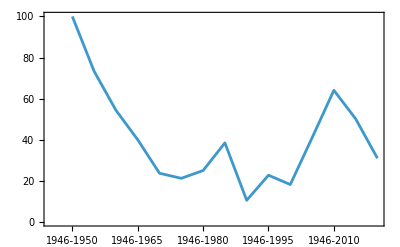

```mathematica
Labeled[ListPlot[newcomerratio,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"新規出現主要論文の全主要論文に占める割合（%）"]
```

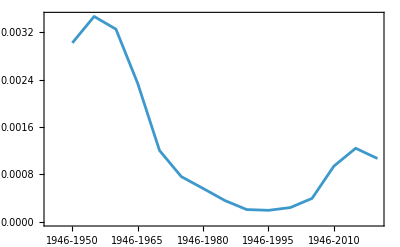

```mathematica
Labeled[ListPlot[top1pcArtRatio,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"主要論文の全論文に占める割合（%）"]
```

## （調査１）主要論文タイトル

PMIDから論文タイトルを引く

プログラム検討

```mathematica
st=Import["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/pubmed24n0080.xml.blk","String"];
```

```mathematica
st1=Drop[StringSplit[st,"<PubmedArticle>"],1];
```

```mathematica
st2=Map[StringSplit[#,"\n"]&,StringSplit[st1,"\n--\n"],{2}];
```

```mathematica
st3=Map[StringReplace[#,RegularExpression["\\[\\[\\[.*\\]\\]\\]"]->""]&,st2,{3}];
```

```mathematica
titlecase[l_]:=Cases[l,{x_,y_}/;StringMatchQ[x,"<PMID *"]||StringMatchQ[x,"<ArticleTitle>"]]
```

```mathematica
(st3case=Map[titlecase,st3])//Length
```

30000

```mathematica
st3case2=Map[#[[1;;2]]&,Select[st3case,Length[#]>=2&]]
```

```mathematica
st3rule=MapApply[Rule,Map[#[[2]]&,st3case2,{2}]]
```

```mathematica
blkToTitleRule[file_String]:=Module[{st,st1,st2,st3,st3case,st3case2,st3rule},
st=Import[file,"String"];
st1=Drop[StringSplit[st,"<PubmedArticle>"],1];
st2=Map[StringSplit[#,"\n"]&,StringSplit[st1,"\n--\n"],{2}];
st3=Map[StringReplace[#,RegularExpression["\\[\\[\\[.*\\]\\]\\]"]->""]&,st2,{3}];

st3case=Map[titlecase,st3];
st3case2=Map[#[[1;;2]]&,Select[st3case,Length[#]>=2&]];
st3rule=MapApply[Rule,Map[#[[2]]&,st3case2,{2}]]
]
```

プログラム適応

```mathematica
(blks=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/*blk"])//Length
```

1219

```mathematica
(*AbsoluteTiming[(pmidToTitle=Association[Flatten[ParallelMap[blkToTitleRule,blks]]]);]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save",pmidToTitle]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle_V2.save",pmidToTitle]*)
```

高被引用論文タイトル

ルールを読み込む

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];
```

```mathematica
top1pctitle=Map[{pmidToTitle[#[[1]]],#[[2]]}&,top1PcCitedArtList,{2}];
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitle.save",top1pctitle]*)
```

### 雑誌名つき高被引用論文タイトル

```mathematica
top1PcCitedArtList//Short
```

{{{16747784,74},{17247100,35},{16747456,32},«4»,{17247150,27},{18016252,26},{17751251,26}},«14»}

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/PMIDtoISSNrl.save"];
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal-title/ISSNvsTitle.save"];
```

```mathematica
(top1pctitlewithJ=Map[{pmidToTitle[#[[1]]],PMIDtoISSNrl[#[[1]]][[1]]//ISSNvsTitle,#[[2]]}&,top1PcCitedArtList,{2}])//Length
```

Part::partw: {}の部分1は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

15

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitlewithJ.save",top1pctitlewithJ]*)
```

#### 代表リスト

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
gen
```

{1946-1950,1946-1955,1946-1960,1946-1965,1946-1970,1946-1975,1946-1980,1946-1985,1946-1990,1946-1995,1946-2000,1946-2005,1946-2010,1946-2015,1946-2020}

ジャーナル名なし

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitle.save"];
```

```mathematica
top1pctitle//TableForm
```

Qualitative analysis of proteins: a partition chromatographic method using paper.
74 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
35 | The biochemistry of bacterial toxins: The lecithinase activity of Cl. welchii toxins.
32 | CLINICAL STUDIES OF THE BLOOD VOLUME. IV. ADAPTATION OF THE METHOD TO THE PHOTOELECTRIC MICROCOLORIMETER.
31 | CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.
29 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
28 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
28 | Bacteriophage-Resistant Mutants in Escherichia Coli.
27 | Pulmonary Calcification in Negative Reactors to Tuberculin.
26 | The Biological Actions and Therapeutic Applications of the B-Chloroethyl Amines and Sulfides.
26 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Qualitative analysis of proteins: a partition chromatographic method using paper.
154 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
120 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
103 | The free amino groups of insulin.
73 | A colorimetric method for the determination of glucosamine and chondrosamine.
71 | Separation of the phosphoric esters on the filter paper chromatogram.
68 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
67 | A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.
66 | The estimation of phosphorus.
65 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
62 | An improved method for the colorimetric determination of phosphate.
62 | The pharmacological actions of polymethylene bistrimethyl-ammonium salts.
62 | CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.
56 | [Proceedings of electrophoretic determination of blood proteins on filter paper].
55 | Studies on cholinesterase: 3. Specific tests for true cholinesterase and pseudo-cholinesterase.
54 | THE NITROUS OXIDE METHOD FOR THE QUANTITATIVE DETERMINATION OF CEREBRAL BLOOD FLOW IN MAN: THEORY, PROCEDURE AND NORMAL VALUES.
54 | The total nitrogen content of egg albumin and other proteins.
51 | The effect of sodium ions on the electrical activity of giant axon of the squid.
47 | The identification of lower peptides in complex mixtures.
47 | THE ESTIMATION OF HEPATIC BLOOD FLOW IN MAN.
46 | CLINICAL STUDIES OF THE BLOOD VOLUME. IV. ADAPTATION OF THE METHOD TO THE PHOTOELECTRIC MICROCOLORIMETER.
45 | Paper Chromatography Using Capillary Ascent.
43 | Bacteriophage-Resistant Mutants in Escherichia Coli.
43 | Protein measurement with the Folin phenol reagent.
43 | The estimation of adrenaline and allied substances in blood.
42 | Purification and properties of cytochrome c.
42 | Simultaneous Adaptation: A New Technique for the Study of Metabolic Pathways.
42 | Sickle cell anemia a molecular disease.
42 | [Electrophoresis of proteins on filter paper].
42 | The biochemistry of bacterial toxins: The lecithinase activity of Cl. welchii toxins.
41 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
300 | A study of fixation for electron microscopy.
235 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
203 | Qualitative analysis of proteins: a partition chromatographic method using paper.
190 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
176 | Separation of the phosphoric esters on the filter paper chromatogram.
150 | The estimation of phosphorus.
142 | An improved method for the colorimetric determination of phosphate.
141 | A colorimetric method for the determination of glucosamine and chondrosamine.
136 | The free amino groups of insulin.
106 | A small particulate component of the cytoplasm.
106 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
100 | An analysis of the end-plate potential recorded with an intracellular electrode.
100 | Methods of paper chromatography of steroids applicable to the study of steroids in mammalian blood and tissues.
99 | Chromatography of amino acids on sulfonated polystyrene resins.
98 | [Proceedings of electrophoretic determination of blood proteins on filter paper].
98 | The effect of sodium ions on the electrical activity of giant axon of the squid.
96 | A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.
95 | A study in microtomy for electron microscopy.
91 | Liver microsomes; an integrated morphological and biochemical study.
88 | The total nitrogen content of egg albumin and other proteins.
87 | Mutants of Escherichia coli requiring methionine or vitamin B12.
87 | [Quantitative determination of blood proteins by paper electrophoresis].
86 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
85 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
82 | Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.
82 | THE NITROUS OXIDE METHOD FOR THE QUANTITATIVE DETERMINATION OF CEREBRAL BLOOD FLOW IN MAN: THEORY, PROCEDURE AND NORMAL VALUES.
81 | Microelectrophoresis of protein on filter-paper.
80 | Sickle cell anemia a molecular disease.
79 | Electrophoresis of proteins on filter paper.
79 | Potassium accumulation in muscle and associated changes.
78 | The estimation of adrenaline and allied substances in blood.
77 | Chromatographic studies of nucleic acids; a technique for the identification and estimation of purine and pyrimidine bases, nucleosides and related substances.
76 | The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.
75 | CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.
74 | Nerve endings in mammalian muscle.
73 | The nucleic acids of plant tissues; the extraction and estimation of desoxypentose nucleic acid and pentose nucleic acid.
73 | The pharmacological actions of polymethylene bistrimethyl-ammonium salts.
73 | THE ESTIMATION OF HEPATIC BLOOD FLOW IN MAN.
72 | The recording of potentials from motoneurones with an intracellular electrode.
72 | The determination of hydroxyproline.
71 | An electron microscope study of the mitochondrial structure.
71 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
71 | The properdin system and immunity. I. Demonstration and isolation of a new serum protein, properdin, and its role in immune phenomena.
70 | The fine structure of mitochondria.
67 | The normal membrane potential of frog sartorius fibers.
65 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
1190 | A study of fixation for electron microscopy.
463 | Improvements in epoxy resin embedding methods.
338 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
269 | Separation of the phosphoric esters on the filter paper chromatogram.
226 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
224 | The estimation of phosphorus.
219 | Qualitative analysis of proteins: a partition chromatographic method using paper.
207 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
197 | An improved method for the colorimetric determination of phosphate.
194 | Staining of tissue sections for electron microscopy with heavy metals.
184 | Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.
178 | Genetic regulatory mechanisms in the synthesis of proteins.
178 | [A micro-method of immuno-electrophoresis].
174 | A colorimetric method for the determination of glucosamine and chondrosamine.
173 | Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.
173 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
169 | The effect of sodium ions on the electrical activity of giant axon of the squid.
167 | Effects of varying the vehicle for OsO4 in tissue fixation.
162 | A relation between non-esterified fatty acids in plasma and the metabolism of glucose.
159 | The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.
158 | Detection of sugars on paper chromatograms.
158 | A simple method for the isolation and purification of total lipides from animal tissues.
158 | An analysis of the end-plate potential recorded with an intracellular electrode.
157 | Mutants of Escherichia coli requiring methionine or vitamin B12.
156 | Simple methods for "staining with lead" at high pH in electron microscopy.
153 | The free amino groups of insulin.
151 | A small particulate component of the cytoplasm.
150 | Methods of paper chromatography of steroids applicable to the study of steroids in mammalian blood and tissues.
149 | Liver microsomes; an integrated morphological and biochemical study.
148 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
148 | Staining of tissue sections for electron microscopy with heavy metals. II. Application of solutions containing lead and barium.
146 | Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.
146 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
145 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
140 | Chromatography of amino acids on sulfonated polystyrene resins.
134 | Notes on sugar determination.
129 | A press for disrupting bacteria and other micro-organisms.
125 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
124 | Potassium accumulation in muscle and associated changes.
119 | Replica plating and indirect selection of bacterial mutants.
118 | [Proceedings of electrophoretic determination of blood proteins on filter paper].
115 | The determination of hydroxyproline.
113 | The fine structure of neurons.
113 | A revision of the Schoenheimer-Sperry method for cholesterol determination.
110 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
107 | The nucleic acids of plant tissues; the extraction and estimation of desoxypentose nucleic acid and pentose nucleic acid.
107 | A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.
106 | The total nitrogen content of egg albumin and other proteins.
106 | [Quantitative determination of blood proteins by paper electrophoresis].
105 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
3876 | Improvements in epoxy resin embedding methods.
1141 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
1099 | A study of fixation for electron microscopy.
684 | A simple method for the isolation and purification of total lipides from animal tissues.
611 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
579 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
564 | Staining of tissue sections for electron microscopy with heavy metals.
462 | [A micro-method of immuno-electrophoresis].
457 | Genetic regulatory mechanisms in the synthesis of proteins.
376 | Simple methods for "staining with lead" at high pH in electron microscopy.
362 | Detection of sugars on paper chromatograms.
319 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
318 | Chromosome preparations of leukocytes cultured from human peripheral blood.
311 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
309 | Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.
306 | Mutants of Escherichia coli requiring methionine or vitamin B12.
302 | Amino acid metabolism in mammalian cell cultures.
302 | A relation between non-esterified fatty acids in plasma and the metabolism of glucose.
297 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
297 | Separation of the phosphoric esters on the filter paper chromatogram.
296 | The estimation of phosphorus.
283 | Effects of varying the vehicle for OsO4 in tissue fixation.
278 | Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.
268 | Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.
266 | A method for determining the sedimentation behavior of enzymes: application to protein mixtures.
253 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
252 | Junctional complexes in various epithelia.
248 | A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.
246 | An improved method for the colorimetric determination of phosphate.
242 | The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.
239 | Phosphorus assay in column chromatography.
239 | The effect of sodium ions on the electrical activity of giant axon of the squid.
232 | A modified procedure for lead staining of thin sections.
228 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
222 | A colorimetric method for the determination of glucosamine and chondrosamine.
221 | Electron microscope study of DNA-containing plasms. II. Vegetative and mature phage DNA as compared with normal bacterial nucleoids in different physiological states.
220 | Qualitative analysis of proteins: a partition chromatographic method using paper.
216 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
9632 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
2400 | Improvements in epoxy resin embedding methods.
1898 | A simple method for the isolation and purification of total lipides from animal tissues.
1214 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
1129 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
862 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
856 | A study of fixation for electron microscopy.
826 | [A micro-method of immuno-electrophoresis].
741 | Staining of tissue sections for electron microscopy with heavy metals.
736 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
725 | Immunochemical quantitation of antigens by single radial immunodiffusion.
651 | A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.
630 | Amino acid metabolism in mammalian cell cultures.
569 | Mutants of Escherichia coli requiring methionine or vitamin B12.
556 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
517 | Chromosome preparations of leukocytes cultured from human peripheral blood.
508 | Genetic regulatory mechanisms in the synthesis of proteins.
506 | A method for determining the sedimentation behavior of enzymes: application to protein mixtures.
500 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
491 | Phosphorus assay in column chromatography.
490 | Detection of sugars on paper chromatograms.
463 | Simple methods for "staining with lead" at high pH in electron microscopy.
427 | Transduction of linked genetic characters of the host by bacteriophage P1.
424 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
422 | A relation between non-esterified fatty acids in plasma and the metabolism of glucose.
406 | The thiobarbituric acid assay of sialic acids.
391 | Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.
383 | Application of a microtechnique to viral serological investigations.
372 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
371 | Junctional complexes in various epithelia.
368 | Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.
366 | Separation of the phosphoric esters on the filter paper chromatogram.
363 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
17763 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
3332 | Improvements in epoxy resin embedding methods.
2359 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
2326 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
1916 | A simple method for the isolation and purification of total lipides from animal tissues.
1905 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
1683 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
1545 | Immunochemical quantitation of antigens by single radial immunodiffusion.
1199 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
967 | [A micro-method of immuno-electrophoresis].
887 | Staining of tissue sections for electron microscopy with heavy metals.
881 | A study of fixation for electron microscopy.
876 | A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.
867 | Phosphorus assay in column chromatography.
828 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
776 | Mutants of Escherichia coli requiring methionine or vitamin B12.
765 | Amino acid metabolism in mammalian cell cultures.
763 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
761 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
725 | A method for determining the sedimentation behavior of enzymes: application to protein mixtures.
720 | A low-viscosity epoxy resin embedding medium for electron microscopy.
715 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
704 | A rapid method of total lipid extraction and purification.
697 | Transduction of linked genetic characters of the host by bacteriophage P1.
674 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
671 | Recalibrated linkage map of Escherichia coli K-12.
669 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
669 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
646 | THE PREPARATION OF I-131-LABELLED HUMAN GROWTH HORMONE OF HIGH SPECIFIC RADIOACTIVITY.
620 | The thiobarbituric acid assay of sialic acids.
606 | Chromosome preparations of leukocytes cultured from human peripheral blood.
600 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
25451 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
8361 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
4209 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
3875 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
2669 | Improvements in epoxy resin embedding methods.
2565 | Sequencing end-labeled DNA with base-specific chemical cleavages.
2551 | A simple method for the isolation and purification of total lipides from animal tissues.
2481 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
2374 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
2336 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2074 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2009 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
1712 | Immunochemical quantitation of antigens by single radial immunodiffusion.
1679 | A new method for sequencing DNA.
1518 | High resolution two-dimensional electrophoresis of proteins.
1448 | DNA sequencing with chain-terminating inhibitors.
1405 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
1235 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
1232 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
1215 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
1207 | Phosphorus assay in column chromatography.
1165 | A rapid method of total lipid extraction and purification.
1139 | A low-viscosity epoxy resin embedding medium for electron microscopy.
1120 | Electrophoretic analysis of the major polypeptides of the human erythrocyte membrane.
1083 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
1077 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
32371 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
18419 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
8434 | DNA sequencing with chain-terminating inhibitors.
8093 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
6705 | Sequencing end-labeled DNA with base-specific chemical cleavages.
5060 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
4814 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4265 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
4242 | A simple method for the isolation and purification of total lipides from animal tissues.
3105 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
3036 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3023 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
2840 | Improvements in epoxy resin embedding methods.
2656 | High resolution two-dimensional electrophoresis of proteins.
2478 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
2460 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
2447 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2348 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2341 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
37576 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
28990 | DNA sequencing with chain-terminating inhibitors.
16313 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
12452 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
10601 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
8224 | Sequencing end-labeled DNA with base-specific chemical cleavages.
5856 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
5573 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
4643 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4628 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
4523 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
4284 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
3927 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
3915 | A simple method for the isolation and purification of total lipides from animal tissues.
3673 | A comprehensive set of sequence analysis programs for the VAX.
3504 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3182 | High resolution two-dimensional electrophoresis of proteins.
3079 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
2977 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
2864 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
2780 | Improvements in epoxy resin embedding methods.
2702 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
40229 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
35802 | DNA sequencing with chain-terminating inhibitors.
19737 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
16655 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
11243 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
10101 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
7559 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
6460 | Sequencing end-labeled DNA with base-specific chemical cleavages.
6102 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
5255 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
4936 | A comprehensive set of sequence analysis programs for the VAX.
4820 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
4755 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4668 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
4662 | A simple method for the isolation and purification of total lipides from animal tissues.
4146 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
3877 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
3541 | Basic local alignment search tool.
3541 | High resolution two-dimensional electrophoresis of proteins.
3335 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3236 | A simple method for displaying the hydropathic character of a protein.
3202 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
3048 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
2957 | A rapid method of total lipid extraction and purification.
2938 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
2917 | Improvements in epoxy resin embedding methods.
2714 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2628 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2619 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
2543 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
2525 | A new method for sequencing DNA.
2436 | Transformation of intact yeast cells treated with alkali cations.
2432 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
42101 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
40217 | DNA sequencing with chain-terminating inhibitors.
20676 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
20317 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
11511 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
11052 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
9288 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
6746 | Sequencing end-labeled DNA with base-specific chemical cleavages.
6209 | Basic local alignment search tool.
6140 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
5507 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
5404 | A comprehensive set of sequence analysis programs for the VAX.
5156 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
5018 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
5018 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
4777 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4674 | A simple method for the isolation and purification of total lipides from animal tissues.
4575 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
4536 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
4300 | A simple method for displaying the hydropathic character of a protein.
3721 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
3677 | High resolution two-dimensional electrophoresis of proteins.
3516 | A rapid method of total lipid extraction and purification.
3382 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3265 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
3127 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
3065 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
2990 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
2983 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
2902 | Improvements in epoxy resin embedding methods.
2727 | Transformation of intact yeast cells treated with alkali cations.
2709 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2666 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2656 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
2602 | Studies on transformation of Escherichia coli with plasmids.
2579 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
2562 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
2557 | The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.
2513 | A new method for sequencing DNA.
2477 | Improved tools for biological sequence comparison.
2417 | Genomic sequencing.
2372 | Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.
2272 | Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.
2257 | Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.
2212 | "A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.
2192 | New M13 vectors for cloning.
2171 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
2152 | Immunochemical quantitation of antigens by single radial immunodiffusion.
2100 | Selective extraction of polyoma DNA from infected mouse cell cultures.
2031 | Phosphorus assay in column chromatography.
1974 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
1956 | Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.
1954 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
1928 | Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.
1904 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
1874 | Continuous cultures of fused cells secreting antibody of predefined specificity.
1865 | Screening lambdagt recombinant clones by hybridization to single plaques in situ.
1850 | "Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.
1837 | A low-viscosity epoxy resin embedding medium for electron microscopy.
1759 | Measurement of protein using bicinchoninic acid.
1753 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
1682 | Unidirectional digestion with exonuclease III creates targeted breakpoints for DNA sequencing.
1667 | Use of T7 RNA polymerase to direct expression of cloned genes.
1644 | Improved methods for building protein models in electron density maps and the location of errors in these models.
1642 | Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.
1633 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
44884 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
44636 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
25913 | DNA sequencing with chain-terminating inhibitors.
21195 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
11864 | A short history of SHELX.
11691 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
11657 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
10736 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
10632 | Basic local alignment search tool.
10120 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
8976 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
6861 | Sequencing end-labeled DNA with base-specific chemical cleavages.
6297 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
5902 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
5504 | A simple method for the isolation and purification of total lipides from animal tissues.
5503 | A comprehensive set of sequence analysis programs for the VAX.
5254 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
5177 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
5080 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
5027 | Processing of X-ray diffraction data collected in oscillation mode.
4798 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
4760 | Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.
4732 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4675 | "Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.
4486 | The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.
4410 | A simple method for displaying the hydropathic character of a protein.
4387 | Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.
4334 | A rapid method of total lipid extraction and purification.
4316 | The CCP4 suite: programs for protein crystallography.
4080 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
3816 | High resolution two-dimensional electrophoresis of proteins.
3758 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
3574 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
3468 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3311 | Improved methods for building protein models in electron density maps and the location of errors in these models.
3230 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
3219 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
3181 | Coot: model-building tools for molecular graphics.
3157 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
3149 | Studies on transformation of Escherichia coli with plasmids.
3053 | Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.
3016 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
2996 | Transformation of intact yeast cells treated with alkali cations.
2964 | Initial sequencing and analysis of the human genome.
2918 | Statistical methods for assessing agreement between two methods of clinical measurement.
2863 | Improved tools for biological sequence comparison.
2791 | Improvements in epoxy resin embedding methods.
2751 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2743 | Refinement of macromolecular structures by the maximum-likelihood method.
2740 | The Protein Data Bank.
2710 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2686 | Cluster analysis and display of genome-wide expression patterns.
2673 | Genomic sequencing.
2604 | The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.
2576 | A new method for sequencing DNA.
2563 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
2562 | Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.
2510 | The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.
2413 | Structure validation in chemical crystallography.
2394 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
2389 | The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.
2353 | Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.
2332 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
2321 | Measurement of protein using bicinchoninic acid.
2317 | The hallmarks of cancer.
2312 | Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.
2282 | Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.
2234 | Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.
2233 | MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.
2214 | "A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.
2210 | New M13 vectors for cloning.
2192 | Selective extraction of polyoma DNA from infected mouse cell cultures.
2166 | MEGA3: Integrated software for Molecular Evolutionary Genetics Analysis and sequence alignment.
2154 | Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.
2128 | Immunochemical quantitation of antigens by single radial immunodiffusion.
2121 | Phosphorus assay in column chromatography.
2117 | Continuous cultures of fused cells secreting antibody of predefined specificity.
2104 | Significance analysis of microarrays applied to the ionizing radiation response.
2104 | Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.
2096 | Tricine-sodium dodecyl sulfate-polyacrylamide gel electrophoresis for the separation of proteins in the range from 1 to 100 kDa.
2060 | Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.
2050 | GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.
2027 | The assessment and analysis of handedness: the Edinburgh inventory.
2023 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
2017 | Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).
2011 | CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.
1995 | NMRPipe: a multidimensional spectral processing system based on UNIX pipes.
1970 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
1955 | "Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.
1940 | The genetics of Caenorhabditis elegans.
1940 | A low-viscosity epoxy resin embedding medium for electron microscopy.
1913 | MicroRNAs: genomics, biogenesis, mechanism, and function.
1902 | Primer3 on the WWW for general users and for biologist programmers.
1881 | Screening lambdagt recombinant clones by hybridization to single plaques in situ.
1852 | Use of T7 RNA polymerase to direct expression of cloned genes.
1839 | Haploview: analysis and visualization of LD and haplotype maps.
1820 | A new mathematical model for relative quantification in real-time RT-PCR.
1800 | Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.
1792 | One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.
1788 | Cancer statistics, 2008.
1785 | A simple salting out procedure for extracting DNA from human nucleated cells.
1777 | VMD: visual molecular dynamics.
1754 | The 1982 revised criteria for the classification of systemic lupus erythematosus.
1751 | Analysis of the genome sequence of the flowering plant Arabidopsis thaliana.
1730 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
1728 | The measurement of observer agreement for categorical data.
1714 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
1703 | Unidirectional digestion with exonuclease III creates targeted breakpoints for DNA sequencing.
1674 | Site-directed mutagenesis by overlap extension using the polymerase chain reaction.
1673 | A complementation analysis of the restriction and modification of DNA in Escherichia coli.
1661 | Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.
1643 | The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.
1635 | MODELTEST: testing the model of DNA substitution.
1629 | Single-step purification of polypeptides expressed in Escherichia coli as fusions with glutathione S-transferase.
1618 | Dendritic cells and the control of immunity.
1615 | Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.
1604 | Nitric oxide: physiology, pathophysiology, and pharmacology.
1600 | Solvent content of protein crystals.
1597 | A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.
1590 | Enzymatic amplification of beta-globin genomic sequences and restriction site analysis for diagnosis of sickle cell anemia.
1572 | Electrophoretic analysis of the major polypeptides of the human erythrocyte membrane.
1548 | An inventory for measuring depression.
1548 | TreeView: an application to display phylogenetic trees on personal computers.
1542 | The sequence of the human genome.
1538 | THE PREPARATION OF I-131-LABELLED HUMAN GROWTH HORMONE OF HIGH SPECIFIC RADIOACTIVITY.
1533 | The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.
1529 | Mfold web server for nucleic acid folding and hybridization prediction.
1527 | A rating scale for depression.
1523 | Peptide mapping by limited proteolysis in sodium dodecyl sulfate and analysis by gel electrophoresis.
1521 | SWISS-MODEL and the Swiss-PdbViewer: an environment for comparative protein modeling.
1513 | Atherosclerosis--an inflammatory disease.
1512 | Global cancer statistics, 2002.
1507 | Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.
1504 | The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.
1500 | The complete genome sequence of Escherichia coli K-12.
1495 | Efficient transfer of large DNA fragments from agarose gels to diazobenzyloxymethyl-paper and rapid hybridization by using dextran sulfate.
1491 | Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.
1485 | Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.
1477 | Relationship between the inhibition constant (K1) and the concentration of inhibitor which causes 50 per cent inhibition (I50) of an enzymatic reaction.
1469 | Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.
1467 | Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.
1466 | Use of bacteriophage T7 RNA polymerase to direct selective high-level expression of cloned genes.
1463 | MAPMAKER: an interactive computer package for constructing primary genetic linkage maps of experimental and natural populations.
1449 | MrBayes 3: Bayesian phylogenetic inference under mixed models.
1448 | High-efficiency transformation of mammalian cells by plasmid DNA.
1442 | Interpreting chromosomal DNA restriction patterns produced by pulsed-field gel electrophoresis: criteria for bacterial strain typing.
1441 | Preparation of iodine-131 labelled human growth hormone of high specific activity.
1435 | A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.
1426 | One-step gene disruption in yeast.
1406 | The 3'-terminal sequence of Escherichia coli 16S ribosomal RNA: complementarity to nonsense triplets and ribosome binding sites.
1400 | A membrane-filter technique for the detection of complementary DNA.
1399 | Organization and expression of eucaryotic split genes coding for proteins.
1394 | Integrins: versatility, modulation, and signaling in cell adhesion.
1394 | Quantitative film detection of 3H and 14C in polyacrylamide gels by fluorography.
1385 | MRBAYES: Bayesian inference of phylogenetic trees.
1375 | A rapid boiling method for the preparation of bacterial plasmids.
1373 | A simple and very efficient method for generating cDNA libraries.
1373 | Bioconductor: open software development for computational biology and bioinformatics.
1373 | Transformation of mammalian cells to antibiotic resistance with a bacterial gene under control of the SV40 early region promoter.
1363 | Tissue sulfhydryl groups.
1363 | The hospital anxiety and depression scale.
1361 | A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.
1360 | Sequence and organization of the human mitochondrial genome.
1359 | Duplexes of 21-nucleotide RNAs mediate RNA interference in cultured mammalian cells.
1359 | Sizing and mapping of early adenovirus mRNAs by gel electrophoresis of S1 endonuclease-digested hybrids.
1350 | MOLMOL: a program for display and analysis of macromolecular structures.
1348 | Colony hybridization: a method for the isolation of cloned DNAs that contain a specific gene.
1345 | WAF1, a potential mediator of p53 tumor suppression.
1344 | MUSCLE: multiple sequence alignment with high accuracy and high throughput.
1337 | PAML: a program package for phylogenetic analysis by maximum likelihood.
1313 | Initial sequencing and comparative analysis of the mouse genome.
1313 | Functional rafts in cell membranes.
1307 | Additional modules for versatile and economical PCR-based gene deletion and modification in Saccharomyces cerevisiae.
1305 | Prevalence of overweight and obesity in the United States, 1999-2004.
1305 | Base-calling of automated sequencer traces using phred. I. Accuracy assessment.
1299 | Cancer statistics, 2007.
1299 | New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.
1299 | Cloning in single-stranded bacteriophage as an aid to rapid DNA sequencing.
1284 | The role of protein kinase C in cell surface signal transduction and tumour promotion.
1282 | A simplification of the protein assay method of Lowry et al. which is more generally applicable.
1274 | A new pair of M13 vectors for selecting either DNA strand of double-digest restriction fragments.
1273 | A haplotype map of the human genome.
1269 | Identification of programmed cell death in situ via specific labeling of nuclear DNA fragmentation.
1263 | Exploration, normalization, and summaries of high density oligonucleotide array probe level data.
1260 | Translating the histone code.
1256 | A new method for predicting signal sequence cleavage sites.
1252 | The obligatory role of endothelial cells in the relaxation of arterial smooth muscle by acetylcholine.
1249 | Comparative protein modelling by satisfaction of spatial restraints.
1245 | Distantly related sequences in the alpha- and beta-subunits of ATP synthase, myosin, kinases and other ATP-requiring enzymes and a common nucleotide binding fold.
1241 | Bacterial evolution.
1237 | Deciphering the biology of Mycobacterium tuberculosis from the complete genome sequence.
1236 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
49961 | Protein measurement with the Folin phenol reagent.
49164 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
34711 | A short history of SHELX.
25235 | DNA sequencing with chain-terminating inhibitors.
21828 | Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.
18496 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
17655 | Basic local alignment search tool.
17099 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
13394 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
12849 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
11899 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
11777 | "Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.
10792 | Processing of X-ray diffraction data collected in oscillation mode.
9071 | Coot: model-building tools for molecular graphics.
8584 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
8247 | MEGA5: molecular evolutionary genetics analysis using maximum likelihood, evolutionary distance, and maximum parsimony methods.
7987 | Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.
7591 | A simple method for the isolation and purification of total lipides from animal tissues.
7550 | Global cancer statistics.
7492 | The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.
7115 | MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.
7065 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
6926 | MicroRNAs: genomics, biogenesis, mechanism, and function.
6917 | Structure validation in chemical crystallography.
6590 | The CCP4 suite: programs for protein crystallography.
6527 | Sequencing end-labeled DNA with base-specific chemical cleavages.
6375 | A rapid method of total lipid extraction and purification.
6326 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
6232 | Hallmarks of cancer: the next generation.
6017 | Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.
5926 | A new mathematical model for relative quantification in real-time RT-PCR.
5906 | Statistical methods for assessing agreement between two methods of clinical measurement.
5804 | MUSCLE: multiple sequence alignment with high accuracy and high throughput.
5801 | Clustal W and Clustal X version 2.0.
5749 | Systematic and integrative analysis of large gene lists using DAVID bioinformatics resources.
5732 | PLINK: a tool set for whole-genome association and population-based linkage analyses.
5696 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
5605 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
5584 | The assessment and analysis of handedness: the Edinburgh inventory.
5416 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
5414 | Meta-analysis in clinical trials.
5407 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
5362 | Refinement of macromolecular structures by the maximum-likelihood method.
5345 | The Protein Data Bank.
5311 | A comprehensive set of sequence analysis programs for the VAX.
5293 | A simple method for displaying the hydropathic character of a protein.
5232 | The hallmarks of cancer.
5201 | The measurement of observer agreement for categorical data.
5168 | Bias in meta-analysis detected by a simple, graphical test.
5043 | The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.
5002 | Measuring inconsistency in meta-analyses.
4989 | A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.
4949 | Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.
4935 | Initial sequencing and analysis of the human genome.
4840 | VMD: visual molecular dynamics.
4723 | Gene set enrichment analysis: a knowledge-based approach for interpreting genome-wide expression profiles.
4702 | Global cancer statistics, 2002.
4692 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4686 | Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.
4598 | Induction of pluripotent stem cells from mouse embryonic and adult fibroblast cultures by defined factors.
4595 | Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.
4528 | The Sequence Alignment/Map format and SAMtools.
4463 | Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.
4436 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
4385 | UCSF Chimera--a visualization system for exploratory research and analysis.
4379 | Primer3 on the WWW for general users and for biologist programmers.
4376 | Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).
4365 | Haploview: analysis and visualization of LD and haplotype maps.
4352 | Cancer statistics, 2010.
4297 | Cluster analysis and display of genome-wide expression patterns.
4277 | Fast and accurate short read alignment with Burrows-Wheeler transform.
4260 | Phaser crystallographic software.
4207 | Ultrafast and memory-efficient alignment of short DNA sequences to the human genome.
4158 | MrBayes 3: Bayesian phylogenetic inference under mixed models.
4145 | The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.
4109 | Bioconductor: open software development for computational biology and bioinformatics.
4059 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
3985 | CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.
3966 | High resolution two-dimensional electrophoresis of proteins.
3966 | Inference of population structure using multilocus genotype data.
3962 | Significance analysis of microarrays applied to the ionizing radiation response.
3959 | NMRPipe: a multidimensional spectral processing system based on UNIX pipes.
3920 | MicroRNAs: target recognition and regulatory functions.
3886 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
3884 | One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.
3877 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
3872 | The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.
3802 | Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.
3781 | Linear models and empirical bayes methods for assessing differential expression in microarray experiments.
3771 | New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.
3739 | Induction of pluripotent stem cells from adult human fibroblasts by defined factors.
3738 | Improved methods for building protein models in electron density maps and the location of errors in these models.
3735 | A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.
3734 | The hospital anxiety and depression scale.
3727 | The genetics of Caenorhabditis elegans.
3691 | PHENIX: a comprehensive Python-based system for macromolecular structure solution.
3651 | Cancer statistics, 2012.
3636 | Accurate normalization of real-time quantitative RT-PCR data by geometric averaging of multiple internal control genes.
3568 | Studies on transformation of Escherichia coli with plasmids.
3551 | The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.
3508 | Multilineage potential of adult human mesenchymal stem cells.
3457 | A rating scale for depression.
3454 | An inventory for measuring depression.
3439 | Cancer statistics, 2009.
3416 | Exploration, normalization, and summaries of high density oligonucleotide array probe level data.
3415 | Estimates of worldwide burden of cancer in 2008: GLOBOCAN 2008.
3396 | Cancer statistics, 2008.
3385 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3382 | Conserved seed pairing, often flanked by adenosines, indicates that thousands of human genes are microRNA targets.
3343 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
3323 | The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.
3297 | Cancer statistics, 2013.
3288 | Mfold web server for nucleic acid folding and hybridization prediction.
3263 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
3223 | Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.
3192 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
3162 | Transformation of intact yeast cells treated with alkali cations.
3154 | Features and development of Coot.
3135 | A simple salting out procedure for extracting DNA from human nucleated cells.
3128 | Measurement of protein using bicinchoninic acid.
3102 | MRBAYES: Bayesian inference of phylogenetic trees.
3096 | Improved tools for biological sequence comparison.
3064 | Radiotherapy plus concomitant and adjuvant temozolomide for glioblastoma.
3040 | Mapping and quantifying mammalian transcriptomes by RNA-Seq.
3034 | Atherosclerosis--an inflammatory disease.
3020 | Quantifying heterogeneity in a meta-analysis.
3018 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
3002 | Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.
2949 | A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.
2868 | Comparative protein modelling by satisfaction of spatial restraints.
2856 | Molecular portraits of human breast tumours.
2850 | MODELTEST: testing the model of DNA substitution.
2843 | KEGG: kyoto encyclopedia of genes and genomes.
2840 | MEGA3: Integrated software for Molecular Evolutionary Genetics Analysis and sequence alignment.
2822 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
2798 | Reduction in the incidence of type 2 diabetes with lifestyle intervention or metformin.
2795 | Improvements in epoxy resin embedding methods.
2781 | tRNAscan-SE: a program for improved detection of transfer RNA genes in genomic sequence.
2777 | DAVID: Database for Annotation, Visualization, and Integrated Discovery.
2774 | GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.
2771 | Solvent content of protein crystals.
2760 | Third Report of the National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, and Treatment of High Blood Cholesterol in Adults (Adult Treatment Panel III) final report.
2746 | Cytoscape: a software environment for integrated models of biomolecular interaction networks.
2745 | Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.
2742 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
2727 | Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.
2725 | Genomic sequencing.
2724 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
2722 | Obesity: preventing and managing the global epidemic. Report of a WHO consultation.
2718 | Analyzing real-time PCR data by the comparative C(T) method.
2712 | Dendritic cells and the control of immunity.
2684 | A new method for sequencing DNA.
2665 | Statistical significance for genomewide studies.
2663 | The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.
2642 | Embryonic stem cell lines derived from human blastocysts.
2633 | A map of human genome variation from population-scale sequencing.
2623 | Statistical aspects of the analysis of data from retrospective studies of disease.
2620 | Principal components analysis corrects for stratification in genome-wide association studies.
2612 | Induced pluripotent stem cell lines derived from human somatic cells.
2598 | A comparison of normalization methods for high density oligonucleotide array data based on variance and bias.
2594 | RAxML-VI-HPC: maximum likelihood-based phylogenetic analyses with thousands of taxa and mixed models.
2576 | The Psychophysics Toolbox.
2569 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
2569 | Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.
2563 | A more accurate method to estimate glomerular filtration rate from serum creatinine: a new prediction equation. Modification of Diet in Renal Disease Study Group.
2551 | Continuous cultures of fused cells secreting antibody of predefined specificity.
2539 | SWISS-MODEL and the Swiss-PdbViewer: an environment for comparative protein modeling.
2528 | Velvet: algorithms for de novo short read assembly using de Bruijn graphs.
2520 | Chromatin modifications and their function.
2515 | Predicting transmembrane protein topology with a hidden Markov model: application to complete genomes.
2513 | All-atom empirical potential for molecular modeling and dynamics studies of proteins.
2492 | Tricine-sodium dodecyl sulfate-polyacrylamide gel electrophoresis for the separation of proteins in the range from 1 to 100 kDa.
2490 | The amyloid hypothesis of Alzheimer's disease: progress and problems on the road to therapeutics.
2476 | The 1982 revised criteria for the classification of systemic lupus erythematosus.
2461 | The Mini-International Neuropsychiatric Interview (M.I.N.I.): the development and validation of a structured diagnostic psychiatric interview for DSM-IV and ICD-10.
2459 | Assessing the quality of reports of randomized clinical trials: is blinding necessary?
2458 | WebLogo: a sequence logo generator.
2453 | Scalable molecular dynamics with NAMD.
2448 | Automated anatomical labeling of activations in SPM using a macroscopic anatomical parcellation of the MNI MRI single-subject brain.
2445 | Prevalence of overweight and obesity in the United States, 1999-2004.
2428 | BLAT--the BLAST-like alignment tool.
2414 | Genome sequencing in microfabricated high-density picolitre reactors.
2412 | Inflammation and cancer.
2411 | Analysis of the genome sequence of the flowering plant Arabidopsis thaliana.
2411 | Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.
2409 | AFNI: software for analysis and visualization of functional magnetic resonance neuroimages.
2402 | Prospective identification of tumorigenic breast cancer cells.
2387 | A default mode of brain function.
2382 | A 12-Item Short-Form Health Survey: construction of scales and preliminary tests of reliability and validity.
2378 | Seventh report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure.
2368 | TopHat: discovering splice junctions with RNA-Seq.
2367 | NIH Image to ImageJ: 25 years of image analysis.
2366 | The C. elegans heterochronic gene lin-4 encodes small RNAs with antisense complementarity to lin-14.
2364 | Translating the histone code.
2361 | Gene Expression Omnibus: NCBI gene expression and hybridization array data repository.
2350 | Gene expression patterns of breast carcinomas distinguish tumor subclasses with clinical implications.
2348 | Global prevalence of diabetes: estimates for the year 2000 and projections for 2030.
2323 | Statistical method for testing the neutral mutation hypothesis by DNA polymorphism.
2320 | MicroRNA expression profiles classify human cancers.
2318 | Assay for lipid peroxides in animal tissues by thiobarbituric acid reaction.
2311 | The sequence of the human genome.
2302 | BEAST: Bayesian evolutionary analysis by sampling trees.
2301 | Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.
2289 | Phosphorus assay in column chromatography.
2275 | Selective extraction of polyoma DNA from infected mouse cell cultures.
2274 | APACHE II: a severity of disease classification system.
2266 | Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.
2264 | Tissue sulfhydryl groups.
2257 | XDS.
2255 | Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.
2250 | Neuropathological stageing of Alzheimer-related changes.
2250 | Advances in functional and structural MR image analysis and implementation as FSL.
2242 | The functions of animal microRNAs.
2242 | Cancer statistics, 2014.
2239 | New M13 vectors for cloning.
2233 | Site-directed mutagenesis by overlap extension using the polymerase chain reaction.
2232 | Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.
2222 | "A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.
2219 | K/DOQI clinical practice guidelines for chronic kidney disease: evaluation, classification, and stratification.
2210 | Lifetime prevalence and age-of-onset distributions of DSM-IV disorders in the National Comorbidity Survey Replication.
2209 | Improved prediction of signal peptides: SignalP 3.0.
2193 | The PHQ-9: validity of a brief depression severity measure.
2192 | Activating mutations in the epidermal growth factor receptor underlying responsiveness of non-small-cell lung cancer to gefitinib.
2183 | An integrated encyclopedia of DNA elements in the human genome.
2178 | Risks and benefits of estrogen plus progestin in healthy postmenopausal women: principal results From the Women's Health Initiative randomized controlled trial.
2176 | Prediction of creatinine clearance from serum creatinine.
2174 | The FagerstrÃ¶m Test for Nicotine Dependence: a revision of the FagerstrÃ¶m Tolerance Questionnaire.
2170 | TreeView: an application to display phylogenetic trees on personal computers.
2169 | Bioinformatics enrichment tools: paths toward the comprehensive functional analysis of large gene lists.
2155 | A method and server for predicting damaging missense mutations.
2147 | Immunochemical quantitation of antigens by single radial immunodiffusion.
2142 | Development of the Colle-Salvetti correlation-energy formula into a functional of the electron density.
2141 | High-resolution profiling of histone methylations in the human genome.
2140 | The RAST Server: rapid annotations using subsystems technology.
2136 | Relationship between the inhibition constant (K1) and the concentration of inhibitor which causes 50 per cent inhibition (I50) of an enzymatic reaction.
2135 | The Pittsburgh Sleep Quality Index: a new instrument for psychiatric practice and research.
2133 | The positive and negative syndrome scale (PANSS) for schizophrenia.
2125 | Development and validation of brief measures of positive and negative affect: the PANAS scales.
2120 | PAML 4: phylogenetic analysis by maximum likelihood.
2113 | Transcript assembly and quantification by RNA-Seq reveals unannotated transcripts and isoform switching during cell differentiation.
2112 | A low-viscosity epoxy resin embedding medium for electron microscopy.
2109 | Intraclass correlations: uses in assessing rater reliability.
2108 | The human genome browser at UCSC.
2108 | Arlequin (version 3.0): an integrated software package for population genetics data analysis.
2107 | Vitamin D deficiency.
2105 | Additional modules for versatile and economical PCR-based gene deletion and modification in Saccharomyces cerevisiae.
2104 | Base-calling of automated sequencer traces using phred. I. Accuracy assessment.
2101 | Gene expression profiling predicts clinical outcome of breast cancer.
2101 | EMBOSS: the European Molecular Biology Open Software Suite.
2101 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
2097 | Cancer statistics, 2007.
2087 | MolProbity: all-atom structure validation for macromolecular crystallography.
2085 | Differential expression analysis for sequence count data.
2084 | Nitric oxide: physiology, pathophysiology, and pharmacology.
2080 | "Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.
2076 | Stem cells, cancer, and cancer stem cells.
2074 | Duplexes of 21-nucleotide RNAs mediate RNA interference in cultured mammalian cells.
2073 | Initial sequencing and comparative analysis of the mouse genome.
2068 | Interpreting chromosomal DNA restriction patterns produced by pulsed-field gel electrophoresis: criteria for bacterial strain typing.
2063 | Pathogen recognition and innate immunity.
2052 | The complete genome sequence of Escherichia coli K-12.
2045 | Human breast cancer: correlation of relapse and survival with amplification of the HER-2/neu oncogene.
2044 | The 2007 WHO classification of tumours of the central nervous system.
2043 | RNA-Seq: a revolutionary tool for transcriptomics.
2042 | Bevacizumab plus irinotecan, fluorouracil, and leucovorin for metastatic colorectal cancer.
2030 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
2029 | Overview of the CCP4 suite and current developments.
2011 | Establishing a standard definition for child overweight and obesity worldwide: international survey.
2008 | The meaning and use of the area under a receiver operating characteristic (ROC) curve.
2000 | Use of T7 RNA polymerase to direct expression of cloned genes.
1994 | A haplotype map of the human genome.
1992 | Comprehensive genomic characterization defines human glioblastoma genes and core pathways.
1990 | On the origin of cancer cells.
1988 | Deciphering the biology of Mycobacterium tuberculosis from the complete genome sequence.
1976 | EuroQol--a new facility for the measurement of health-related quality of life.
1974 | A genetic model for colorectal tumorigenesis.
1973 | A new and rapid colorimetric determination of acetylcholinesterase activity.
1972 | A synaptic model of memory: long-term potentiation in the hippocampus.
1971 | Finding the missing heritability of complex diseases.
1970 | Autism Diagnostic Interview-Revised: a revised version of a diagnostic interview for caregivers of individuals with possible pervasive developmental disorders.
1963 | Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.
1962 | An integrative theory of prefrontal cortex function.
1961 | Base-calling of automated sequencer traces using phred. II. Error probabilities.
1959 | The epithelial-mesenchymal transition generates cells with properties of stem cells.
1951 | Generalized lacZ expression with the ROSA26 Cre reporter strain.
1939 | Crystal structure of the nucleosome core particle at 2.8 A resolution.
1937 | A global measure of perceived stress.
1932 | A power primer.
1932 | Introducing mothur: open-source, platform-independent, community-supported software for describing and comparing microbial communities.
1930 | The Genome Analysis Toolkit: a MapReduce framework for analyzing next-generation DNA sequencing data.
1921 | Stages of embryonic development of the zebrafish.
1920 | Functional rafts in cell membranes.
1915 | Improved survival with ipilimumab in patients with metastatic melanoma.
1912 | The language of covalent histone modifications.
1911 | EGFR mutations in lung cancer: correlation with clinical response to gefitinib therapy.
1909 | Mutations of the BRAF gene in human cancer.
1909 | Blast2GO: a universal tool for annotation, visualization and analysis in functional genomics research.
1903 | The ubiquitin system.
1899 | Operating characteristics of a rank correlation test for publication bias.
1899 | Mass spectrometric sequencing of proteins silver-stained polyacrylamide gels.
1898 | Collective dynamics of 'small-world' networks.
1896 | New response evaluation criteria in solid tumours: revised RECIST guideline (version 1.1).
1893 | QIIME allows analysis of high-throughput community sequencing data.
1891 | Inference of macromolecular assemblies from crystalline state.
1887 | Integrins: bidirectional, allosteric signaling machines.
1880 | Positional cloning of the mouse obese gene and its human homologue.
1879 | Control of goal-directed and stimulus-driven attention in the brain.
1878 | MEGA6: Molecular Evolutionary Genetics Analysis version 6.0.
1875 | MOLMOL: a program for display and analysis of macromolecular structures.
1856 | Screening lambdagt recombinant clones by hybridization to single plaques in situ.
1856 | Functional connectivity in the motor cortex of resting human brain using echo-planar MRI.
1848 | MAPMAKER: an interactive computer package for constructing primary genetic linkage maps of experimental and natural populations.
1846 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
1844 | Apoptosis: a basic biological phenomenon with wide-ranging implications in tissue kinetics.
1843 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
54249 | Protein measurement with the Folin phenol reagent.
53050 | Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.
47343 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
44350 | A short history of SHELX.
27998 | Basic local alignment search tool.
26196 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
23032 | DNA sequencing with chain-terminating inhibitors.
22517 | Hallmarks of cancer: the next generation.
18449 | "Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.
18152 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
16282 | The Sequence Alignment/Map format and SAMtools.
15705 | Systematic and integrative analysis of large gene lists using DAVID bioinformatics resources.
14250 | Global cancer statistics.
13930 | Fast and accurate short read alignment with Burrows-Wheeler transform.
13533 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
13523 | Measuring inconsistency in meta-analyses.
13449 | MicroRNAs: genomics, biogenesis, mechanism, and function.
13435 | Coot: model-building tools for molecular graphics.
13318 | Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.
13202 | Gene set enrichment analysis: a knowledge-based approach for interpreting genome-wide expression profiles.
13016 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
12950 | MUSCLE: multiple sequence alignment with high accuracy and high throughput.
12906 | MEGA5: molecular evolutionary genetics analysis using maximum likelihood, evolutionary distance, and maximum parsimony methods.
12418 | Global cancer statistics 2018: GLOBOCAN estimates of incidence and mortality worldwide for 36 cancers in 185 countries.
12151 | Fast gapped-read alignment with Bowtie 2.
12038 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
12009 | Bias in meta-analysis detected by a simple, graphical test.
11911 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
11896 | Processing of X-ray diffraction data collected in oscillation mode.
11884 | Moderated estimation of fold change and  dispersion for RNA-seq data with DESeq2.
11520 | MEGA6: Molecular Evolutionary Genetics Analysis version 6.0.
11338 | UCSF Chimera--a visualization system for exploratory research and analysis.
11217 | PLINK: a tool set for whole-genome association and population-based linkage analyses.
11169 | Global cancer statistics, 2012.
11146 | NIH Image to ImageJ: 25 years of image analysis.
11117 | The measurement of observer agreement for categorical data.
11001 | A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.
10863 | Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.
10847 | Fiji: an open-source platform for biological-image analysis.
10590 | Meta-analysis in clinical trials.
10447 | A new mathematical model for relative quantification in real-time RT-PCR.
10424 | Trimmomatic: a flexible trimmer for Illumina sequence data.
10321 | A simple method for the isolation and purification of total lipides from animal tissues.
10284 | Cytoscape: a software environment for integrated models of biomolecular interaction networks.
10013 | edgeR: a Bioconductor package for differential expression analysis of digital gene expression data.
9769 | PHENIX: a comprehensive Python-based system for macromolecular structure solution.
9687 | QIIME allows analysis of high-throughput community sequencing data.
9614 | Clustal W and Clustal X version 2.0.
9543 | Statistical methods for assessing agreement between two methods of clinical measurement.
9470 | Cancer incidence and mortality worldwide: sources, methods and major patterns in GLOBOCAN 2012.
9397 | VMD: visual molecular dynamics.
9355 | Ultrafast and memory-efficient alignment of short DNA sequences to the human genome.
9279 | Features and development of Coot.
9110 | The assessment and analysis of handedness: the Edinburgh inventory.
9098 | Phaser crystallographic software.
8781 | A rapid method of total lipid extraction and purification.
8775 | The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.
8772 | The Protein Data Bank.
8507 | MEGA7: Molecular Evolutionary Genetics Analysis Version 7.0 for Bigger Datasets.
8481 | The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.
8278 | MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.
8203 | Clinical features of patients infected with 2019 novel coronavirus in Wuhan, China.
8187 | The hospital anxiety and depression scale.
8103 | Induction of pluripotent stem cells from mouse embryonic and adult fibroblast cultures by defined factors.
8084 | MicroRNAs: target recognition and regulatory functions.
8058 | Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.
8044 | Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.
8013 | STAR: ultrafast universal RNA-seq aligner.
7784 | The hallmarks of cancer.
7743 | Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.
7600 | The CCP4 suite: programs for protein crystallography.
7525 | The Genome Analysis Toolkit: a MapReduce framework for analyzing next-generation DNA sequencing data.
7523 | Inference of population structure using multilocus genotype data.
7490 | Structure validation in chemical crystallography.
7480 | Research electronic data capture (REDCap)--a metadata-driven methodology and workflow process for providing translational research informatics support.
7479 | KEGG: kyoto encyclopedia of genes and genomes.
7468 | Quantifying heterogeneity in a meta-analysis.
7340 | Analyzing real-time PCR data by the comparative C(T) method.
7319 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
6956 | Refinement of macromolecular structures by the maximum-likelihood method.
6923 | MAFFT multiple sequence alignment software version 7: improvements in performance and usability.
6909 | Cancer statistics, 2016.
6879 | New response evaluation criteria in solid tumours: revised RECIST guideline (version 1.1).
6735 | The PHQ-9: validity of a brief depression severity measure.
6674 | Initial sequencing and analysis of the human genome.
6614 | Induction of pluripotent stem cells from adult human fibroblasts by defined factors.
6535 | MrBayes 3: Bayesian phylogenetic inference under mixed models.
6499 | Radiotherapy plus concomitant and adjuvant temozolomide for glioblastoma.
6461 | Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.
6454 | Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.
6451 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
6426 | An integrated encyclopedia of DNA elements in the human genome.
6411 | Sequencing end-labeled DNA with base-specific chemical cleavages.
6408 | RAxML version 8: a tool for phylogenetic analysis and post-analysis of large phylogenies.
6396 | Accurate normalization of real-time quantitative RT-PCR data by geometric averaging of multiple internal control genes.
6373 | Cancer Statistics, 2017.
6275 | Estimates of worldwide burden of cancer in 2008: GLOBOCAN 2008.
6251 | CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.
6244 | The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.
6242 | Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).
6211 | G*Power 3: a flexible statistical power analysis program for the social, behavioral, and biomedical sciences.
6186 | BEDTools: a flexible suite of utilities for comparing genomic features.
6181 | One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.
6170 | Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.
6122 | A simple method for displaying the hydropathic character of a protein.
6120 | Haploview: analysis and visualization of LD and haplotype maps.
6113 | Global cancer statistics, 2002.
6096 | Differential expression analysis for sequence count data.
6076 | Transcript assembly and quantification by RNA-Seq reveals unannotated transcripts and isoform switching during cell differentiation.
6037 | SPAdes: a new genome assembly algorithm and its applications to single-cell sequencing.
6011 | XDS.
5992 | A new equation to estimate glomerular filtration rate.
5927 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
5921 | TopHat: discovering splice junctions with RNA-Seq.
5894 | Bioconductor: open software development for computational biology and bioinformatics.
5892 | Cancer statistics in China, 2015.
5869 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
5862 | Search and clustering orders of magnitude faster than BLAST.
5852 | Generalized Gradient Approximation Made Simple.
5820 | A rating scale for depression.
5760 | Bioinformatics enrichment tools: paths toward the comprehensive functional analysis of large gene lists.
5742 | Mapping and quantifying mammalian transcriptomes by RNA-Seq.
5730 | NMRPipe: a multidimensional spectral processing system based on UNIX pipes.
5724 | The genetics of Caenorhabditis elegans.
5724 | Cancer statistics, 2013.
5714 | Cancer statistics, 2015.
5685 | limma powers differential expression analyses for RNA-sequencing and microarray studies.
5649 | Cancer statistics, 2010.
5640 | Cancer statistics, 2018.
5633 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
5629 | Classification of surgical complications: a new proposal with evaluation in a cohort of 6336 patients and results of a survey.
5600 | An inventory for measuring depression.
5596 | Introducing mothur: open-source, platform-independent, community-supported software for describing and comparing microbial communities.
5588 | Linear models and empirical bayes methods for assessing differential expression in microarray experiments.
5582 | HTSeq--a Python framework to work with high-throughput sequencing data.
5581 | Full-length transcriptome assembly from RNA-Seq data without a reference genome.
5557 | The Pittsburgh Sleep Quality Index: a new instrument for psychiatric practice and research.
5555 | The Mini-International Neuropsychiatric Interview (M.I.N.I.): the development and validation of a structured diagnostic psychiatric interview for DSM-IV and ICD-10.
5537 | Clinical Characteristics of Coronavirus Disease 2019 in China.
5526 | Cancer statistics, 2014.
5525 | MolProbity: all-atom structure validation for macromolecular crystallography.
5523 | The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.
5512 | Multilineage potential of adult human mesenchymal stem cells.
5510 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
5500 | The Cochrane Collaboration's tool for assessing risk of bias in randomised trials.
5445 | The Psychophysics Toolbox.
5412 | Primer3 on the WWW for general users and for biologist programmers.
5412 | Obesity: preventing and managing the global epidemic. Report of a WHO consultation.
5352 | A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.
5332 | TopHat2: accurate alignment of transcriptomes in the presence of insertions, deletions and gene fusions.
5302 | A comprehensive set of sequence analysis programs for the VAX.
5299 | Cluster analysis and display of genome-wide expression patterns.
5271 | The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.
5236 | Conserved seed pairing, often flanked by adenosines, indicates that thousands of human genes are microRNA targets.
5228 | Automated anatomical labeling of activations in SPM using a macroscopic anatomical parcellation of the MNI MRI single-subject brain.
5191 | Cancer statistics, 2012.
5134 | New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.
5115 | Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.
5102 | Exploration, normalization, and summaries of high density oligonucleotide array probe level data.
5100 | A method and server for predicting damaging missense mutations.
5061 | Differential gene and transcript expression analysis of RNA-seq experiments with TopHat and Cufflinks.
5020 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
5002 | Significance analysis of microarrays applied to the ionizing radiation response.
4922 | Overview of the CCP4 suite and current developments.
4900 | Model-based analysis of ChIP-Seq (MACS).
4881 | A power primer.
4853 | Clinical Characteristics of 138 Hospitalized Patients With 2019 Novel Coronavirus-Infected Pneumonia in Wuhan, China.
4852 | New algorithms and methods to estimate maximum-likelihood phylogenies: assessing the performance of PhyML 3.0.
4847 | Mfold web server for nucleic acid folding and hybridization prediction.
4838 | Clinical course and risk factors for mortality of adult inpatients with COVID-19 in Wuhan, China: a retrospective cohort study.
4828 | The RAST Server: rapid annotations using subsystems technology.
4828 | Naive Bayesian classifier for rapid assignment of rRNA sequences into the new bacterial taxonomy.
4827 | Scalable molecular dynamics with NAMD.
4827 | Improved survival with ipilimumab in patients with metastatic melanoma.
4808 | A global measure of perceived stress.
4805 | The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.
4799 | Molecular portraits of human breast tumours.
4780 | Multiplex genome engineering using CRISPR/Cas systems.
4763 | Gene Expression Omnibus: NCBI gene expression and hybridization array data repository.
4756 | tRNAscan-SE: a program for improved detection of transfer RNA genes in genomic sequence.
4753 | Meta-analysis of observational studies in epidemiology: a proposal for reporting. Meta-analysis Of Observational Studies in Epidemiology (MOOSE) group.
4742 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
4694 | Understanding the Warburg effect: the metabolic requirements of cell proliferation.
4689 | A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.
4669 | RAxML-VI-HPC: maximum likelihood-based phylogenetic analyses with thousands of taxa and mixed models.
4666 | The cBio cancer genomics portal: an open platform for exploring multidimensional cancer genomics data.
4662 | Reduction in the incidence of type 2 diabetes with lifestyle intervention or metformin.
4645 | Minimal criteria for defining multipotent mesenchymal stromal cells. The International Society for Cellular Therapy position statement.
4632 | MRBAYES: Bayesian inference of phylogenetic trees.
4602 | WebLogo: a sequence logo generator.
4600 | Velvet: algorithms for de novo short read assembly using de Bruijn graphs.
4597 | Advances in functional and structural MR image analysis and implementation as FSL.
4590 | RSEM: accurate transcript quantification from RNA-Seq data with or without a reference genome.
4588 | Development and validation of brief measures of positive and negative affect: the PANAS scales.
4577 | A 12-Item Short-Form Health Survey: construction of scales and preliminary tests of reliability and validity.
4506 | Comparing the areas under two or more correlated receiver operating characteristic curves: a nonparametric approach.
4467 | Operating characteristics of a rank correlation test for publication bias.
4466 | Principal components analysis corrects for stratification in genome-wide association studies.
4464 | Predicting transmembrane protein topology with a hidden Markov model: application to complete genomes.
4460 | A Novel Coronavirus from Patients with Pneumonia in China, 2019.
4457 | Comprehensive molecular portraits of human breast tumours.
4457 | Inflammation and cancer.
4444 | Development of the Colle-Salvetti correlation-energy formula into a functional of the electron density.
4432 | Third Report of the National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, and Treatment of High Blood Cholesterol in Adults (Adult Treatment Panel III) final report.
4425 | Comparative protein modelling by satisfaction of spatial restraints.
4422 | Blast2GO: a universal tool for annotation, visualization and analysis in functional genomics research.
4419 | Geneious Basic: an integrated and extendable desktop software platform for the organization and analysis of sequence data.
4416 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
4409 | Cancer statistics, 2019.
4401 | Safety, activity, and immune correlates of anti-PD-1 antibody in cancer.
4388 | Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.
4386 | MaxQuant enables high peptide identification rates, individualized p.p.b.-range mass accuracies and proteome-wide protein quantification.
4374 | A simple salting out procedure for extracting DNA from human nucleated cells.
4342 | Fast, scalable generation of high-quality protein multiple sequence alignments using Clustal Omega.
4339 | PAML 4: phylogenetic analysis by maximum likelihood.
4333 | Lifetime prevalence and age-of-onset distributions of DSM-IV disorders in the National Comorbidity Survey Replication.
4320 | Detecting the number of clusters of individuals using the software STRUCTURE: a simulation study.
4299 | Three approaches to qualitative content analysis.
4287 | Atherosclerosis--an inflammatory disease.
4282 | Integrative analysis of complex cancer genomics and clinical profiles using the cBioPortal.
4240 | The functions of animal microRNAs.
4240 | Standards and guidelines for the interpretation of sequence variants: a joint consensus recommendation of the American College of Medical Genetics and Genomics and the Association for Molecular Pathology.
4224 | A framework for variation discovery and genotyping using next-generation DNA sequencing data.
4222 | EEGLAB: an open source toolbox for analysis of single-trial EEG dynamics including independent component analysis.
4209 | Frailty in older adults: evidence for a phenotype.
4208 | Neuropathological stageing of Alzheimer-related changes.
4203 | AFNI: software for analysis and visualization of functional magnetic resonance neuroimages.
4193 | Global and regional mortality from 235 causes of death for 20 age groups in 1990 and 2010: a systematic analysis for the Global Burden of Disease Study 2010.
4183 | EuroQol--a new facility for the measurement of health-related quality of life.
4183 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
4182 | MrBayes 3.2: efficient Bayesian phylogenetic inference and model choice across a large model space.
4181 | Cancer statistics, 2009.
4177 | DAVID: Database for Annotation, Visualization, and Integrated Discovery.
4131 | Epidemiological and clinical characteristics of 99 cases of 2019 novel coronavirus pneumonia in Wuhan, China: a descriptive study.
4110 | High resolution two-dimensional electrophoresis of proteins.
4106 | Assessing the quality of reports of randomized clinical trials: is blinding necessary?
4099 | The positive and negative syndrome scale (PANSS) for schizophrenia.
4097 | A more accurate method to estimate glomerular filtration rate from serum creatinine: a new prediction equation. Modification of Diet in Renal Disease Study Group.
4095 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
4085 | On the origin of cancer cells.
4077 | BLAST+: architecture and applications.
4060 | Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.
4058 | Cancer statistics, 2008.
4057 | Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.
4052 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
4051 | Statistical significance for genomewide studies.
4049 | DnaSP v5: a software for comprehensive analysis of DNA polymorphism data.
4045 | The amyloid hypothesis of Alzheimer's disease: progress and problems on the road to therapeutics.
4043 | Embryonic stem cell lines derived from human blastocysts.
4039 | Assay for lipid peroxides in animal tissues by thiobarbituric acid reaction.
4021 | Studies on transformation of Escherichia coli with plasmids.
4020 | The SILVA ribosomal RNA gene database project: improved data processing and web-based tools.
4015 | The human genome browser at UCSC.
4011 | RNA-Seq: a revolutionary tool for transcriptomics.
4010 | Intraclass correlations: uses in assessing rater reliability.
4010 | International physical activity questionnaire: 12-country reliability and validity.
3999 | The 2007 WHO classification of tumours of the central nervous system.
3986 | A default mode of brain function.
3969 | Epithelial-mesenchymal transitions in development and disease.
3943 | Exosome-mediated transfer of mRNAs and microRNAs is a novel mechanism of genetic exchange between cells.
3935 | The C. elegans heterochronic gene lin-4 encodes small RNAs with antisense complementarity to lin-14.
3929 | Measurement of protein using bicinchoninic acid.
3902 | Statistical aspects of the analysis of data from retrospective studies of disease.
3898 | Improved methods for building protein models in electron density maps and the location of errors in these models.
3896 | Chromatin modifications and their function.
3892 | A map of human genome variation from population-scale sequencing.
3891 | Integrative genomics viewer.
3876 | Improved optimization for the robust and accurate linear registration and motion correction of brain images.
3856 | Sorafenib in advanced hepatocellular carcinoma.
3854 | ANNOVAR: functional annotation of genetic variants from high-throughput sequencing data.
3849 | WGCNA: an R package for weighted correlation network analysis.
3836 | The MIQE guidelines: minimum information for publication of quantitative real-time PCR experiments.
3832 | Standardisation of spirometry.
3829 | Prospective identification of tumorigenic breast cancer cells.
3825 | World Medical Association Declaration of Helsinki: ethical principles for medical research involving human subjects.
3810 | Vitamin D deficiency.
3810 | Induced pluripotent stem cell lines derived from human somatic cells.
3793 | Analysis of protein-coding genetic variation in 60,706 humans.
3782 | An integrated map of genetic variation from 1,092 human genomes.
3778 | Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.
3775 | Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.
3742 | UCHIME improves sensitivity and speed of chimera detection.
3737 | A programmable dual-RNA-guided DNA endonuclease in adaptive bacterial immunity.
3736 | Inference of macromolecular assemblies from crystalline state.
3731 | A comparison of normalization methods for high density oligonucleotide array data based on variance and bias.
3726 | BLAT--the BLAST-like alignment tool.
3726 | All-atom empirical potential for molecular modeling and dynamics studies of proteins.
3714 | The FagerstrÃ¶m Test for Nicotine Dependence: a revision of the FagerstrÃ¶m Tolerance Questionnaire.
3694 | AutoDock Vina: improving the speed and accuracy of docking with a new scoring function, efficient optimization, and multithreading.
3693 | Gene expression patterns of breast carcinomas distinguish tumor subclasses with clinical implications.
3684 | The epithelial-mesenchymal transition generates cells with properties of stem cells.
3675 | SignalP 4.0: discriminating signal peptides from transmembrane regions.
3668 | The Montreal Cognitive Assessment, MoCA: a brief screening tool for mild cognitive impairment.
3653 | MicroRNA expression profiles classify human cancers.
3629 | Statistical method for testing the neutral mutation hypothesis by DNA polymorphism.
3628 | APACHE II: a severity of disease classification system.
3612 | The basics of epithelial-mesenchymal transition.
3608 | The blockade of immune checkpoints in cancer immunotherapy.
3607 | Fast and accurate long-read alignment with Burrows-Wheeler transform.
3603 | Fast robust automated brain extraction.
3603 | A global reference for human genetic variation.
3601 | Global prevalence of diabetes: estimates for the year 2000 and projections for 2030.
3591 | Collective dynamics of 'small-world' networks.
3587 | BEAST: Bayesian evolutionary analysis by sampling trees.
3576 | Matrix elasticity directs stem cell lineage specification.
3575 | Greengenes, a chimera-checked 16S rRNA gene database and workbench compatible with ARB.
3566 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
3524 | Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.
3504 | Dendritic cells and the control of immunity.
3503 | GenAlEx 6.5: genetic analysis in Excel. Population genetic software for teaching and research--an update.
3503 | MODELTEST: testing the model of DNA substitution.
3497 | Cancer-related inflammation.
3486 | EMBOSS: the European Molecular Biology Open Software Suite.
3484 | Tissue sulfhydryl groups.
3483 | The meaning and use of the area under a receiver operating characteristic (ROC) curve.
3475 | Functional connectivity in the motor cortex of resting human brain using echo-planar MRI.
3472 | Harmonizing the metabolic syndrome: a joint interim statement of the International Diabetes Federation Task Force on Epidemiology and Prevention; National Heart, Lung, and Blood Institute; American Heart Association; World Heart Federation; International Atherosclerosis Society; and International Association for the Study of Obesity.
3469 | K/DOQI clinical practice guidelines for chronic kidney disease: evaluation, classification, and stratification.
3469 | Seventh report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure.
3463 | GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.
3455 | Activating mutations in the epidermal growth factor receptor underlying responsiveness of non-small-cell lung cancer to gefitinib.
3448 | Cortical surface-based analysis. I. Segmentation and surface reconstruction.
3441 | Consolidated criteria for reporting qualitative research (COREQ): a 32-item checklist for interviews and focus groups.
3437 | Simple combinations of lineage-determining transcription factors prime cis-regulatory elements required for macrophage and B cell identities.
3434 | The Third International Consensus Definitions for Sepsis and Septic Shock (Sepsis-3).
3423 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
3422 | Preferred reporting items for systematic review and meta-analysis protocols (PRISMA-P) 2015 statement.
3422 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
3418 | A new method for measuring daytime sleepiness: the Epworth sleepiness scale.
3398 | Pathogen recognition and innate immunity.
3391 | Stages of embryonic development of the zebrafish.
3373 | Comprehensive genomic characterization defines human glioblastoma genes and core pathways.
3370 | Crystal structure refinement with SHELXL.
3362 | Stem cells, cancer, and cancer stem cells.
3343 | An obesity-associated gut microbiome with increased capacity for energy harvest.
3327

ジャーナル名つき

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top1pctitlewithJ.save"];
```

Part::partw: {}の部分1は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

```mathematica
top1pctitlewithJ//TableForm
```

Qualitative analysis of proteins: a partition chromatographic method using paper.
The Biochemical journal
74 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
Genetics
35 | The biochemistry of bacterial toxins: The lecithinase activity of Cl. welchii toxins.
The Biochemical journal
32 | CLINICAL STUDIES OF THE BLOOD VOLUME. IV. ADAPTATION OF THE METHOD TO THE PHOTOELECTRIC MICROCOLORIMETER.
The Journal of clinical investigation
31 | CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.
The Journal of clinical investigation
29 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
The Biochemical journal
28 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
The Journal of clinical investigation
28 | Bacteriophage-Resistant Mutants in Escherichia Coli.
Genetics
27 | Pulmonary Calcification in Negative Reactors to Tuberculin.
American journal of public health and the nation's health
26 | The Biological Actions and Therapeutic Applications of the B-Chloroethyl Amines and Sulfides.
Science (New York, N.Y.)
26 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Qualitative analysis of proteins: a partition chromatographic method using paper.
The Biochemical journal
154 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
The Biochemical journal
120 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
The Biochemical journal
103 | The free amino groups of insulin.
The Biochemical journal
73 | A colorimetric method for the determination of glucosamine and chondrosamine.
The Biochemical journal
71 | Separation of the phosphoric esters on the filter paper chromatogram.
Nature
68 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
The Journal of clinical investigation
67 | A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.
The Biochemical journal
66 | The estimation of phosphorus.
The Biochemical journal
65 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
Genetics
62 | An improved method for the colorimetric determination of phosphate.
The Biochemical journal
62 | The pharmacological actions of polymethylene bistrimethyl-ammonium salts.
British journal of pharmacology and chemotherapy
62 | CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.
The Journal of clinical investigation
56 | [Proceedings of electrophoretic determination of blood proteins on filter paper].
Deutsche medizinische Wochenschrift (1946)
55 | Studies on cholinesterase: 3. Specific tests for true cholinesterase and pseudo-cholinesterase.
The Biochemical journal
54 | THE NITROUS OXIDE METHOD FOR THE QUANTITATIVE DETERMINATION OF CEREBRAL BLOOD FLOW IN MAN: THEORY, PROCEDURE AND NORMAL VALUES.
The Journal of clinical investigation
54 | The total nitrogen content of egg albumin and other proteins.
The Biochemical journal
51 | The effect of sodium ions on the electrical activity of giant axon of the squid.
The Journal of physiology
47 | The identification of lower peptides in complex mixtures.
The Biochemical journal
47 | THE ESTIMATION OF HEPATIC BLOOD FLOW IN MAN.
The Journal of clinical investigation
46 | CLINICAL STUDIES OF THE BLOOD VOLUME. IV. ADAPTATION OF THE METHOD TO THE PHOTOELECTRIC MICROCOLORIMETER.
The Journal of clinical investigation
45 | Paper Chromatography Using Capillary Ascent.
Science (New York, N.Y.)
43 | Bacteriophage-Resistant Mutants in Escherichia Coli.
Genetics
43 | Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
43 | The estimation of adrenaline and allied substances in blood.
The Journal of physiology
42 | Purification and properties of cytochrome c.
The Biochemical journal
42 | Simultaneous Adaptation: A New Technique for the Study of Metabolic Pathways.
Journal of bacteriology
42 | Sickle cell anemia a molecular disease.
Science (New York, N.Y.)
42 | [Electrophoresis of proteins on filter paper].
Biochemische Zeitschrift
42 | The biochemistry of bacterial toxins: The lecithinase activity of Cl. welchii toxins.
The Biochemical journal
41 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
300 | A study of fixation for electron microscopy.
The Journal of experimental medicine
235 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
The Biochemical journal
203 | Qualitative analysis of proteins: a partition chromatographic method using paper.
The Biochemical journal
190 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
The Biochemical journal
176 | Separation of the phosphoric esters on the filter paper chromatogram.
Nature
150 | The estimation of phosphorus.
The Biochemical journal
142 | An improved method for the colorimetric determination of phosphate.
The Biochemical journal
141 | A colorimetric method for the determination of glucosamine and chondrosamine.
The Biochemical journal
136 | The free amino groups of insulin.
The Biochemical journal
106 | A small particulate component of the cytoplasm.
The Journal of biophysical and biochemical cytology
106 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
The Journal of clinical investigation
100 | An analysis of the end-plate potential recorded with an intracellular electrode.
The Journal of physiology
100 | Methods of paper chromatography of steroids applicable to the study of steroids in mammalian blood and tissues.
The Biochemical journal
99 | Chromatography of amino acids on sulfonated polystyrene resins.
The Journal of biological chemistry
98 | [Proceedings of electrophoretic determination of blood proteins on filter paper].
Deutsche medizinische Wochenschrift (1946)
98 | The effect of sodium ions on the electrical activity of giant axon of the squid.
The Journal of physiology
96 | A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.
The Biochemical journal
95 | A study in microtomy for electron microscopy.
The Anatomical record
91 | Liver microsomes; an integrated morphological and biochemical study.
The Journal of biophysical and biochemical cytology
88 | The total nitrogen content of egg albumin and other proteins.
The Biochemical journal
87 | Mutants of Escherichia coli requiring methionine or vitamin B12.
Journal of bacteriology
87 | [Quantitative determination of blood proteins by paper electrophoresis].
Hoppe-Seyler's Zeitschrift fur physiologische Chemie
86 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
The Journal of experimental medicine
85 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
Genetics
82 | Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.
The Journal of experimental medicine
82 | THE NITROUS OXIDE METHOD FOR THE QUANTITATIVE DETERMINATION OF CEREBRAL BLOOD FLOW IN MAN: THEORY, PROCEDURE AND NORMAL VALUES.
The Journal of clinical investigation
81 | Microelectrophoresis of protein on filter-paper.
Lancet (London, England)
80 | Sickle cell anemia a molecular disease.
Science (New York, N.Y.)
79 | Electrophoresis of proteins on filter paper.
The Journal of general physiology
79 | Potassium accumulation in muscle and associated changes.
The Journal of physiology
78 | The estimation of adrenaline and allied substances in blood.
The Journal of physiology
77 | Chromatographic studies of nucleic acids; a technique for the identification and estimation of purine and pyrimidine bases, nucleosides and related substances.
The Biochemical journal
76 | The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.
The Journal of experimental medicine
75 | CLINICAL STUDIES OF THE BLOOD VOLUME. I. CLINICAL APPLICATION OF A METHOD EMPLOYING THE AZO DYE "EVANS BLUE" AND THE SPECTROPHOTOMETER.
The Journal of clinical investigation
74 | Nerve endings in mammalian muscle.
The Journal of physiology
73 | The nucleic acids of plant tissues; the extraction and estimation of desoxypentose nucleic acid and pentose nucleic acid.
Archives of biochemistry
73 | The pharmacological actions of polymethylene bistrimethyl-ammonium salts.
British journal of pharmacology and chemotherapy
73 | THE ESTIMATION OF HEPATIC BLOOD FLOW IN MAN.
The Journal of clinical investigation
72 | The recording of potentials from motoneurones with an intracellular electrode.
The Journal of physiology
72 | The determination of hydroxyproline.
The Journal of biological chemistry
71 | An electron microscope study of the mitochondrial structure.
The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
71 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
The Journal of physiology
71 | The properdin system and immunity. I. Demonstration and isolation of a new serum protein, properdin, and its role in immune phenomena.
Science (New York, N.Y.)
70 | The fine structure of mitochondria.
The Anatomical record
67 | The normal membrane potential of frog sartorius fibers.
Journal of cellular and comparative physiology
65 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
1190 | A study of fixation for electron microscopy.
The Journal of experimental medicine
463 | Improvements in epoxy resin embedding methods.
The Journal of biophysical and biochemical cytology
338 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
The Biochemical journal
269 | Separation of the phosphoric esters on the filter paper chromatogram.
Nature
226 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
The Biochemical journal
224 | The estimation of phosphorus.
The Biochemical journal
219 | Qualitative analysis of proteins: a partition chromatographic method using paper.
The Biochemical journal
207 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
The Biochemical journal
197 | An improved method for the colorimetric determination of phosphate.
The Biochemical journal
194 | Staining of tissue sections for electron microscopy with heavy metals.
The Journal of biophysical and biochemical cytology
184 | Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.
The Journal of experimental medicine
178 | Genetic regulatory mechanisms in the synthesis of proteins.
Journal of molecular biology
178 | [A micro-method of immuno-electrophoresis].
International archives of allergy and applied immunology
174 | A colorimetric method for the determination of glucosamine and chondrosamine.
The Biochemical journal
173 | Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.
The Biochemical journal
173 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
The Journal of experimental medicine
169 | The effect of sodium ions on the electrical activity of giant axon of the squid.
The Journal of physiology
167 | Effects of varying the vehicle for OsO4 in tissue fixation.
The Journal of biophysical and biochemical cytology
162 | A relation between non-esterified fatty acids in plasma and the metabolism of glucose.
The Journal of clinical investigation
159 | The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.
The Journal of experimental medicine
158 | Detection of sugars on paper chromatograms.
Nature
158 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
158 | An analysis of the end-plate potential recorded with an intracellular electrode.
The Journal of physiology
157 | Mutants of Escherichia coli requiring methionine or vitamin B12.
Journal of bacteriology
156 | Simple methods for "staining with lead" at high pH in electron microscopy.
The Journal of biophysical and biochemical cytology
153 | The free amino groups of insulin.
The Biochemical journal
151 | A small particulate component of the cytoplasm.
The Journal of biophysical and biochemical cytology
150 | Methods of paper chromatography of steroids applicable to the study of steroids in mammalian blood and tissues.
The Biochemical journal
149 | Liver microsomes; an integrated morphological and biochemical study.
The Journal of biophysical and biochemical cytology
148 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
The Journal of physiology
148 | Staining of tissue sections for electron microscopy with heavy metals. II. Application of solutions containing lead and barium.
The Journal of biophysical and biochemical cytology
146 | Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.
The Biochemical journal
146 | THE RENAL CLEARANCES OF SUBSTITUTED HIPPURIC ACID DERIVATIVES AND OTHER AROMATIC ACIDS IN DOG AND MAN.
The Journal of clinical investigation
145 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
140 | Chromatography of amino acids on sulfonated polystyrene resins.
The Journal of biological chemistry
134 | Notes on sugar determination.
The Journal of biological chemistry
129 | A press for disrupting bacteria and other micro-organisms.
British journal of experimental pathology
125 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
The Journal of cell biology
124 | Potassium accumulation in muscle and associated changes.
The Journal of physiology
119 | Replica plating and indirect selection of bacterial mutants.
Journal of bacteriology
118 | [Proceedings of electrophoretic determination of blood proteins on filter paper].
Deutsche medizinische Wochenschrift (1946)
115 | The determination of hydroxyproline.
The Journal of biological chemistry
113 | The fine structure of neurons.
The Journal of biophysical and biochemical cytology
113 | A revision of the Schoenheimer-Sperry method for cholesterol determination.
The Journal of biological chemistry
110 | Mutations of Bacteria from Virus Sensitivity to Virus Resistance.
Genetics
107 | The nucleic acids of plant tissues; the extraction and estimation of desoxypentose nucleic acid and pentose nucleic acid.
Archives of biochemistry
107 | A study of the behaviour of some sixty amino-acids and other ninhydrin-reacting substances on phenol-;collidine' filter-paper chromatograms, with notes as to the occurrence of some of them in biological fluids.
The Biochemical journal
106 | The total nitrogen content of egg albumin and other proteins.
The Biochemical journal
106 | [Quantitative determination of blood proteins by paper electrophoresis].
Hoppe-Seyler's Zeitschrift fur physiologische Chemie
105 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
3876 | Improvements in epoxy resin embedding methods.
The Journal of biophysical and biochemical cytology
1141 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
1099 | A study of fixation for electron microscopy.
The Journal of experimental medicine
684 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
611 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
The Biochemical journal
579 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
The Journal of cell biology
564 | Staining of tissue sections for electron microscopy with heavy metals.
The Journal of biophysical and biochemical cytology
462 | [A micro-method of immuno-electrophoresis].
International archives of allergy and applied immunology
457 | Genetic regulatory mechanisms in the synthesis of proteins.
Journal of molecular biology
376 | Simple methods for "staining with lead" at high pH in electron microscopy.
The Journal of biophysical and biochemical cytology
362 | Detection of sugars on paper chromatograms.
Nature
319 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
The Journal of experimental medicine
318 | Chromosome preparations of leukocytes cultured from human peripheral blood.
Experimental cell research
311 | Filter-paper partition chromatography of sugars: 1. General description and application to the qualitative analysis of sugars in apple juice, egg white and foetal blood of sheep. with a note by R. G. Westall.
The Biochemical journal
309 | Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.
The Biochemical journal
306 | Mutants of Escherichia coli requiring methionine or vitamin B12.
Journal of bacteriology
302 | Amino acid metabolism in mammalian cell cultures.
Science (New York, N.Y.)
302 | A relation between non-esterified fatty acids in plasma and the metabolism of glucose.
The Journal of clinical investigation
297 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
The Journal of physiology
297 | Separation of the phosphoric esters on the filter paper chromatogram.
Nature
296 | The estimation of phosphorus.
The Biochemical journal
283 | Effects of varying the vehicle for OsO4 in tissue fixation.
The Journal of biophysical and biochemical cytology
278 | Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.
The Biochemical journal
268 | Localization of antigen in tissue cells; improvements in a method for the detection of antigen by means of fluorescent antibody.
The Journal of experimental medicine
266 | A method for determining the sedimentation behavior of enzymes: application to protein mixtures.
The Journal of biological chemistry
253 | A steam distillation apparatus suitable for micro-Kjeldahl analysis.
The Biochemical journal
252 | Junctional complexes in various epithelia.
The Journal of cell biology
248 | A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.
The Journal of cell biology
246 | An improved method for the colorimetric determination of phosphate.
The Biochemical journal
242 | The adsorption of proteins on erythrocytes treated with tannic acid and subsequent hemagglutination by antiprotein sera.
The Journal of experimental medicine
239 | Phosphorus assay in column chromatography.
The Journal of biological chemistry
239 | The effect of sodium ions on the electrical activity of giant axon of the squid.
The Journal of physiology
232 | A modified procedure for lead staining of thin sections.
The Journal of biophysical and biochemical cytology
228 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
Annals of the New York Academy of Sciences
222 | A colorimetric method for the determination of glucosamine and chondrosamine.
The Biochemical journal
221 | Electron microscope study of DNA-containing plasms. II. Vegetative and mature phage DNA as compared with normal bacterial nucleoids in different physiological states.
The Journal of biophysical and biochemical cytology
220 | Qualitative analysis of proteins: a partition chromatographic method using paper.
The Biochemical journal
216 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
9632 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
2400 | Improvements in epoxy resin embedding methods.
The Journal of biophysical and biochemical cytology
1898 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
1214 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
The Biochemical journal
1129 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
The Journal of cell biology
862 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
Annals of the New York Academy of Sciences
856 | A study of fixation for electron microscopy.
The Journal of experimental medicine
826 | [A micro-method of immuno-electrophoresis].
International archives of allergy and applied immunology
741 | Staining of tissue sections for electron microscopy with heavy metals.
The Journal of biophysical and biochemical cytology
736 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
The Journal of biological chemistry
725 | Immunochemical quantitation of antigens by single radial immunodiffusion.
Immunochemistry
651 | A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.
The Journal of cell biology
630 | Amino acid metabolism in mammalian cell cultures.
Science (New York, N.Y.)
569 | Mutants of Escherichia coli requiring methionine or vitamin B12.
Journal of bacteriology
556 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
The Journal of experimental medicine
517 | Chromosome preparations of leukocytes cultured from human peripheral blood.
Experimental cell research
508 | Genetic regulatory mechanisms in the synthesis of proteins.
Journal of molecular biology
506 | A method for determining the sedimentation behavior of enzymes: application to protein mixtures.
The Journal of biological chemistry
500 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
The Journal of physiology
491 | Phosphorus assay in column chromatography.
The Journal of biological chemistry
490 | Detection of sugars on paper chromatograms.
Nature
463 | Simple methods for "staining with lead" at high pH in electron microscopy.
The Journal of biophysical and biochemical cytology
427 | Transduction of linked genetic characters of the host by bacteriophage P1.
Virology
424 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
Plant physiology
422 | A relation between non-esterified fatty acids in plasma and the metabolism of glucose.
The Journal of clinical investigation
406 | The thiobarbituric acid assay of sialic acids.
The Journal of biological chemistry
391 | Tissue fractionation studies.  6.  Intracellular distribution patterns of enzymes in rat-liver tissue.
The Biochemical journal
383 | Application of a microtechnique to viral serological investigations.
Journal of immunology (Baltimore, Md. : 1950)
372 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
The Journal of biological chemistry
371 | Junctional complexes in various epithelia.
The Journal of cell biology
368 | Zone electrophoresis in starch gels:  group variations in the serum proteins of normal human adults.
The Biochemical journal
366 | Separation of the phosphoric esters on the filter paper chromatogram.
Nature
363 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
17763 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
3332 | Improvements in epoxy resin embedding methods.
The Journal of biophysical and biochemical cytology
2359 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
Nature
2326 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
The Journal of biological chemistry
1916 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
1905 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
The Biochemical journal
1683 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
Annals of the New York Academy of Sciences
1545 | Immunochemical quantitation of antigens by single radial immunodiffusion.
Immunochemistry
1199 | Cytochemistry and electron microscopy. The preservation of cellular ultrastructure and enzymatic activity by aldehyde fixation.
The Journal of cell biology
967 | [A micro-method of immuno-electrophoresis].
International archives of allergy and applied immunology
887 | Staining of tissue sections for electron microscopy with heavy metals.
The Journal of biophysical and biochemical cytology
881 | A study of fixation for electron microscopy.
The Journal of experimental medicine
876 | A SIMPLIFIED LEAD CITRATE STAIN FOR USE IN ELECTRON MICROSCOPY.
The Journal of cell biology
867 | Phosphorus assay in column chromatography.
The Journal of biological chemistry
828 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
776 | Mutants of Escherichia coli requiring methionine or vitamin B12.
Journal of bacteriology
765 | Amino acid metabolism in mammalian cell cultures.
Science (New York, N.Y.)
763 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
The Journal of physiology
761 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
Plant physiology
725 | A method for determining the sedimentation behavior of enzymes: application to protein mixtures.
The Journal of biological chemistry
720 | A low-viscosity epoxy resin embedding medium for electron microscopy.
Journal of ultrastructure research
715 | Plaque formation and isolation of pure lines with poliomyelitis viruses.
The Journal of experimental medicine
704 | A rapid method of total lipid extraction and purification.
Missing[KeyAbsent,{}⟦1⟧]
697 | Transduction of linked genetic characters of the host by bacteriophage P1.
Virology
674 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
The Journal of biological chemistry
671 | Recalibrated linkage map of Escherichia coli K-12.
Bacteriological reviews
669 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
Journal of molecular biology
669 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
European journal of biochemistry
646 | THE PREPARATION OF I-131-LABELLED HUMAN GROWTH HORMONE OF HIGH SPECIFIC RADIOACTIVITY.
The Biochemical journal
620 | The thiobarbituric acid assay of sialic acids.
The Journal of biological chemistry
606 | Chromosome preparations of leukocytes cultured from human peripheral blood.
Experimental cell research
600 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
25451 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
Nature
8361 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
Journal of molecular biology
4209 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
3875 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
The Journal of biological chemistry
2669 | Improvements in epoxy resin embedding methods.
The Journal of biophysical and biochemical cytology
2565 | Sequencing end-labeled DNA with base-specific chemical cleavages.
Methods in enzymology
2551 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
2481 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
Analytical biochemistry
2374 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
Journal of molecular biology
2336 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
The Biochemical journal
2074 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
Annals of the New York Academy of Sciences
2009 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
European journal of biochemistry
1712 | Immunochemical quantitation of antigens by single radial immunodiffusion.
Immunochemistry
1679 | A new method for sequencing DNA.
Proceedings of the National Academy of Sciences of the United States of America
1518 | High resolution two-dimensional electrophoresis of proteins.
The Journal of biological chemistry
1448 | DNA sequencing with chain-terminating inhibitors.
Proceedings of the National Academy of Sciences of the United States of America
1405 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
Proceedings of the National Academy of Sciences of the United States of America
1235 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
Nucleic acids research
1232 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
Plant physiology
1215 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1207 | Phosphorus assay in column chromatography.
The Journal of biological chemistry
1165 | A rapid method of total lipid extraction and purification.
Missing[KeyAbsent,{}⟦1⟧]
1139 | A low-viscosity epoxy resin embedding medium for electron microscopy.
Journal of ultrastructure research
1120 | Electrophoretic analysis of the major polypeptides of the human erythrocyte membrane.
Biochemistry
1083 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
Proceedings of the National Academy of Sciences of the United States of America
1077 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
32371 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
Nature
18419 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
Journal of molecular biology
8434 | DNA sequencing with chain-terminating inhibitors.
Proceedings of the National Academy of Sciences of the United States of America
8093 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
Analytical biochemistry
6705 | Sequencing end-labeled DNA with base-specific chemical cleavages.
Methods in enzymology
5060 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
Proceedings of the National Academy of Sciences of the United States of America
4814 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
Journal of molecular biology
4265 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
4242 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
3105 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
Nucleic acids research
3036 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
The Journal of biological chemistry
3023 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
Biochemistry
2840 | Improvements in epoxy resin embedding methods.
The Journal of biophysical and biochemical cytology
2656 | High resolution two-dimensional electrophoresis of proteins.
The Journal of biological chemistry
2478 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
Analytical biochemistry
2460 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
Proceedings of the National Academy of Sciences of the United States of America
2447 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
The Biochemical journal
2348 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
Annals of the New York Academy of Sciences
2341 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
37576 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
Nature
28990 | DNA sequencing with chain-terminating inhibitors.
Proceedings of the National Academy of Sciences of the United States of America
16313 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
Analytical biochemistry
12452 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
Journal of molecular biology
10601 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
Proceedings of the National Academy of Sciences of the United States of America
8224 | Sequencing end-labeled DNA with base-specific chemical cleavages.
Methods in enzymology
5856 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
Analytical biochemistry
5573 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
Biochemistry
4643 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
Journal of molecular biology
4628 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
4523 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
Nucleic acids research
4284 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
Gene
3927 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
Analytical biochemistry
3915 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
3673 | A comprehensive set of sequence analysis programs for the VAX.
Nucleic acids research
3504 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
The Journal of biological chemistry
3182 | High resolution two-dimensional electrophoresis of proteins.
The Journal of biological chemistry
3079 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
Science (New York, N.Y.)
2977 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
Proceedings of the National Academy of Sciences of the United States of America
2864 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
Pflugers Archiv : European journal of physiology
2780 | Improvements in epoxy resin embedding methods.
The Journal of biophysical and biochemical cytology
2702 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
40229 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
Nature
35802 | DNA sequencing with chain-terminating inhibitors.
Proceedings of the National Academy of Sciences of the United States of America
19737 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
Analytical biochemistry
16655 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
Journal of molecular biology
11243 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
Proceedings of the National Academy of Sciences of the United States of America
10101 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
Analytical biochemistry
7559 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
Analytical biochemistry
6460 | Sequencing end-labeled DNA with base-specific chemical cleavages.
Methods in enzymology
6102 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
Biochemistry
5255 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
Gene
4936 | A comprehensive set of sequence analysis programs for the VAX.
Nucleic acids research
4820 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
Nucleic acids research
4755 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
Journal of molecular biology
4668 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
4662 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
4146 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
Pflugers Archiv : European journal of physiology
3877 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
Science (New York, N.Y.)
3541 | Basic local alignment search tool.
Journal of molecular biology
3541 | High resolution two-dimensional electrophoresis of proteins.
The Journal of biological chemistry
3335 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
The Journal of biological chemistry
3236 | A simple method for displaying the hydropathic character of a protein.
Journal of molecular biology
3202 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
Molecular and cellular biology
3048 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
Proceedings of the National Academy of Sciences of the United States of America
2957 | A rapid method of total lipid extraction and purification.
Missing[KeyAbsent,{}⟦1⟧]
2938 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
Virology
2917 | Improvements in epoxy resin embedding methods.
The Journal of biophysical and biochemical cytology
2714 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
The Biochemical journal
2628 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
Annals of the New York Academy of Sciences
2619 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
European journal of biochemistry
2543 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
Nucleic acids research
2525 | A new method for sequencing DNA.
Proceedings of the National Academy of Sciences of the United States of America
2436 | Transformation of intact yeast cells treated with alkali cations.
Journal of bacteriology
2432 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
42101 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
Nature
40217 | DNA sequencing with chain-terminating inhibitors.
Proceedings of the National Academy of Sciences of the United States of America
20676 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
Analytical biochemistry
20317 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
Journal of molecular biology
11511 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
Proceedings of the National Academy of Sciences of the United States of America
11052 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
Analytical biochemistry
9288 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
Analytical biochemistry
6746 | Sequencing end-labeled DNA with base-specific chemical cleavages.
Methods in enzymology
6209 | Basic local alignment search tool.
Journal of molecular biology
6140 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
Gene
5507 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
Biochemistry
5404 | A comprehensive set of sequence analysis programs for the VAX.
Nucleic acids research
5156 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
Nucleic acids research
5018 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
Nucleic acids research
5018 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
4777 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
Journal of molecular biology
4674 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
4575 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
Pflugers Archiv : European journal of physiology
4536 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
Nucleic acids research
4300 | A simple method for displaying the hydropathic character of a protein.
Journal of molecular biology
3721 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
Science (New York, N.Y.)
3677 | High resolution two-dimensional electrophoresis of proteins.
The Journal of biological chemistry
3516 | A rapid method of total lipid extraction and purification.
Missing[KeyAbsent,{}⟦1⟧]
3382 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
The Journal of biological chemistry
3265 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
Molecular and cellular biology
3127 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
Virology
3065 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
Nucleic acids research
2990 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
Proceedings of the National Academy of Sciences of the United States of America
2983 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
The Journal of biological chemistry
2902 | Improvements in epoxy resin embedding methods.
The Journal of biophysical and biochemical cytology
2727 | Transformation of intact yeast cells treated with alkali cations.
Journal of bacteriology
2709 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
Annals of the New York Academy of Sciences
2666 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
The Biochemical journal
2656 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
Molecular biology and evolution
2602 | Studies on transformation of Escherichia coli with plasmids.
Journal of molecular biology
2579 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
Genetics
2562 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
European journal of biochemistry
2557 | The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.
Gene
2513 | A new method for sequencing DNA.
Proceedings of the National Academy of Sciences of the United States of America
2477 | Improved tools for biological sequence comparison.
Proceedings of the National Academy of Sciences of the United States of America
2417 | Genomic sequencing.
Proceedings of the National Academy of Sciences of the United States of America
2372 | Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.
Proceedings of the National Academy of Sciences of the United States of America
2272 | Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.
Gene
2257 | Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.
Nucleic acids research
2212 | "A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.
Analytical biochemistry
2192 | New M13 vectors for cloning.
Methods in enzymology
2171 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
Plant physiology
2152 | Immunochemical quantitation of antigens by single radial immunodiffusion.
Immunochemistry
2100 | Selective extraction of polyoma DNA from infected mouse cell cultures.
Journal of molecular biology
2031 | Phosphorus assay in column chromatography.
The Journal of biological chemistry
1974 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
The Journal of physiology
1956 | Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.
Scandinavian journal of clinical and laboratory investigation. Supplementum
1954 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
Proceedings of the National Academy of Sciences of the United States of America
1928 | Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.
The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1904 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
Methods in enzymology
1874 | Continuous cultures of fused cells secreting antibody of predefined specificity.
Nature
1865 | Screening lambdagt recombinant clones by hybridization to single plaques in situ.
Science (New York, N.Y.)
1850 | "Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.
Analytical biochemistry
1837 | A low-viscosity epoxy resin embedding medium for electron microscopy.
Journal of ultrastructure research
1759 | Measurement of protein using bicinchoninic acid.
Analytical biochemistry
1753 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1682 | Unidirectional digestion with exonuclease III creates targeted breakpoints for DNA sequencing.
Gene
1667 | Use of T7 RNA polymerase to direct expression of cloned genes.
Methods in enzymology
1644 | Improved methods for building protein models in electron density maps and the location of errors in these models.
Acta crystallographica. Section A, Foundations of crystallography
1642 | Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.
Journal of bacteriology
1633 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
44884 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
Nature
44636 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
Analytical biochemistry
25913 | DNA sequencing with chain-terminating inhibitors.
Proceedings of the National Academy of Sciences of the United States of America
21195 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
Proceedings of the National Academy of Sciences of the United States of America
11864 | A short history of SHELX.
Acta crystallographica. Section A, Foundations of crystallography
11691 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
Journal of molecular biology
11657 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
Nucleic acids research
10736 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
Analytical biochemistry
10632 | Basic local alignment search tool.
Journal of molecular biology
10120 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
Nucleic acids research
8976 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
Analytical biochemistry
6861 | Sequencing end-labeled DNA with base-specific chemical cleavages.
Methods in enzymology
6297 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
Gene
5902 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
Biochemistry
5504 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
5503 | A comprehensive set of sequence analysis programs for the VAX.
Nucleic acids research
5254 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
Nucleic acids research
5177 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
Pflugers Archiv : European journal of physiology
5080 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
5027 | Processing of X-ray diffraction data collected in oscillation mode.
Methods in enzymology
4798 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
Molecular biology and evolution
4760 | Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.
Methods (San Diego, Calif.)
4732 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
Journal of molecular biology
4675 | "Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.
Journal of psychiatric research
4486 | The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.
Nucleic acids research
4410 | A simple method for displaying the hydropathic character of a protein.
Journal of molecular biology
4387 | Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.
Acta crystallographica. Section D, Biological crystallography
4334 | A rapid method of total lipid extraction and purification.
Missing[KeyAbsent,{}⟦1⟧]
4316 | The CCP4 suite: programs for protein crystallography.
Acta crystallographica. Section D, Biological crystallography
4080 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
Science (New York, N.Y.)
3816 | High resolution two-dimensional electrophoresis of proteins.
The Journal of biological chemistry
3758 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
The Journal of biological chemistry
3574 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
Nucleic acids research
3468 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
The Journal of biological chemistry
3311 | Improved methods for building protein models in electron density maps and the location of errors in these models.
Acta crystallographica. Section A, Foundations of crystallography
3230 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
Genetics
3219 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
Virology
3181 | Coot: model-building tools for molecular graphics.
Acta crystallographica. Section D, Biological crystallography
3157 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
Molecular and cellular biology
3149 | Studies on transformation of Escherichia coli with plasmids.
Journal of molecular biology
3053 | Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.
Nature genetics
3016 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
Proceedings of the National Academy of Sciences of the United States of America
2996 | Transformation of intact yeast cells treated with alkali cations.
Journal of bacteriology
2964 | Initial sequencing and analysis of the human genome.
Nature
2918 | Statistical methods for assessing agreement between two methods of clinical measurement.
Lancet (London, England)
2863 | Improved tools for biological sequence comparison.
Proceedings of the National Academy of Sciences of the United States of America
2791 | Improvements in epoxy resin embedding methods.
The Journal of biophysical and biochemical cytology
2751 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
Annals of the New York Academy of Sciences
2743 | Refinement of macromolecular structures by the maximum-likelihood method.
Acta crystallographica. Section D, Biological crystallography
2740 | The Protein Data Bank.
Nucleic acids research
2710 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
The Biochemical journal
2686 | Cluster analysis and display of genome-wide expression patterns.
Proceedings of the National Academy of Sciences of the United States of America
2673 | Genomic sequencing.
Proceedings of the National Academy of Sciences of the United States of America
2604 | The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.
Gene
2576 | A new method for sequencing DNA.
Proceedings of the National Academy of Sciences of the United States of America
2563 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
European journal of biochemistry
2562 | Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.
Journal of immunological methods
2510 | The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.
Arthritis and rheumatism
2413 | Structure validation in chemical crystallography.
Acta crystallographica. Section D, Biological crystallography
2394 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
The Journal of physiology
2389 | The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.
Medical care
2353 | Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.
Gene
2332 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
Plant physiology
2321 | Measurement of protein using bicinchoninic acid.
Analytical biochemistry
2317 | The hallmarks of cancer.
Cell
2312 | Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.
Proceedings of the National Academy of Sciences of the United States of America
2282 | Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.
Nucleic acids research
2234 | Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.
The Plant journal : for cell and molecular biology
2233 | MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.
Molecular biology and evolution
2214 | "A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.
Analytical biochemistry
2210 | New M13 vectors for cloning.
Methods in enzymology
2192 | Selective extraction of polyoma DNA from infected mouse cell cultures.
Journal of molecular biology
2166 | MEGA3: Integrated software for Molecular Evolutionary Genetics Analysis and sequence alignment.
Briefings in bioinformatics
2154 | Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.
Neurology
2128 | Immunochemical quantitation of antigens by single radial immunodiffusion.
Immunochemistry
2121 | Phosphorus assay in column chromatography.
The Journal of biological chemistry
2117 | Continuous cultures of fused cells secreting antibody of predefined specificity.
Nature
2104 | Significance analysis of microarrays applied to the ionizing radiation response.
Proceedings of the National Academy of Sciences of the United States of America
2104 | Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.
The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
2096 | Tricine-sodium dodecyl sulfate-polyacrylamide gel electrophoresis for the separation of proteins in the range from 1 to 100 kDa.
Analytical biochemistry
2060 | Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.
Scandinavian journal of clinical and laboratory investigation. Supplementum
2050 | GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.
The EMBO journal
2027 | The assessment and analysis of handedness: the Edinburgh inventory.
Neuropsychologia
2023 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
Proceedings of the National Academy of Sciences of the United States of America
2017 | Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).
JAMA
2011 | CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.
Evolution; international journal of organic evolution
1995 | NMRPipe: a multidimensional spectral processing system based on UNIX pipes.
Journal of biomolecular NMR
1970 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
Methods in enzymology
1955 | "Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.
Analytical biochemistry
1940 | The genetics of Caenorhabditis elegans.
Genetics
1940 | A low-viscosity epoxy resin embedding medium for electron microscopy.
Journal of ultrastructure research
1913 | MicroRNAs: genomics, biogenesis, mechanism, and function.
Cell
1902 | Primer3 on the WWW for general users and for biologist programmers.
Methods in molecular biology (Clifton, N.J.)
1881 | Screening lambdagt recombinant clones by hybridization to single plaques in situ.
Science (New York, N.Y.)
1852 | Use of T7 RNA polymerase to direct expression of cloned genes.
Methods in enzymology
1839 | Haploview: analysis and visualization of LD and haplotype maps.
Bioinformatics (Oxford, England)
1820 | A new mathematical model for relative quantification in real-time RT-PCR.
Nucleic acids research
1800 | Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.
Journal of bacteriology
1792 | One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.
Proceedings of the National Academy of Sciences of the United States of America
1788 | Cancer statistics, 2008.
CA: a cancer journal for clinicians
1785 | A simple salting out procedure for extracting DNA from human nucleated cells.
Nucleic acids research
1777 | VMD: visual molecular dynamics.
Journal of molecular graphics
1754 | The 1982 revised criteria for the classification of systemic lupus erythematosus.
Arthritis and rheumatism
1751 | Analysis of the genome sequence of the flowering plant Arabidopsis thaliana.
Nature
1730 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
The Journal of biological chemistry
1728 | The measurement of observer agreement for categorical data.
Biometrics
1714 | The early stages of absorption of injected horseradish peroxidase in the proximal tubules of mouse kidney: ultrastructural cytochemistry by a new technique.
The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1703 | Unidirectional digestion with exonuclease III creates targeted breakpoints for DNA sequencing.
Gene
1674 | Site-directed mutagenesis by overlap extension using the polymerase chain reaction.
Gene
1673 | A complementation analysis of the restriction and modification of DNA in Escherichia coli.
Journal of molecular biology
1661 | Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.
Clinical chemistry
1643 | The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.
The New England journal of medicine
1635 | MODELTEST: testing the model of DNA substitution.
Bioinformatics (Oxford, England)
1629 | Single-step purification of polypeptides expressed in Escherichia coli as fusions with glutathione S-transferase.
Gene
1618 | Dendritic cells and the control of immunity.
Nature
1615 | Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.
Biopolymers
1604 | Nitric oxide: physiology, pathophysiology, and pharmacology.
Pharmacological reviews
1600 | Solvent content of protein crystals.
Journal of molecular biology
1597 | A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.
Journal of molecular evolution
1590 | Enzymatic amplification of beta-globin genomic sequences and restriction site analysis for diagnosis of sickle cell anemia.
Science (New York, N.Y.)
1572 | Electrophoretic analysis of the major polypeptides of the human erythrocyte membrane.
Biochemistry
1548 | An inventory for measuring depression.
Archives of general psychiatry
1548 | TreeView: an application to display phylogenetic trees on personal computers.
Computer applications in the biosciences : CABIOS
1542 | The sequence of the human genome.
Science (New York, N.Y.)
1538 | THE PREPARATION OF I-131-LABELLED HUMAN GROWTH HORMONE OF HIGH SPECIFIC RADIOACTIVITY.
The Biochemical journal
1533 | The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.
Journal of personality and social psychology
1529 | Mfold web server for nucleic acid folding and hybridization prediction.
Nucleic acids research
1527 | A rating scale for depression.
Journal of neurology, neurosurgery, and psychiatry
1523 | Peptide mapping by limited proteolysis in sodium dodecyl sulfate and analysis by gel electrophoresis.
The Journal of biological chemistry
1521 | SWISS-MODEL and the Swiss-PdbViewer: an environment for comparative protein modeling.
Electrophoresis
1513 | Atherosclerosis--an inflammatory disease.
The New England journal of medicine
1512 | Global cancer statistics, 2002.
CA: a cancer journal for clinicians
1507 | Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.
Nature
1504 | The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.
JAMA
1500 | The complete genome sequence of Escherichia coli K-12.
Science (New York, N.Y.)
1495 | Efficient transfer of large DNA fragments from agarose gels to diazobenzyloxymethyl-paper and rapid hybridization by using dextran sulfate.
Proceedings of the National Academy of Sciences of the United States of America
1491 | Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.
Diabetologia
1485 | Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.
Nature
1477 | Relationship between the inhibition constant (K1) and the concentration of inhibitor which causes 50 per cent inhibition (I50) of an enzymatic reaction.
Biochemical pharmacology
1469 | Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.
Development (Cambridge, England)
1467 | Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.
Lancet (London, England)
1466 | Use of bacteriophage T7 RNA polymerase to direct selective high-level expression of cloned genes.
Journal of molecular biology
1463 | MAPMAKER: an interactive computer package for constructing primary genetic linkage maps of experimental and natural populations.
Genomics
1449 | MrBayes 3: Bayesian phylogenetic inference under mixed models.
Bioinformatics (Oxford, England)
1448 | High-efficiency transformation of mammalian cells by plasmid DNA.
Molecular and cellular biology
1442 | Interpreting chromosomal DNA restriction patterns produced by pulsed-field gel electrophoresis: criteria for bacterial strain typing.
Journal of clinical microbiology
1441 | Preparation of iodine-131 labelled human growth hormone of high specific activity.
Nature
1435 | A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.
Systematic biology
1426 | One-step gene disruption in yeast.
Methods in enzymology
1406 | The 3'-terminal sequence of Escherichia coli 16S ribosomal RNA: complementarity to nonsense triplets and ribosome binding sites.
Proceedings of the National Academy of Sciences of the United States of America
1400 | A membrane-filter technique for the detection of complementary DNA.
Biochemical and biophysical research communications
1399 | Organization and expression of eucaryotic split genes coding for proteins.
Annual review of biochemistry
1394 | Integrins: versatility, modulation, and signaling in cell adhesion.
Cell
1394 | Quantitative film detection of 3H and 14C in polyacrylamide gels by fluorography.
European journal of biochemistry
1385 | MRBAYES: Bayesian inference of phylogenetic trees.
Bioinformatics (Oxford, England)
1375 | A rapid boiling method for the preparation of bacterial plasmids.
Analytical biochemistry
1373 | A simple and very efficient method for generating cDNA libraries.
Gene
1373 | Bioconductor: open software development for computational biology and bioinformatics.
Genome biology
1373 | Transformation of mammalian cells to antibiotic resistance with a bacterial gene under control of the SV40 early region promoter.
Journal of molecular and applied genetics
1363 | Tissue sulfhydryl groups.
Archives of biochemistry and biophysics
1363 | The hospital anxiety and depression scale.
Acta psychiatrica Scandinavica
1361 | A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.
Journal of chronic diseases
1360 | Sequence and organization of the human mitochondrial genome.
Nature
1359 | Duplexes of 21-nucleotide RNAs mediate RNA interference in cultured mammalian cells.
Nature
1359 | Sizing and mapping of early adenovirus mRNAs by gel electrophoresis of S1 endonuclease-digested hybrids.
Cell
1350 | MOLMOL: a program for display and analysis of macromolecular structures.
Journal of molecular graphics
1348 | Colony hybridization: a method for the isolation of cloned DNAs that contain a specific gene.
Proceedings of the National Academy of Sciences of the United States of America
1345 | WAF1, a potential mediator of p53 tumor suppression.
Cell
1344 | MUSCLE: multiple sequence alignment with high accuracy and high throughput.
Nucleic acids research
1337 | PAML: a program package for phylogenetic analysis by maximum likelihood.
Computer applications in the biosciences : CABIOS
1313 | Initial sequencing and comparative analysis of the mouse genome.
Nature
1313 | Functional rafts in cell membranes.
Nature
1307 | Additional modules for versatile and economical PCR-based gene deletion and modification in Saccharomyces cerevisiae.
Yeast (Chichester, England)
1305 | Prevalence of overweight and obesity in the United States, 1999-2004.
JAMA
1305 | Base-calling of automated sequencer traces using phred. I. Accuracy assessment.
Genome research
1299 | Cancer statistics, 2007.
CA: a cancer journal for clinicians
1299 | New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.
Journal of the National Cancer Institute
1299 | Cloning in single-stranded bacteriophage as an aid to rapid DNA sequencing.
Journal of molecular biology
1284 | The role of protein kinase C in cell surface signal transduction and tumour promotion.
Nature
1282 | A simplification of the protein assay method of Lowry et al. which is more generally applicable.
Analytical biochemistry
1274 | A new pair of M13 vectors for selecting either DNA strand of double-digest restriction fragments.
Gene
1273 | A haplotype map of the human genome.
Nature
1269 | Identification of programmed cell death in situ via specific labeling of nuclear DNA fragmentation.
The Journal of cell biology
1263 | Exploration, normalization, and summaries of high density oligonucleotide array probe level data.
Biostatistics (Oxford, England)
1260 | Translating the histone code.
Science (New York, N.Y.)
1256 | A new method for predicting signal sequence cleavage sites.
Nucleic acids research
1252 | The obligatory role of endothelial cells in the relaxation of arterial smooth muscle by acetylcholine.
Nature
1249 | Comparative protein modelling by satisfaction of spatial restraints.
Journal of molecular biology
1245 | Distantly related sequences in the alpha- and beta-subunits of ATP synthase, myosin, kinases and other ATP-requiring enzymes and a common nucleotide binding fold.
The EMBO journal
1241 | Bacterial evolution.
Microbiological reviews
1237 | Deciphering the biology of Mycobacterium tuberculosis from the complete genome sequence.
Nature
1236 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
Nature
49961 | Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
49164 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
Analytical biochemistry
34711 | A short history of SHELX.
Acta crystallographica. Section A, Foundations of crystallography
25235 | DNA sequencing with chain-terminating inhibitors.
Proceedings of the National Academy of Sciences of the United States of America
21828 | Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.
Methods (San Diego, Calif.)
18496 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
Nucleic acids research
17655 | Basic local alignment search tool.
Journal of molecular biology
17099 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
Nucleic acids research
13394 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
Proceedings of the National Academy of Sciences of the United States of America
12849 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
Analytical biochemistry
11899 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
Journal of molecular biology
11777 | "Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.
Journal of psychiatric research
10792 | Processing of X-ray diffraction data collected in oscillation mode.
Methods in enzymology
9071 | Coot: model-building tools for molecular graphics.
Acta crystallographica. Section D, Biological crystallography
8584 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
Molecular biology and evolution
8247 | MEGA5: molecular evolutionary genetics analysis using maximum likelihood, evolutionary distance, and maximum parsimony methods.
Molecular biology and evolution
7987 | Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.
Nature genetics
7591 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
7550 | Global cancer statistics.
CA: a cancer journal for clinicians
7492 | The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.
Nucleic acids research
7115 | MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.
Molecular biology and evolution
7065 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
Analytical biochemistry
6926 | MicroRNAs: genomics, biogenesis, mechanism, and function.
Cell
6917 | Structure validation in chemical crystallography.
Acta crystallographica. Section D, Biological crystallography
6590 | The CCP4 suite: programs for protein crystallography.
Acta crystallographica. Section D, Biological crystallography
6527 | Sequencing end-labeled DNA with base-specific chemical cleavages.
Methods in enzymology
6375 | A rapid method of total lipid extraction and purification.
Missing[KeyAbsent,{}⟦1⟧]
6326 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
Gene
6232 | Hallmarks of cancer: the next generation.
Cell
6017 | Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.
Acta crystallographica. Section D, Biological crystallography
5926 | A new mathematical model for relative quantification in real-time RT-PCR.
Nucleic acids research
5906 | Statistical methods for assessing agreement between two methods of clinical measurement.
Lancet (London, England)
5804 | MUSCLE: multiple sequence alignment with high accuracy and high throughput.
Nucleic acids research
5801 | Clustal W and Clustal X version 2.0.
Bioinformatics (Oxford, England)
5749 | Systematic and integrative analysis of large gene lists using DAVID bioinformatics resources.
Nature protocols
5732 | PLINK: a tool set for whole-genome association and population-based linkage analyses.
American journal of human genetics
5696 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
Pflugers Archiv : European journal of physiology
5605 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
Biochemistry
5584 | The assessment and analysis of handedness: the Edinburgh inventory.
Neuropsychologia
5416 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
5414 | Meta-analysis in clinical trials.
Controlled clinical trials
5407 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
Nucleic acids research
5362 | Refinement of macromolecular structures by the maximum-likelihood method.
Acta crystallographica. Section D, Biological crystallography
5345 | The Protein Data Bank.
Nucleic acids research
5311 | A comprehensive set of sequence analysis programs for the VAX.
Nucleic acids research
5293 | A simple method for displaying the hydropathic character of a protein.
Journal of molecular biology
5232 | The hallmarks of cancer.
Cell
5201 | The measurement of observer agreement for categorical data.
Biometrics
5168 | Bias in meta-analysis detected by a simple, graphical test.
BMJ (Clinical research ed.)
5043 | The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.
Medical care
5002 | Measuring inconsistency in meta-analyses.
BMJ (Clinical research ed.)
4989 | A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.
Journal of chronic diseases
4949 | Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.
Journal of immunological methods
4935 | Initial sequencing and analysis of the human genome.
Nature
4840 | VMD: visual molecular dynamics.
Journal of molecular graphics
4723 | Gene set enrichment analysis: a knowledge-based approach for interpreting genome-wide expression profiles.
Proceedings of the National Academy of Sciences of the United States of America
4702 | Global cancer statistics, 2002.
CA: a cancer journal for clinicians
4692 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
Journal of molecular biology
4686 | Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.
The Plant journal : for cell and molecular biology
4598 | Induction of pluripotent stem cells from mouse embryonic and adult fibroblast cultures by defined factors.
Cell
4595 | Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.
Diabetologia
4528 | The Sequence Alignment/Map format and SAMtools.
Bioinformatics (Oxford, England)
4463 | Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.
Neurology
4436 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
The Journal of biological chemistry
4385 | UCSF Chimera--a visualization system for exploratory research and analysis.
Journal of computational chemistry
4379 | Primer3 on the WWW for general users and for biologist programmers.
Methods in molecular biology (Clifton, N.J.)
4376 | Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).
JAMA
4365 | Haploview: analysis and visualization of LD and haplotype maps.
Bioinformatics (Oxford, England)
4352 | Cancer statistics, 2010.
CA: a cancer journal for clinicians
4297 | Cluster analysis and display of genome-wide expression patterns.
Proceedings of the National Academy of Sciences of the United States of America
4277 | Fast and accurate short read alignment with Burrows-Wheeler transform.
Bioinformatics (Oxford, England)
4260 | Phaser crystallographic software.
Journal of applied crystallography
4207 | Ultrafast and memory-efficient alignment of short DNA sequences to the human genome.
Genome biology
4158 | MrBayes 3: Bayesian phylogenetic inference under mixed models.
Bioinformatics (Oxford, England)
4145 | The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.
Arthritis and rheumatism
4109 | Bioconductor: open software development for computational biology and bioinformatics.
Genome biology
4059 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
Science (New York, N.Y.)
3985 | CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.
Evolution; international journal of organic evolution
3966 | High resolution two-dimensional electrophoresis of proteins.
The Journal of biological chemistry
3966 | Inference of population structure using multilocus genotype data.
Genetics
3962 | Significance analysis of microarrays applied to the ionizing radiation response.
Proceedings of the National Academy of Sciences of the United States of America
3959 | NMRPipe: a multidimensional spectral processing system based on UNIX pipes.
Journal of biomolecular NMR
3920 | MicroRNAs: target recognition and regulatory functions.
Cell
3886 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
Nucleic acids research
3884 | One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.
Proceedings of the National Academy of Sciences of the United States of America
3877 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
Genetics
3872 | The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.
Journal of personality and social psychology
3802 | Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.
Clinical chemistry
3781 | Linear models and empirical bayes methods for assessing differential expression in microarray experiments.
Statistical applications in genetics and molecular biology
3771 | New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.
Journal of the National Cancer Institute
3739 | Induction of pluripotent stem cells from adult human fibroblasts by defined factors.
Cell
3738 | Improved methods for building protein models in electron density maps and the location of errors in these models.
Acta crystallographica. Section A, Foundations of crystallography
3735 | A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.
Systematic biology
3734 | The hospital anxiety and depression scale.
Acta psychiatrica Scandinavica
3727 | The genetics of Caenorhabditis elegans.
Genetics
3691 | PHENIX: a comprehensive Python-based system for macromolecular structure solution.
Acta crystallographica. Section D, Biological crystallography
3651 | Cancer statistics, 2012.
CA: a cancer journal for clinicians
3636 | Accurate normalization of real-time quantitative RT-PCR data by geometric averaging of multiple internal control genes.
Genome biology
3568 | Studies on transformation of Escherichia coli with plasmids.
Journal of molecular biology
3551 | The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.
JAMA
3508 | Multilineage potential of adult human mesenchymal stem cells.
Science (New York, N.Y.)
3457 | A rating scale for depression.
Journal of neurology, neurosurgery, and psychiatry
3454 | An inventory for measuring depression.
Archives of general psychiatry
3439 | Cancer statistics, 2009.
CA: a cancer journal for clinicians
3416 | Exploration, normalization, and summaries of high density oligonucleotide array probe level data.
Biostatistics (Oxford, England)
3415 | Estimates of worldwide burden of cancer in 2008: GLOBOCAN 2008.
International journal of cancer
3396 | Cancer statistics, 2008.
CA: a cancer journal for clinicians
3385 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
The Journal of biological chemistry
3382 | Conserved seed pairing, often flanked by adenosines, indicates that thousands of human genes are microRNA targets.
Cell
3343 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
Virology
3323 | The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.
The New England journal of medicine
3297 | Cancer statistics, 2013.
CA: a cancer journal for clinicians
3288 | Mfold web server for nucleic acid folding and hybridization prediction.
Nucleic acids research
3263 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
The Journal of physiology
3223 | Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.
Nature
3192 | Recombinant genomes which express chloramphenicol acetyltransferase in mammalian cells.
Molecular and cellular biology
3162 | Transformation of intact yeast cells treated with alkali cations.
Journal of bacteriology
3154 | Features and development of Coot.
Acta crystallographica. Section D, Biological crystallography
3135 | A simple salting out procedure for extracting DNA from human nucleated cells.
Nucleic acids research
3128 | Measurement of protein using bicinchoninic acid.
Analytical biochemistry
3102 | MRBAYES: Bayesian inference of phylogenetic trees.
Bioinformatics (Oxford, England)
3096 | Improved tools for biological sequence comparison.
Proceedings of the National Academy of Sciences of the United States of America
3064 | Radiotherapy plus concomitant and adjuvant temozolomide for glioblastoma.
The New England journal of medicine
3040 | Mapping and quantifying mammalian transcriptomes by RNA-Seq.
Nature methods
3034 | Atherosclerosis--an inflammatory disease.
The New England journal of medicine
3020 | Quantifying heterogeneity in a meta-analysis.
Statistics in medicine
3018 | Hybridization of denatured RNA and small DNA fragments transferred to nitrocellulose.
Proceedings of the National Academy of Sciences of the United States of America
3002 | Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.
Lancet (London, England)
2949 | A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.
Journal of molecular evolution
2868 | Comparative protein modelling by satisfaction of spatial restraints.
Journal of molecular biology
2856 | Molecular portraits of human breast tumours.
Nature
2850 | MODELTEST: testing the model of DNA substitution.
Bioinformatics (Oxford, England)
2843 | KEGG: kyoto encyclopedia of genes and genomes.
Nucleic acids research
2840 | MEGA3: Integrated software for Molecular Evolutionary Genetics Analysis and sequence alignment.
Briefings in bioinformatics
2822 | DISC ELECTROPHORESIS. II. METHOD AND APPLICATION TO HUMAN SERUM PROTEINS.
Annals of the New York Academy of Sciences
2798 | Reduction in the incidence of type 2 diabetes with lifestyle intervention or metformin.
The New England journal of medicine
2795 | Improvements in epoxy resin embedding methods.
The Journal of biophysical and biochemical cytology
2781 | tRNAscan-SE: a program for improved detection of transfer RNA genes in genomic sequence.
Nucleic acids research
2777 | DAVID: Database for Annotation, Visualization, and Integrated Discovery.
Genome biology
2774 | GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.
The EMBO journal
2771 | Solvent content of protein crystals.
Journal of molecular biology
2760 | Third Report of the National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, and Treatment of High Blood Cholesterol in Adults (Adult Treatment Panel III) final report.
Circulation
2746 | Cytoscape: a software environment for integrated models of biomolecular interaction networks.
Genome research
2745 | Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.
Nature
2742 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
Plant physiology
2727 | Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.
Biopolymers
2725 | Genomic sequencing.
Proceedings of the National Academy of Sciences of the United States of America
2724 | A study of the conditions and mechanism of the diphenylamine reaction for the colorimetric estimation of deoxyribonucleic acid.
The Biochemical journal
2722 | Obesity: preventing and managing the global epidemic. Report of a WHO consultation.
World Health Organization technical report series
2718 | Analyzing real-time PCR data by the comparative C(T) method.
Nature protocols
2712 | Dendritic cells and the control of immunity.
Nature
2684 | A new method for sequencing DNA.
Proceedings of the National Academy of Sciences of the United States of America
2665 | Statistical significance for genomewide studies.
Proceedings of the National Academy of Sciences of the United States of America
2663 | The pUC plasmids, an M13mp7-derived system for insertion mutagenesis and sequencing with synthetic universal primers.
Gene
2642 | Embryonic stem cell lines derived from human blastocysts.
Science (New York, N.Y.)
2633 | A map of human genome variation from population-scale sequencing.
Nature
2623 | Statistical aspects of the analysis of data from retrospective studies of disease.
Journal of the National Cancer Institute
2620 | Principal components analysis corrects for stratification in genome-wide association studies.
Nature genetics
2612 | Induced pluripotent stem cell lines derived from human somatic cells.
Science (New York, N.Y.)
2598 | A comparison of normalization methods for high density oligonucleotide array data based on variance and bias.
Bioinformatics (Oxford, England)
2594 | RAxML-VI-HPC: maximum likelihood-based phylogenetic analyses with thousands of taxa and mixed models.
Bioinformatics (Oxford, England)
2576 | The Psychophysics Toolbox.
Spatial vision
2569 | A film detection method for tritium-labelled proteins and nucleic acids in polyacrylamide gels.
European journal of biochemistry
2569 | Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.
Development (Cambridge, England)
2563 | A more accurate method to estimate glomerular filtration rate from serum creatinine: a new prediction equation. Modification of Diet in Renal Disease Study Group.
Annals of internal medicine
2551 | Continuous cultures of fused cells secreting antibody of predefined specificity.
Nature
2539 | SWISS-MODEL and the Swiss-PdbViewer: an environment for comparative protein modeling.
Electrophoresis
2528 | Velvet: algorithms for de novo short read assembly using de Bruijn graphs.
Genome research
2520 | Chromatin modifications and their function.
Cell
2515 | Predicting transmembrane protein topology with a hidden Markov model: application to complete genomes.
Journal of molecular biology
2513 | All-atom empirical potential for molecular modeling and dynamics studies of proteins.
The journal of physical chemistry. B
2492 | Tricine-sodium dodecyl sulfate-polyacrylamide gel electrophoresis for the separation of proteins in the range from 1 to 100 kDa.
Analytical biochemistry
2490 | The amyloid hypothesis of Alzheimer's disease: progress and problems on the road to therapeutics.
Science (New York, N.Y.)
2476 | The 1982 revised criteria for the classification of systemic lupus erythematosus.
Arthritis and rheumatism
2461 | The Mini-International Neuropsychiatric Interview (M.I.N.I.): the development and validation of a structured diagnostic psychiatric interview for DSM-IV and ICD-10.
The Journal of clinical psychiatry
2459 | Assessing the quality of reports of randomized clinical trials: is blinding necessary?
Controlled clinical trials
2458 | WebLogo: a sequence logo generator.
Genome research
2453 | Scalable molecular dynamics with NAMD.
Journal of computational chemistry
2448 | Automated anatomical labeling of activations in SPM using a macroscopic anatomical parcellation of the MNI MRI single-subject brain.
NeuroImage
2445 | Prevalence of overweight and obesity in the United States, 1999-2004.
JAMA
2428 | BLAT--the BLAST-like alignment tool.
Genome research
2414 | Genome sequencing in microfabricated high-density picolitre reactors.
Nature
2412 | Inflammation and cancer.
Nature
2411 | Analysis of the genome sequence of the flowering plant Arabidopsis thaliana.
Nature
2411 | Construction and characterization of new cloning vehicles. II. A multipurpose cloning system.
Gene
2409 | AFNI: software for analysis and visualization of functional magnetic resonance neuroimages.
Computers and biomedical research, an international journal
2402 | Prospective identification of tumorigenic breast cancer cells.
Proceedings of the National Academy of Sciences of the United States of America
2387 | A default mode of brain function.
Proceedings of the National Academy of Sciences of the United States of America
2382 | A 12-Item Short-Form Health Survey: construction of scales and preliminary tests of reliability and validity.
Medical care
2378 | Seventh report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure.
Hypertension (Dallas, Tex. : 1979)
2368 | TopHat: discovering splice junctions with RNA-Seq.
Bioinformatics (Oxford, England)
2367 | NIH Image to ImageJ: 25 years of image analysis.
Nature methods
2366 | The C. elegans heterochronic gene lin-4 encodes small RNAs with antisense complementarity to lin-14.
Cell
2364 | Translating the histone code.
Science (New York, N.Y.)
2361 | Gene Expression Omnibus: NCBI gene expression and hybridization array data repository.
Nucleic acids research
2350 | Gene expression patterns of breast carcinomas distinguish tumor subclasses with clinical implications.
Proceedings of the National Academy of Sciences of the United States of America
2348 | Global prevalence of diabetes: estimates for the year 2000 and projections for 2030.
Diabetes care
2323 | Statistical method for testing the neutral mutation hypothesis by DNA polymorphism.
Genetics
2320 | MicroRNA expression profiles classify human cancers.
Nature
2318 | Assay for lipid peroxides in animal tissues by thiobarbituric acid reaction.
Analytical biochemistry
2311 | The sequence of the human genome.
Science (New York, N.Y.)
2302 | BEAST: Bayesian evolutionary analysis by sampling trees.
BMC evolutionary biology
2301 | Purification of biologically active globin messenger RNA by chromatography on oligothymidylic acid-cellulose.
Proceedings of the National Academy of Sciences of the United States of America
2289 | Phosphorus assay in column chromatography.
The Journal of biological chemistry
2275 | Selective extraction of polyoma DNA from infected mouse cell cultures.
Journal of molecular biology
2274 | APACHE II: a severity of disease classification system.
Critical care medicine
2266 | Use of avidin-biotin-peroxidase complex (ABC) in immunoperoxidase techniques: a comparison between ABC and unlabeled antibody (PAP) procedures.
The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
2264 | Tissue sulfhydryl groups.
Archives of biochemistry and biophysics
2257 | XDS.
Acta crystallographica. Section D, Biological crystallography
2255 | Efficient in vitro synthesis of biologically active RNA and RNA hybridization probes from plasmids containing a bacteriophage SP6 promoter.
Nucleic acids research
2250 | Neuropathological stageing of Alzheimer-related changes.
Acta neuropathologica
2250 | Advances in functional and structural MR image analysis and implementation as FSL.
NeuroImage
2242 | The functions of animal microRNAs.
Nature
2242 | Cancer statistics, 2014.
CA: a cancer journal for clinicians
2239 | New M13 vectors for cloning.
Methods in enzymology
2233 | Site-directed mutagenesis by overlap extension using the polymerase chain reaction.
Gene
2232 | Isolation of mononuclear cells and granulocytes from human blood. Isolation of monuclear cells by one centrifugation, and of granulocytes by combining centrifugation and sedimentation at 1 g.
Scandinavian journal of clinical and laboratory investigation. Supplementum
2222 | "A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity". Addendum.
Analytical biochemistry
2219 | K/DOQI clinical practice guidelines for chronic kidney disease: evaluation, classification, and stratification.
American journal of kidney diseases : the official journal of the National Kidney Foundation
2210 | Lifetime prevalence and age-of-onset distributions of DSM-IV disorders in the National Comorbidity Survey Replication.
Archives of general psychiatry
2209 | Improved prediction of signal peptides: SignalP 3.0.
Journal of molecular biology
2193 | The PHQ-9: validity of a brief depression severity measure.
Journal of general internal medicine
2192 | Activating mutations in the epidermal growth factor receptor underlying responsiveness of non-small-cell lung cancer to gefitinib.
The New England journal of medicine
2183 | An integrated encyclopedia of DNA elements in the human genome.
Nature
2178 | Risks and benefits of estrogen plus progestin in healthy postmenopausal women: principal results From the Women's Health Initiative randomized controlled trial.
JAMA
2176 | Prediction of creatinine clearance from serum creatinine.
Nephron
2174 | The FagerstrÃ¶m Test for Nicotine Dependence: a revision of the FagerstrÃ¶m Tolerance Questionnaire.
British journal of addiction
2170 | TreeView: an application to display phylogenetic trees on personal computers.
Computer applications in the biosciences : CABIOS
2169 | Bioinformatics enrichment tools: paths toward the comprehensive functional analysis of large gene lists.
Nucleic acids research
2155 | A method and server for predicting damaging missense mutations.
Nature methods
2147 | Immunochemical quantitation of antigens by single radial immunodiffusion.
Immunochemistry
2142 | Development of the Colle-Salvetti correlation-energy formula into a functional of the electron density.
Physical review. B, Condensed matter
2141 | High-resolution profiling of histone methylations in the human genome.
Cell
2140 | The RAST Server: rapid annotations using subsystems technology.
BMC genomics
2136 | Relationship between the inhibition constant (K1) and the concentration of inhibitor which causes 50 per cent inhibition (I50) of an enzymatic reaction.
Biochemical pharmacology
2135 | The Pittsburgh Sleep Quality Index: a new instrument for psychiatric practice and research.
Psychiatry research
2133 | The positive and negative syndrome scale (PANSS) for schizophrenia.
Schizophrenia bulletin
2125 | Development and validation of brief measures of positive and negative affect: the PANAS scales.
Journal of personality and social psychology
2120 | PAML 4: phylogenetic analysis by maximum likelihood.
Molecular biology and evolution
2113 | Transcript assembly and quantification by RNA-Seq reveals unannotated transcripts and isoform switching during cell differentiation.
Nature biotechnology
2112 | A low-viscosity epoxy resin embedding medium for electron microscopy.
Journal of ultrastructure research
2109 | Intraclass correlations: uses in assessing rater reliability.
Psychological bulletin
2108 | The human genome browser at UCSC.
Genome research
2108 | Arlequin (version 3.0): an integrated software package for population genetics data analysis.
Evolutionary bioinformatics online
2107 | Vitamin D deficiency.
The New England journal of medicine
2105 | Additional modules for versatile and economical PCR-based gene deletion and modification in Saccharomyces cerevisiae.
Yeast (Chichester, England)
2104 | Base-calling of automated sequencer traces using phred. I. Accuracy assessment.
Genome research
2101 | Gene expression profiling predicts clinical outcome of breast cancer.
Nature
2101 | EMBOSS: the European Molecular Biology Open Software Suite.
Trends in genetics : TIG
2101 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
Proceedings of the National Academy of Sciences of the United States of America
2097 | Cancer statistics, 2007.
CA: a cancer journal for clinicians
2087 | MolProbity: all-atom structure validation for macromolecular crystallography.
Acta crystallographica. Section D, Biological crystallography
2085 | Differential expression analysis for sequence count data.
Genome biology
2084 | Nitric oxide: physiology, pathophysiology, and pharmacology.
Pharmacological reviews
2080 | "Western blotting": electrophoretic transfer of proteins from sodium dodecyl sulfate--polyacrylamide gels to unmodified nitrocellulose and radiographic detection with antibody and radioiodinated protein A.
Analytical biochemistry
2076 | Stem cells, cancer, and cancer stem cells.
Nature
2074 | Duplexes of 21-nucleotide RNAs mediate RNA interference in cultured mammalian cells.
Nature
2073 | Initial sequencing and comparative analysis of the mouse genome.
Nature
2068 | Interpreting chromosomal DNA restriction patterns produced by pulsed-field gel electrophoresis: criteria for bacterial strain typing.
Journal of clinical microbiology
2063 | Pathogen recognition and innate immunity.
Cell
2052 | The complete genome sequence of Escherichia coli K-12.
Science (New York, N.Y.)
2045 | Human breast cancer: correlation of relapse and survival with amplification of the HER-2/neu oncogene.
Science (New York, N.Y.)
2044 | The 2007 WHO classification of tumours of the central nervous system.
Acta neuropathologica
2043 | RNA-Seq: a revolutionary tool for transcriptomics.
Nature reviews. Genetics
2042 | Bevacizumab plus irinotecan, fluorouracil, and leucovorin for metastatic colorectal cancer.
The New England journal of medicine
2030 | Rapid and efficient site-specific mutagenesis without phenotypic selection.
Methods in enzymology
2029 | Overview of the CCP4 suite and current developments.
Acta crystallographica. Section D, Biological crystallography
2011 | Establishing a standard definition for child overweight and obesity worldwide: international survey.
BMJ (Clinical research ed.)
2008 | The meaning and use of the area under a receiver operating characteristic (ROC) curve.
Radiology
2000 | Use of T7 RNA polymerase to direct expression of cloned genes.
Methods in enzymology
1994 | A haplotype map of the human genome.
Nature
1992 | Comprehensive genomic characterization defines human glioblastoma genes and core pathways.
Nature
1990 | On the origin of cancer cells.
Science (New York, N.Y.)
1988 | Deciphering the biology of Mycobacterium tuberculosis from the complete genome sequence.
Nature
1976 | EuroQol--a new facility for the measurement of health-related quality of life.
Health policy (Amsterdam, Netherlands)
1974 | A genetic model for colorectal tumorigenesis.
Cell
1973 | A new and rapid colorimetric determination of acetylcholinesterase activity.
Biochemical pharmacology
1972 | A synaptic model of memory: long-term potentiation in the hippocampus.
Nature
1971 | Finding the missing heritability of complex diseases.
Nature
1970 | Autism Diagnostic Interview-Revised: a revised version of a diagnostic interview for caregivers of individuals with possible pervasive developmental disorders.
Journal of autism and developmental disorders
1963 | Construction and characterization of amplifiable multicopy DNA cloning vehicles derived from the P15A cryptic miniplasmid.
Journal of bacteriology
1962 | An integrative theory of prefrontal cortex function.
Annual review of neuroscience
1961 | Base-calling of automated sequencer traces using phred. II. Error probabilities.
Genome research
1959 | The epithelial-mesenchymal transition generates cells with properties of stem cells.
Cell
1951 | Generalized lacZ expression with the ROSA26 Cre reporter strain.
Nature genetics
1939 | Crystal structure of the nucleosome core particle at 2.8 A resolution.
Nature
1937 | A global measure of perceived stress.
Journal of health and social behavior
1932 | A power primer.
Psychological bulletin
1932 | Introducing mothur: open-source, platform-independent, community-supported software for describing and comparing microbial communities.
Applied and environmental microbiology
1930 | The Genome Analysis Toolkit: a MapReduce framework for analyzing next-generation DNA sequencing data.
Genome research
1921 | Stages of embryonic development of the zebrafish.
Developmental dynamics : an official publication of the American Association of Anatomists
1920 | Functional rafts in cell membranes.
Nature
1915 | Improved survival with ipilimumab in patients with metastatic melanoma.
The New England journal of medicine
1912 | The language of covalent histone modifications.
Nature
1911 | EGFR mutations in lung cancer: correlation with clinical response to gefitinib therapy.
Science (New York, N.Y.)
1909 | Mutations of the BRAF gene in human cancer.
Nature
1909 | Blast2GO: a universal tool for annotation, visualization and analysis in functional genomics research.
Bioinformatics (Oxford, England)
1903 | The ubiquitin system.
Annual review of biochemistry
1899 | Operating characteristics of a rank correlation test for publication bias.
Biometrics
1899 | Mass spectrometric sequencing of proteins silver-stained polyacrylamide gels.
Analytical chemistry
1898 | Collective dynamics of 'small-world' networks.
Nature
1896 | New response evaluation criteria in solid tumours: revised RECIST guideline (version 1.1).
European journal of cancer (Oxford, England : 1990)
1893 | QIIME allows analysis of high-throughput community sequencing data.
Nature methods
1891 | Inference of macromolecular assemblies from crystalline state.
Journal of molecular biology
1887 | Integrins: bidirectional, allosteric signaling machines.
Cell
1880 | Positional cloning of the mouse obese gene and its human homologue.
Nature
1879 | Control of goal-directed and stimulus-driven attention in the brain.
Nature reviews. Neuroscience
1878 | MEGA6: Molecular Evolutionary Genetics Analysis version 6.0.
Molecular biology and evolution
1875 | MOLMOL: a program for display and analysis of macromolecular structures.
Journal of molecular graphics
1856 | Screening lambdagt recombinant clones by hybridization to single plaques in situ.
Science (New York, N.Y.)
1856 | Functional connectivity in the motor cortex of resting human brain using echo-planar MRI.
Magnetic resonance in medicine
1848 | MAPMAKER: an interactive computer package for constructing primary genetic linkage maps of experimental and natural populations.
Genomics
1846 | Acetylornithinase of Escherichia coli:  partial purification and some properties.
The Journal of biological chemistry
1844 | Apoptosis: a basic biological phenomenon with wide-ranging implications in tissue kinetics.
British journal of cancer
1843 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Cleavage of structural proteins during the assembly of the head of bacteriophage T4.
Nature
54249 | Protein measurement with the Folin phenol reagent.
The Journal of biological chemistry
53050 | Analysis of relative gene expression data using real-time quantitative PCR and the 2(-Delta Delta C(T)) Method.
Methods (San Diego, Calif.)
47343 | A rapid and sensitive method for the quantitation of microgram quantities of protein utilizing the principle of protein-dye binding.
Analytical biochemistry
44350 | A short history of SHELX.
Acta crystallographica. Section A, Foundations of crystallography
27998 | Basic local alignment search tool.
Journal of molecular biology
26196 | Gapped BLAST and PSI-BLAST: a new generation of protein database search programs.
Nucleic acids research
23032 | DNA sequencing with chain-terminating inhibitors.
Proceedings of the National Academy of Sciences of the United States of America
22517 | Hallmarks of cancer: the next generation.
Cell
18449 | "Mini-mental state". A practical method for grading the cognitive state of patients for the clinician.
Journal of psychiatric research
18152 | CLUSTAL W: improving the sensitivity of progressive multiple sequence alignment through sequence weighting, position-specific gap penalties and weight matrix choice.
Nucleic acids research
16282 | The Sequence Alignment/Map format and SAMtools.
Bioinformatics (Oxford, England)
15705 | Systematic and integrative analysis of large gene lists using DAVID bioinformatics resources.
Nature protocols
14250 | Global cancer statistics.
CA: a cancer journal for clinicians
13930 | Fast and accurate short read alignment with Burrows-Wheeler transform.
Bioinformatics (Oxford, England)
13533 | Electrophoretic transfer of proteins from polyacrylamide gels to nitrocellulose sheets: procedure and some applications.
Proceedings of the National Academy of Sciences of the United States of America
13523 | Measuring inconsistency in meta-analyses.
BMJ (Clinical research ed.)
13449 | MicroRNAs: genomics, biogenesis, mechanism, and function.
Cell
13435 | Coot: model-building tools for molecular graphics.
Acta crystallographica. Section D, Biological crystallography
13318 | Gene ontology: tool for the unification of biology. The Gene Ontology Consortium.
Nature genetics
13202 | Gene set enrichment analysis: a knowledge-based approach for interpreting genome-wide expression profiles.
Proceedings of the National Academy of Sciences of the United States of America
13016 | Single-step method of RNA isolation by acid guanidinium thiocyanate-phenol-chloroform extraction.
Analytical biochemistry
12950 | MUSCLE: multiple sequence alignment with high accuracy and high throughput.
Nucleic acids research
12906 | MEGA5: molecular evolutionary genetics analysis using maximum likelihood, evolutionary distance, and maximum parsimony methods.
Molecular biology and evolution
12418 | Global cancer statistics 2018: GLOBOCAN estimates of incidence and mortality worldwide for 36 cancers in 185 countries.
CA: a cancer journal for clinicians
12151 | Fast gapped-read alignment with Bowtie 2.
Nature methods
12038 | The neighbor-joining method: a new method for reconstructing phylogenetic trees.
Molecular biology and evolution
12009 | Bias in meta-analysis detected by a simple, graphical test.
BMJ (Clinical research ed.)
11911 | Detection of specific sequences among DNA fragments separated by gel electrophoresis.
Journal of molecular biology
11896 | Processing of X-ray diffraction data collected in oscillation mode.
Methods in enzymology
11884 | Moderated estimation of fold change and  dispersion for RNA-seq data with DESeq2.
Genome biology
11520 | MEGA6: Molecular Evolutionary Genetics Analysis version 6.0.
Molecular biology and evolution
11338 | UCSF Chimera--a visualization system for exploratory research and analysis.
Journal of computational chemistry
11217 | PLINK: a tool set for whole-genome association and population-based linkage analyses.
American journal of human genetics
11169 | Global cancer statistics, 2012.
CA: a cancer journal for clinicians
11146 | NIH Image to ImageJ: 25 years of image analysis.
Nature methods
11117 | The measurement of observer agreement for categorical data.
Biometrics
11001 | A new method of classifying prognostic comorbidity in longitudinal studies: development and validation.
Journal of chronic diseases
10863 | Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.
PLoS medicine
10847 | Fiji: an open-source platform for biological-image analysis.
Nature methods
10590 | Meta-analysis in clinical trials.
Controlled clinical trials
10447 | A new mathematical model for relative quantification in real-time RT-PCR.
Nucleic acids research
10424 | Trimmomatic: a flexible trimmer for Illumina sequence data.
Bioinformatics (Oxford, England)
10321 | A simple method for the isolation and purification of total lipides from animal tissues.
The Journal of biological chemistry
10284 | Cytoscape: a software environment for integrated models of biomolecular interaction networks.
Genome research
10013 | edgeR: a Bioconductor package for differential expression analysis of digital gene expression data.
Bioinformatics (Oxford, England)
9769 | PHENIX: a comprehensive Python-based system for macromolecular structure solution.
Acta crystallographica. Section D, Biological crystallography
9687 | QIIME allows analysis of high-throughput community sequencing data.
Nature methods
9614 | Clustal W and Clustal X version 2.0.
Bioinformatics (Oxford, England)
9543 | Statistical methods for assessing agreement between two methods of clinical measurement.
Lancet (London, England)
9470 | Cancer incidence and mortality worldwide: sources, methods and major patterns in GLOBOCAN 2012.
International journal of cancer
9397 | VMD: visual molecular dynamics.
Journal of molecular graphics
9355 | Ultrafast and memory-efficient alignment of short DNA sequences to the human genome.
Genome biology
9279 | Features and development of Coot.
Acta crystallographica. Section D, Biological crystallography
9110 | The assessment and analysis of handedness: the Edinburgh inventory.
Neuropsychologia
9098 | Phaser crystallographic software.
Journal of applied crystallography
8781 | A rapid method of total lipid extraction and purification.
Missing[KeyAbsent,{}⟦1⟧]
8775 | The CLUSTAL_X windows interface: flexible strategies for multiple sequence alignment aided by quality analysis tools.
Nucleic acids research
8772 | The Protein Data Bank.
Nucleic acids research
8507 | MEGA7: Molecular Evolutionary Genetics Analysis Version 7.0 for Bigger Datasets.
Molecular biology and evolution
8481 | The MOS 36-item short-form health survey (SF-36). I. Conceptual framework and item selection.
Medical care
8278 | MEGA4: Molecular Evolutionary Genetics Analysis (MEGA) software version 4.0.
Molecular biology and evolution
8203 | Clinical features of patients infected with 2019 novel coronavirus in Wuhan, China.
Lancet (London, England)
8187 | The hospital anxiety and depression scale.
Acta psychiatrica Scandinavica
8103 | Induction of pluripotent stem cells from mouse embryonic and adult fibroblast cultures by defined factors.
Cell
8084 | MicroRNAs: target recognition and regulatory functions.
Cell
8058 | Rapid colorimetric assay for cellular growth and survival: application to proliferation and cytotoxicity assays.
Journal of immunological methods
8044 | Homeostasis model assessment: insulin resistance and beta-cell function from fasting plasma glucose and insulin concentrations in man.
Diabetologia
8013 | STAR: ultrafast universal RNA-seq aligner.
Bioinformatics (Oxford, England)
7784 | The hallmarks of cancer.
Cell
7743 | Floral dip: a simplified method for Agrobacterium-mediated transformation of Arabidopsis thaliana.
The Plant journal : for cell and molecular biology
7600 | The CCP4 suite: programs for protein crystallography.
Acta crystallographica. Section D, Biological crystallography
7525 | The Genome Analysis Toolkit: a MapReduce framework for analyzing next-generation DNA sequencing data.
Genome research
7523 | Inference of population structure using multilocus genotype data.
Genetics
7490 | Structure validation in chemical crystallography.
Acta crystallographica. Section D, Biological crystallography
7480 | Research electronic data capture (REDCap)--a metadata-driven methodology and workflow process for providing translational research informatics support.
Journal of biomedical informatics
7479 | KEGG: kyoto encyclopedia of genes and genomes.
Nucleic acids research
7468 | Quantifying heterogeneity in a meta-analysis.
Statistics in medicine
7340 | Analyzing real-time PCR data by the comparative C(T) method.
Nature protocols
7319 | A technique for radiolabeling DNA restriction endonuclease fragments to high specific activity.
Analytical biochemistry
6956 | Refinement of macromolecular structures by the maximum-likelihood method.
Acta crystallographica. Section D, Biological crystallography
6923 | MAFFT multiple sequence alignment software version 7: improvements in performance and usability.
Molecular biology and evolution
6909 | Cancer statistics, 2016.
CA: a cancer journal for clinicians
6879 | New response evaluation criteria in solid tumours: revised RECIST guideline (version 1.1).
European journal of cancer (Oxford, England : 1990)
6735 | The PHQ-9: validity of a brief depression severity measure.
Journal of general internal medicine
6674 | Initial sequencing and analysis of the human genome.
Nature
6614 | Induction of pluripotent stem cells from adult human fibroblasts by defined factors.
Cell
6535 | MrBayes 3: Bayesian phylogenetic inference under mixed models.
Bioinformatics (Oxford, England)
6499 | Radiotherapy plus concomitant and adjuvant temozolomide for glioblastoma.
The New England journal of medicine
6461 | Crystallography &amp; NMR system: A new software suite for macromolecular structure determination.
Acta crystallographica. Section D, Biological crystallography
6454 | Clinical diagnosis of Alzheimer's disease: report of the NINCDS-ADRDA Work Group under the auspices of Department of Health and Human Services Task Force on Alzheimer's Disease.
Neurology
6451 | Improved M13 phage cloning vectors and host strains: nucleotide sequences of the M13mp18 and pUC19 vectors.
Gene
6426 | An integrated encyclopedia of DNA elements in the human genome.
Nature
6411 | Sequencing end-labeled DNA with base-specific chemical cleavages.
Methods in enzymology
6408 | RAxML version 8: a tool for phylogenetic analysis and post-analysis of large phylogenies.
Bioinformatics (Oxford, England)
6396 | Accurate normalization of real-time quantitative RT-PCR data by geometric averaging of multiple internal control genes.
Genome biology
6373 | Cancer Statistics, 2017.
CA: a cancer journal for clinicians
6275 | Estimates of worldwide burden of cancer in 2008: GLOBOCAN 2008.
International journal of cancer
6251 | CONFIDENCE LIMITS ON PHYLOGENIES: AN APPROACH USING THE BOOTSTRAP.
Evolution; international journal of organic evolution
6244 | The moderator-mediator variable distinction in social psychological research: conceptual, strategic, and statistical considerations.
Journal of personality and social psychology
6242 | Executive Summary of The Third Report of The National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, And Treatment of High Blood Cholesterol In Adults (Adult Treatment Panel III).
JAMA
6211 | G*Power 3: a flexible statistical power analysis program for the social, behavioral, and biomedical sciences.
Behavior research methods
6186 | BEDTools: a flexible suite of utilities for comparing genomic features.
Bioinformatics (Oxford, England)
6181 | One-step inactivation of chromosomal genes in Escherichia coli K-12 using PCR products.
Proceedings of the National Academy of Sciences of the United States of America
6170 | Estimation of the concentration of low-density lipoprotein cholesterol in plasma, without use of the preparative ultracentrifuge.
Clinical chemistry
6122 | A simple method for displaying the hydropathic character of a protein.
Journal of molecular biology
6120 | Haploview: analysis and visualization of LD and haplotype maps.
Bioinformatics (Oxford, England)
6113 | Global cancer statistics, 2002.
CA: a cancer journal for clinicians
6096 | Differential expression analysis for sequence count data.
Genome biology
6076 | Transcript assembly and quantification by RNA-Seq reveals unannotated transcripts and isoform switching during cell differentiation.
Nature biotechnology
6037 | SPAdes: a new genome assembly algorithm and its applications to single-cell sequencing.
Journal of computational biology : a journal of computational molecular cell biology
6011 | XDS.
Acta crystallographica. Section D, Biological crystallography
5992 | A new equation to estimate glomerular filtration rate.
Annals of internal medicine
5927 | Improved patch-clamp techniques for high-resolution current recording from cells and cell-free membrane patches.
Pflugers Archiv : European journal of physiology
5921 | TopHat: discovering splice junctions with RNA-Seq.
Bioinformatics (Oxford, England)
5894 | Bioconductor: open software development for computational biology and bioinformatics.
Genome biology
5892 | Cancer statistics in China, 2015.
CA: a cancer journal for clinicians
5869 | The use of lead citrate at high pH as an electron-opaque stain in electron microscopy.
The Journal of cell biology
5862 | Search and clustering orders of magnitude faster than BLAST.
Bioinformatics (Oxford, England)
5852 | Generalized Gradient Approximation Made Simple.
Physical review letters
5820 | A rating scale for depression.
Journal of neurology, neurosurgery, and psychiatry
5760 | Bioinformatics enrichment tools: paths toward the comprehensive functional analysis of large gene lists.
Nucleic acids research
5742 | Mapping and quantifying mammalian transcriptomes by RNA-Seq.
Nature methods
5730 | NMRPipe: a multidimensional spectral processing system based on UNIX pipes.
Journal of biomolecular NMR
5724 | The genetics of Caenorhabditis elegans.
Genetics
5724 | Cancer statistics, 2013.
CA: a cancer journal for clinicians
5714 | Cancer statistics, 2015.
CA: a cancer journal for clinicians
5685 | limma powers differential expression analyses for RNA-sequencing and microarray studies.
Nucleic acids research
5649 | Cancer statistics, 2010.
CA: a cancer journal for clinicians
5640 | Cancer statistics, 2018.
CA: a cancer journal for clinicians
5633 | Isolation of biologically active ribonucleic acid from sources enriched in ribonuclease.
Biochemistry
5629 | Classification of surgical complications: a new proposal with evaluation in a cohort of 6336 patients and results of a survey.
Annals of surgery
5600 | An inventory for measuring depression.
Archives of general psychiatry
5596 | Introducing mothur: open-source, platform-independent, community-supported software for describing and comparing microbial communities.
Applied and environmental microbiology
5588 | Linear models and empirical bayes methods for assessing differential expression in microarray experiments.
Statistical applications in genetics and molecular biology
5582 | HTSeq--a Python framework to work with high-throughput sequencing data.
Bioinformatics (Oxford, England)
5581 | Full-length transcriptome assembly from RNA-Seq data without a reference genome.
Nature biotechnology
5557 | The Pittsburgh Sleep Quality Index: a new instrument for psychiatric practice and research.
Psychiatry research
5555 | The Mini-International Neuropsychiatric Interview (M.I.N.I.): the development and validation of a structured diagnostic psychiatric interview for DSM-IV and ICD-10.
The Journal of clinical psychiatry
5537 | Clinical Characteristics of Coronavirus Disease 2019 in China.
The New England journal of medicine
5526 | Cancer statistics, 2014.
CA: a cancer journal for clinicians
5525 | MolProbity: all-atom structure validation for macromolecular crystallography.
Acta crystallographica. Section D, Biological crystallography
5523 | The American Rheumatism Association 1987 revised criteria for the classification of rheumatoid arthritis.
Arthritis and rheumatism
5512 | Multilineage potential of adult human mesenchymal stem cells.
Science (New York, N.Y.)
5510 | A rapid alkaline extraction procedure for screening recombinant plasmid DNA.
Nucleic acids research
5500 | The Cochrane Collaboration's tool for assessing risk of bias in randomised trials.
BMJ (Clinical research ed.)
5445 | The Psychophysics Toolbox.
Spatial vision
5412 | Primer3 on the WWW for general users and for biologist programmers.
Methods in molecular biology (Clifton, N.J.)
5412 | Obesity: preventing and managing the global epidemic. Report of a WHO consultation.
World Health Organization technical report series
5352 | A simple, fast, and accurate algorithm to estimate large phylogenies by maximum likelihood.
Systematic biology
5332 | TopHat2: accurate alignment of transcriptomes in the presence of insertions, deletions and gene fusions.
Genome biology
5302 | A comprehensive set of sequence analysis programs for the VAX.
Nucleic acids research
5299 | Cluster analysis and display of genome-wide expression patterns.
Proceedings of the National Academy of Sciences of the United States of America
5271 | The Seventh Report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure: the JNC 7 report.
JAMA
5236 | Conserved seed pairing, often flanked by adenosines, indicates that thousands of human genes are microRNA targets.
Cell
5228 | Automated anatomical labeling of activations in SPM using a macroscopic anatomical parcellation of the MNI MRI single-subject brain.
NeuroImage
5191 | Cancer statistics, 2012.
CA: a cancer journal for clinicians
5134 | New guidelines to evaluate the response to treatment in solid tumors. European Organization for Research and Treatment of Cancer, National Cancer Institute of the United States, National Cancer Institute of Canada.
Journal of the National Cancer Institute
5115 | Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.
Annals of internal medicine
5102 | Exploration, normalization, and summaries of high density oligonucleotide array probe level data.
Biostatistics (Oxford, England)
5100 | A method and server for predicting damaging missense mutations.
Nature methods
5061 | Differential gene and transcript expression analysis of RNA-seq experiments with TopHat and Cufflinks.
Nature protocols
5020 | A new generation of Ca2+ indicators with greatly improved fluorescence properties.
The Journal of biological chemistry
5002 | Significance analysis of microarrays applied to the ionizing radiation response.
Proceedings of the National Academy of Sciences of the United States of America
4922 | Overview of the CCP4 suite and current developments.
Acta crystallographica. Section D, Biological crystallography
4900 | Model-based analysis of ChIP-Seq (MACS).
Genome biology
4881 | A power primer.
Psychological bulletin
4853 | Clinical Characteristics of 138 Hospitalized Patients With 2019 Novel Coronavirus-Infected Pneumonia in Wuhan, China.
JAMA
4852 | New algorithms and methods to estimate maximum-likelihood phylogenies: assessing the performance of PhyML 3.0.
Systematic biology
4847 | Mfold web server for nucleic acid folding and hybridization prediction.
Nucleic acids research
4838 | Clinical course and risk factors for mortality of adult inpatients with COVID-19 in Wuhan, China: a retrospective cohort study.
Lancet (London, England)
4828 | The RAST Server: rapid annotations using subsystems technology.
BMC genomics
4828 | Naive Bayesian classifier for rapid assignment of rRNA sequences into the new bacterial taxonomy.
Applied and environmental microbiology
4827 | Scalable molecular dynamics with NAMD.
Journal of computational chemistry
4827 | Improved survival with ipilimumab in patients with metastatic melanoma.
The New England journal of medicine
4808 | A global measure of perceived stress.
Journal of health and social behavior
4805 | The effect of intensive treatment of diabetes on the development and progression of long-term complications in insulin-dependent diabetes mellitus.
The New England journal of medicine
4799 | Molecular portraits of human breast tumours.
Nature
4780 | Multiplex genome engineering using CRISPR/Cas systems.
Science (New York, N.Y.)
4763 | Gene Expression Omnibus: NCBI gene expression and hybridization array data repository.
Nucleic acids research
4756 | tRNAscan-SE: a program for improved detection of transfer RNA genes in genomic sequence.
Nucleic acids research
4753 | Meta-analysis of observational studies in epidemiology: a proposal for reporting. Meta-analysis Of Observational Studies in Epidemiology (MOOSE) group.
JAMA
4742 | Labeling deoxyribonucleic acid to high specific activity in vitro by nick translation with DNA polymerase I.
Journal of molecular biology
4694 | Understanding the Warburg effect: the metabolic requirements of cell proliferation.
Science (New York, N.Y.)
4689 | A simple method for estimating evolutionary rates of base substitutions through comparative studies of nucleotide sequences.
Journal of molecular evolution
4669 | RAxML-VI-HPC: maximum likelihood-based phylogenetic analyses with thousands of taxa and mixed models.
Bioinformatics (Oxford, England)
4666 | The cBio cancer genomics portal: an open platform for exploring multidimensional cancer genomics data.
Cancer discovery
4662 | Reduction in the incidence of type 2 diabetes with lifestyle intervention or metformin.
The New England journal of medicine
4645 | Minimal criteria for defining multipotent mesenchymal stromal cells. The International Society for Cellular Therapy position statement.
Cytotherapy
4632 | MRBAYES: Bayesian inference of phylogenetic trees.
Bioinformatics (Oxford, England)
4602 | WebLogo: a sequence logo generator.
Genome research
4600 | Velvet: algorithms for de novo short read assembly using de Bruijn graphs.
Genome research
4597 | Advances in functional and structural MR image analysis and implementation as FSL.
NeuroImage
4590 | RSEM: accurate transcript quantification from RNA-Seq data with or without a reference genome.
BMC bioinformatics
4588 | Development and validation of brief measures of positive and negative affect: the PANAS scales.
Journal of personality and social psychology
4577 | A 12-Item Short-Form Health Survey: construction of scales and preliminary tests of reliability and validity.
Medical care
4506 | Comparing the areas under two or more correlated receiver operating characteristic curves: a nonparametric approach.
Biometrics
4467 | Operating characteristics of a rank correlation test for publication bias.
Biometrics
4466 | Principal components analysis corrects for stratification in genome-wide association studies.
Nature genetics
4464 | Predicting transmembrane protein topology with a hidden Markov model: application to complete genomes.
Journal of molecular biology
4460 | A Novel Coronavirus from Patients with Pneumonia in China, 2019.
The New England journal of medicine
4457 | Comprehensive molecular portraits of human breast tumours.
Nature
4457 | Inflammation and cancer.
Nature
4444 | Development of the Colle-Salvetti correlation-energy formula into a functional of the electron density.
Physical review. B, Condensed matter
4432 | Third Report of the National Cholesterol Education Program (NCEP) Expert Panel on Detection, Evaluation, and Treatment of High Blood Cholesterol in Adults (Adult Treatment Panel III) final report.
Circulation
4425 | Comparative protein modelling by satisfaction of spatial restraints.
Journal of molecular biology
4422 | Blast2GO: a universal tool for annotation, visualization and analysis in functional genomics research.
Bioinformatics (Oxford, England)
4419 | Geneious Basic: an integrated and extendable desktop software platform for the organization and analysis of sequence data.
Bioinformatics (Oxford, England)
4416 | A system of shuttle vectors and yeast host strains designed for efficient manipulation of DNA in Saccharomyces cerevisiae.
Genetics
4409 | Cancer statistics, 2019.
CA: a cancer journal for clinicians
4401 | Safety, activity, and immune correlates of anti-PD-1 antibody in cancer.
The New England journal of medicine
4388 | Intensive blood-glucose control with sulphonylureas or insulin compared with conventional treatment and risk of complications in patients with type 2 diabetes (UKPDS 33). UK Prospective Diabetes Study (UKPDS) Group.
Lancet (London, England)
4386 | MaxQuant enables high peptide identification rates, individualized p.p.b.-range mass accuracies and proteome-wide protein quantification.
Nature biotechnology
4374 | A simple salting out procedure for extracting DNA from human nucleated cells.
Nucleic acids research
4342 | Fast, scalable generation of high-quality protein multiple sequence alignments using Clustal Omega.
Molecular systems biology
4339 | PAML 4: phylogenetic analysis by maximum likelihood.
Molecular biology and evolution
4333 | Lifetime prevalence and age-of-onset distributions of DSM-IV disorders in the National Comorbidity Survey Replication.
Archives of general psychiatry
4320 | Detecting the number of clusters of individuals using the software STRUCTURE: a simulation study.
Molecular ecology
4299 | Three approaches to qualitative content analysis.
Qualitative health research
4287 | Atherosclerosis--an inflammatory disease.
The New England journal of medicine
4282 | Integrative analysis of complex cancer genomics and clinical profiles using the cBioPortal.
Science signaling
4240 | The functions of animal microRNAs.
Nature
4240 | Standards and guidelines for the interpretation of sequence variants: a joint consensus recommendation of the American College of Medical Genetics and Genomics and the Association for Molecular Pathology.
Genetics in medicine : official journal of the American College of Medical Genetics
4224 | A framework for variation discovery and genotyping using next-generation DNA sequencing data.
Nature genetics
4222 | EEGLAB: an open source toolbox for analysis of single-trial EEG dynamics including independent component analysis.
Journal of neuroscience methods
4209 | Frailty in older adults: evidence for a phenotype.
The journals of gerontology. Series A, Biological sciences and medical sciences
4208 | Neuropathological stageing of Alzheimer-related changes.
Acta neuropathologica
4203 | AFNI: software for analysis and visualization of functional magnetic resonance neuroimages.
Computers and biomedical research, an international journal
4193 | Global and regional mortality from 235 causes of death for 20 age groups in 1990 and 2010: a systematic analysis for the Global Burden of Disease Study 2010.
Lancet (London, England)
4183 | EuroQol--a new facility for the measurement of health-related quality of life.
Health policy (Amsterdam, Netherlands)
4183 | Primer-directed enzymatic amplification of DNA with a thermostable DNA polymerase.
Science (New York, N.Y.)
4182 | MrBayes 3.2: efficient Bayesian phylogenetic inference and model choice across a large model space.
Systematic biology
4181 | Cancer statistics, 2009.
CA: a cancer journal for clinicians
4177 | DAVID: Database for Annotation, Visualization, and Integrated Discovery.
Genome biology
4131 | Epidemiological and clinical characteristics of 99 cases of 2019 novel coronavirus pneumonia in Wuhan, China: a descriptive study.
Lancet (London, England)
4110 | High resolution two-dimensional electrophoresis of proteins.
The Journal of biological chemistry
4106 | Assessing the quality of reports of randomized clinical trials: is blinding necessary?
Controlled clinical trials
4099 | The positive and negative syndrome scale (PANSS) for schizophrenia.
Schizophrenia bulletin
4097 | A more accurate method to estimate glomerular filtration rate from serum creatinine: a new prediction equation. Modification of Diet in Renal Disease Study Group.
Annals of internal medicine
4095 | Accurate transcription initiation by RNA polymerase II in a soluble extract from isolated mammalian nuclei.
Nucleic acids research
4085 | On the origin of cancer cells.
Science (New York, N.Y.)
4077 | BLAST+: architecture and applications.
BMC bioinformatics
4060 | Preferred reporting items for systematic reviews and meta-analyses: the PRISMA statement.
BMJ (Clinical research ed.)
4058 | Cancer statistics, 2008.
CA: a cancer journal for clinicians
4057 | Genome-wide association study of 14,000 cases of seven common diseases and 3,000 shared controls.
Nature
4052 | A quantitative description of membrane current and its application to conduction and excitation in nerve.
The Journal of physiology
4051 | Statistical significance for genomewide studies.
Proceedings of the National Academy of Sciences of the United States of America
4049 | DnaSP v5: a software for comprehensive analysis of DNA polymorphism data.
Bioinformatics (Oxford, England)
4045 | The amyloid hypothesis of Alzheimer's disease: progress and problems on the road to therapeutics.
Science (New York, N.Y.)
4043 | Embryonic stem cell lines derived from human blastocysts.
Science (New York, N.Y.)
4039 | Assay for lipid peroxides in animal tissues by thiobarbituric acid reaction.
Analytical biochemistry
4021 | Studies on transformation of Escherichia coli with plasmids.
Journal of molecular biology
4020 | The SILVA ribosomal RNA gene database project: improved data processing and web-based tools.
Nucleic acids research
4015 | The human genome browser at UCSC.
Genome research
4011 | RNA-Seq: a revolutionary tool for transcriptomics.
Nature reviews. Genetics
4010 | Intraclass correlations: uses in assessing rater reliability.
Psychological bulletin
4010 | International physical activity questionnaire: 12-country reliability and validity.
Medicine and science in sports and exercise
3999 | The 2007 WHO classification of tumours of the central nervous system.
Acta neuropathologica
3986 | A default mode of brain function.
Proceedings of the National Academy of Sciences of the United States of America
3969 | Epithelial-mesenchymal transitions in development and disease.
Cell
3943 | Exosome-mediated transfer of mRNAs and microRNAs is a novel mechanism of genetic exchange between cells.
Nature cell biology
3935 | The C. elegans heterochronic gene lin-4 encodes small RNAs with antisense complementarity to lin-14.
Cell
3929 | Measurement of protein using bicinchoninic acid.
Analytical biochemistry
3902 | Statistical aspects of the analysis of data from retrospective studies of disease.
Journal of the National Cancer Institute
3898 | Improved methods for building protein models in electron density maps and the location of errors in these models.
Acta crystallographica. Section A, Foundations of crystallography
3896 | Chromatin modifications and their function.
Cell
3892 | A map of human genome variation from population-scale sequencing.
Nature
3891 | Integrative genomics viewer.
Nature biotechnology
3876 | Improved optimization for the robust and accurate linear registration and motion correction of brain images.
NeuroImage
3856 | Sorafenib in advanced hepatocellular carcinoma.
The New England journal of medicine
3854 | ANNOVAR: functional annotation of genetic variants from high-throughput sequencing data.
Nucleic acids research
3849 | WGCNA: an R package for weighted correlation network analysis.
BMC bioinformatics
3836 | The MIQE guidelines: minimum information for publication of quantitative real-time PCR experiments.
Clinical chemistry
3832 | Standardisation of spirometry.
The European respiratory journal
3829 | Prospective identification of tumorigenic breast cancer cells.
Proceedings of the National Academy of Sciences of the United States of America
3825 | World Medical Association Declaration of Helsinki: ethical principles for medical research involving human subjects.
JAMA
3810 | Vitamin D deficiency.
The New England journal of medicine
3810 | Induced pluripotent stem cell lines derived from human somatic cells.
Science (New York, N.Y.)
3793 | Analysis of protein-coding genetic variation in 60,706 humans.
Nature
3782 | An integrated map of genetic variation from 1,092 human genomes.
Nature
3778 | Dictionary of protein secondary structure: pattern recognition of hydrogen-bonded and geometrical features.
Biopolymers
3775 | Potent and specific genetic interference by double-stranded RNA in Caenorhabditis elegans.
Nature
3742 | UCHIME improves sensitivity and speed of chimera detection.
Bioinformatics (Oxford, England)
3737 | A programmable dual-RNA-guided DNA endonuclease in adaptive bacterial immunity.
Science (New York, N.Y.)
3736 | Inference of macromolecular assemblies from crystalline state.
Journal of molecular biology
3731 | A comparison of normalization methods for high density oligonucleotide array data based on variance and bias.
Bioinformatics (Oxford, England)
3726 | BLAT--the BLAST-like alignment tool.
Genome research
3726 | All-atom empirical potential for molecular modeling and dynamics studies of proteins.
The journal of physical chemistry. B
3714 | The FagerstrÃ¶m Test for Nicotine Dependence: a revision of the FagerstrÃ¶m Tolerance Questionnaire.
British journal of addiction
3694 | AutoDock Vina: improving the speed and accuracy of docking with a new scoring function, efficient optimization, and multithreading.
Journal of computational chemistry
3693 | Gene expression patterns of breast carcinomas distinguish tumor subclasses with clinical implications.
Proceedings of the National Academy of Sciences of the United States of America
3684 | The epithelial-mesenchymal transition generates cells with properties of stem cells.
Cell
3675 | SignalP 4.0: discriminating signal peptides from transmembrane regions.
Nature methods
3668 | The Montreal Cognitive Assessment, MoCA: a brief screening tool for mild cognitive impairment.
Journal of the American Geriatrics Society
3653 | MicroRNA expression profiles classify human cancers.
Nature
3629 | Statistical method for testing the neutral mutation hypothesis by DNA polymorphism.
Genetics
3628 | APACHE II: a severity of disease classification system.
Critical care medicine
3612 | The basics of epithelial-mesenchymal transition.
The Journal of clinical investigation
3608 | The blockade of immune checkpoints in cancer immunotherapy.
Nature reviews. Cancer
3607 | Fast and accurate long-read alignment with Burrows-Wheeler transform.
Bioinformatics (Oxford, England)
3603 | Fast robust automated brain extraction.
Human brain mapping
3603 | A global reference for human genetic variation.
Nature
3601 | Global prevalence of diabetes: estimates for the year 2000 and projections for 2030.
Diabetes care
3591 | Collective dynamics of 'small-world' networks.
Nature
3587 | BEAST: Bayesian evolutionary analysis by sampling trees.
BMC evolutionary biology
3576 | Matrix elasticity directs stem cell lineage specification.
Cell
3575 | Greengenes, a chimera-checked 16S rRNA gene database and workbench compatible with ARB.
Applied and environmental microbiology
3566 | COPPER ENZYMES IN ISOLATED CHLOROPLASTS. POLYPHENOLOXIDASE IN BETA VULGARIS.
Plant physiology
3524 | Targeted gene expression as a means of altering cell fates and generating dominant phenotypes.
Development (Cambridge, England)
3504 | Dendritic cells and the control of immunity.
Nature
3503 | GenAlEx 6.5: genetic analysis in Excel. Population genetic software for teaching and research--an update.
Bioinformatics (Oxford, England)
3503 | MODELTEST: testing the model of DNA substitution.
Bioinformatics (Oxford, England)
3497 | Cancer-related inflammation.
Nature
3486 | EMBOSS: the European Molecular Biology Open Software Suite.
Trends in genetics : TIG
3484 | Tissue sulfhydryl groups.
Archives of biochemistry and biophysics
3483 | The meaning and use of the area under a receiver operating characteristic (ROC) curve.
Radiology
3475 | Functional connectivity in the motor cortex of resting human brain using echo-planar MRI.
Magnetic resonance in medicine
3472 | Harmonizing the metabolic syndrome: a joint interim statement of the International Diabetes Federation Task Force on Epidemiology and Prevention; National Heart, Lung, and Blood Institute; American Heart Association; World Heart Federation; International Atherosclerosis Society; and International Association for the Study of Obesity.
Circulation
3469 | K/DOQI clinical practice guidelines for chronic kidney disease: evaluation, classification, and stratification.
American journal of kidney diseases : the official journal of the National Kidney Foundation
3469 | Seventh report of the Joint National Committee on Prevention, Detection, Evaluation, and Treatment of High Blood Pressure.
Hypertension (Dallas, Tex. : 1979)
3463 | GUS fusions: beta-glucuronidase as a sensitive and versatile gene fusion marker in higher plants.
The EMBO journal
3455 | Activating mutations in the epidermal growth factor receptor underlying responsiveness of non-small-cell lung cancer to gefitinib.
The New England journal of medicine
3448 | Cortical surface-based analysis. I. Segmentation and surface reconstruction.
NeuroImage
3441 | Consolidated criteria for reporting qualitative research (COREQ): a 32-item checklist for interviews and focus groups.
International journal for quality in health care : journal of the International Society for Quality in Health Care
3437 | Simple combinations of lineage-determining transcription factors prime cis-regulatory elements required for macrophage and B cell identities.
Molecular cell
3434 | The Third International Consensus Definitions for Sepsis and Septic Shock (Sepsis-3).
JAMA
3423 | The reliability of molecular weight determinations by dodecyl sulfate-polyacrylamide gel electrophoresis.
The Journal of biological chemistry
3422 | Preferred reporting items for systematic review and meta-analysis protocols (PRISMA-P) 2015 statement.
Systematic reviews
3422 | A new technique for the assay of infectivity of human adenovirus 5 DNA.
Virology
3418 | A new method for measuring daytime sleepiness: the Epworth sleepiness scale.
Sleep
3398 | Pathogen recognition and innate immunity.
Cell
3391 | Stages of embryonic development of the zebrafish.
Developmental dynamics : an official publication of the American Association of Anatomists
3373 | Comprehensive genomic characterization defines human glioblastoma genes and core pathways.
Nature
3370 | Crystal structure refinement with SHELXL.
Acta crystallographica. Section C, Structural chemistry
3362 | Stem cells, cancer, and cancer stem cells.
Nature
3343 | An obesity-associated gut microbiome with increased capacity for energy harvest.
Nature
3327

```mathematica
top1pcArtcount=Map[{Length[#]}&,top1pctitlewithJ]
```

{{10},{30},{46},{50},{38},{33},{32},{26},{19},{22},{33},{66},{192},{315},{336}}

```mathematica
top1pcArttblbody=MapThread[Join,{Map[List,gen],Map[#[[1]]&,top1pctitlewithJ],top1pcArtcount}]
```

{{1946-1950,Qualitative analysis of proteins: a partition chromatographic method using paper.,The Biochemical journal,74,10},{1946-1955,Qualitative analysis of proteins: a partition chromatographic method using paper.,The Biochemical journal,154,30},{1946-1960,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,300,46},{1946-1965,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,1190,50},{1946-1970,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,3876,38},{1946-1975,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,9632,33},{1946-1980,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,17763,32},{1946-1985,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,25451,26},{1946-1990,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,32371,19},{1946-1995,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,37576,22},{1946-2000,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,40229,33},{1946-2005,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,42101,66},{1946-2010,Protein measurement with the Folin phenol reagent.,The Journal of biological chemistry,44884,192},{1946-2015,Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,Nature,49961,315},{1946-2020,Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,Nature,54249,336}}

```mathematica
top1pcArttblhead={"累積世代","論文タイトル","収録誌タイトル","被引用数","当世代の\n主要論文数"}
```

{累積世代,論文タイトル,収録誌タイトル,被引用数,当世代の
主要論文数}

```mathematica
Prepend[top1pcArttblbody,top1pcArttblhead]//TableForm
```

累積世代 | 論文タイトル | 収録誌タイトル | 被引用数 | 当世代の
主要論文数
1946-1950 | Qualitative analysis of proteins: a partition chromatographic method using paper. | The Biochemical journal | 74 | 10
1946-1955 | Qualitative analysis of proteins: a partition chromatographic method using paper. | The Biochemical journal | 154 | 30
1946-1960 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 300 | 46
1946-1965 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 1190 | 50
1946-1970 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 3876 | 38
1946-1975 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 9632 | 33
1946-1980 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 17763 | 32
1946-1985 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 25451 | 26
1946-1990 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 32371 | 19
1946-1995 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 37576 | 22
1946-2000 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 40229 | 33
1946-2005 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 42101 | 66
1946-2010 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 44884 | 192
1946-2015 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4. | Nature | 49961 | 315
1946-2020 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4. | Nature | 54249 | 336

## （調査２）主要論文のオブソレッセンス

全累積世代に見る論文を候補とする。十分な被引用数がないとオブソレッセンスの観測が困難なのでG1のみを対象とする。

```mathematica
top1PcCitedArtPMID//Length
```

536

### pubyearを調べておく

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/PMIDtoPubyear.wl"];
```

```mathematica
topCitingCitedPMIDvsPY=Map[{#,PMIDtoPubyear[#]}&,top1PcCitedArtPMID];
```

```mathematica
yearlist=Sort[Tally[Map[#[[2]]&,topCitingCitedPMIDvsPY]]]
```

{{1933,2},{1937,1},{1938,2},{1940,1},{1941,2},{1942,1},{1943,3},{1944,1},{1945,6},{1946,1},{1947,2},{1948,4},{1949,8},{1950,7},{1951,8},{1952,8},{1953,2},{1954,2},{1955,6},{1956,5},{1957,2},{1958,3},{1959,6},{1960,2},{1961,7},{1962,2},{1963,4},{1964,1},{1965,2},{1966,2},{1967,1},{1968,2},{1969,3},{1970,1},{1971,2},{1972,3},{1973,2},{1974,3},{1975,6},{1976,3},{1977,9},{1978,1},{1979,6},{1980,5},{1981,6},{1982,8},{1983,11},{1984,7},{1985,8},{1986,5},{1987,11},{1988,8},{1989,4},{1990,4},{1991,5},{1992,4},{1993,6},{1994,5},{1995,4},{1996,8},{1997,12},{1998,16},{1999,5},{2000,15},{2001,16},{2002,19},{2003,13},{2004,17},{2005,15},{2006,9},{2007,20},{2008,13},{2009,25},{2010,21},{2011,12},{2012,17},{2013,9},{2014,4},{2015,9},{2016,5},{2017,1},{2018,2},{2019,1},{2020,6}}

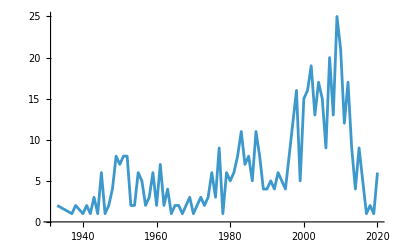

```mathematica
ListPlot[yearlist//ToExpression,PlotRange->Full,Joined->True]
```

### あらためて各主要論文の被引用の状況を確認する

最も古い主要論文は1933出版。

```mathematica
targetYears=Table[ToString[n],{n,1933,2020}]
```

{1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020}

```mathematica
(targetCandPMIDvsPY=Map[{#,PMIDtoPubyear[#]}&,top1PcCitedArtPMID])//Length
```

536

PMIDからタイトルを引く

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];*)
```

```mathematica
(*(targetCandPMIDvsTitle=Map[{#,pmidToTitle[#]}&,top1PcCitedArtPMID])//Length*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"targetCandPMIDvsTitle.save",targetCandPMIDvsTitle]*)
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"targetCandPMIDvsTitle.save"];
```

PMID vs. PMID

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/totalEdge.save"];*)
```

```mathematica
(*AbsoluteTiming[(top1PcCitedArtEdges=ParallelMap[Cases[totalEdgeList,DirectedEdge[_,#]]&,top1PcCitedArtPMID,Method->"FinestGrained"])//Length]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top1PcCitedArtEdges.save",top1PcCitedArtEdges]*)
```

以下はデータ整形

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top1PcCitedArtEdges.save"];
```

```mathematica
(top1PcCitedArtCitedyear= Map[{PMIDtoPubyear[#[[1]]],{PMIDtoPubyear[#[[2]]],#[[2]]}}&, top1PcCitedArtEdges,{2}])//Length
```

536

yearごとの被引用数リストを作る

：yearから被引用数を得る

```mathematica
toCitedyearlist[l_]:=Module[{citedPMID},
citedPMID=l[[1,2]];
{citedPMID,Association[MapApply[Rule,Tally[Map[#[[1]]&,l]]]]}
]
```

```mathematica
(top1PcCitedArtCitedyearAssociations=Map[toCitedyearlist,top1PcCitedArtCitedyear])//Length
```

536

```mathematica
top1PcCitedArtCitedyearAssociations[[1]]
```

{{1996,10062328},<|2002→1,2003→3,2004→5,2005→8,2006→11,2007→21,2008→32,2009→54,2010→57,2011→84,2012→121,2013→227,2014→271,2015→450,2016→638,2017→770,2018→832,2019→1027,2020→1208,2021→1450,2022→1805,2023→1791,2024→3|>}

：1993からの被引用数リストにする

```mathematica
fromAscToCount[asc_,year_]:=Map[asc[#]&,year]/.{_Missing->0}
```

```mathematica
fromAscToCount[top1PcCitedArtCitedyearAssociations[[1]][[2]],targetYears]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,3,5,8,11,21,32,54,57,84,121,227,271,450,638,770,832,1027,1208}

<1993からの被引用数リスト>

```mathematica
(top1PcCitedArtCitedCount["1933-2020"]=Map[{#[[1]],fromAscToCount[#[[2]],targetYears]}&,top1PcCitedArtCitedyearAssociations])//Length
```

536

：出版年からの被引用数リストにする

```mathematica
fromPY[l_,y_]:=Module[{py,pyp},
py=l[[1,1]];
pyp=Flatten[Position[y,py]][[1]];
{l[[1]],l[[2]][[pyp;;]]}
]
```

```mathematica
fromPY[top1PcCitedArtCitedCount["1933-2020"][[2]],targetYears]
```

{{1998,10069079},{0,6,34,70,107,149,184,191,223,282,320,316,351,406,428,496,523,512,572,634,573,616,607}}

```mathematica
(top1PcCitedArtCitedCount["PY-2020"]=Map[fromPY[#,targetYears]&,top1PcCitedArtCitedCount["1933-2020"]])//Length
```

536

### 分析

#### 一旦plot

出版年を原点としてplot

```mathematica
ListLinePlot3D[Map[#[[2]]&,top1PcCitedArtCitedCount["PY-2020"]],Joined->True,PlotRange->Full]
```

-Graphics3D-

#### 指標値

TODO: decayYearを設定する（peakYearを超えたあと、年間引用が全体の5%以下になる年数）

```mathematica
ndiff[l_,w_]:=BlockMap[(#[[-1]]-#[[1]])/(w-1)&,Join[Table[0,{w-1}],l],w,1]
```

```mathematica
ndiff[l_]:=BlockMap[(#[[-1]]-#[[1]])&,l,2,1]
```

```mathematica
myVar[l_]:=If[Length[l]>1,Variance[l],0]
```

```mathematica
basicStat[citedcount_]:=Module[{len,argPeak,peakYear,max,sustainYear,decayYear,firstCitedYear,total,Av5year,diff,diff2,diffTotal},
len=Length[citedcount];
argPeak=Flatten[Position[citedcount,max=Max[citedcount]]];
peakYear=argPeak[[1]];
sustainYear=len-argPeak[[-1]];
firstCitedYear=Min[Position[citedcount,x_/;x>0]]-1;
total=Total[citedcount];
Av5year=MovingAverage[Join[citedcount,Table[0,{n,4}]],5];
diff=ndiff[Av5year];
diff2=ndiff[diff];
diffTotal=Total[diff//N];
Association[{"len"->len,"peakYear"->peakYear,"peakCount"->max,"sustainYear"->sustainYear,"firstCitedYear"->firstCitedYear,"totalCited"->total,"V:Av5year"->myVar[Av5year//N],"V:diff"->myVar[diff//N],"V:diff2"->myVar[diff2//N],"diffTotal"->diffTotal}]
]
```

```mathematica
toItemNormarizeMat[l_]:=Module[{m,key},
key=Keys[l[[1,2]]];
m=Map[Normal[#[[2]]]&,l]/.{None->0};
Transpose[Map[Normalize,Transpose[Map[#[[2]]&,m,{2}]]]//N]
]
```

```mathematica
totalize[l_]:=l/Total[l]
```

```mathematica
bs=Map[{#[[1]],basicStat[#[[2]]]}&,top1PcCitedArtCitedCount["PY-2020"]]
```

#### Selection

十分にオブソレッセンスがみられるものだけを抽出する。

・出版から十分な時間が経過している：”len”が十分に長い(10年以上)
・ピーク期が十分に過ぎ去っている：“sustainYear”が“peakYear”以上
・被引用の傾向が十分に低下している：“5yeardiffTotal”が”totalCited”に比べて十分に小さい(5%以下)

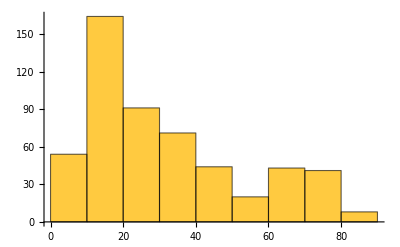

```mathematica
Map[#[[2]]["len"]&,bs]//Histogram
```

```mathematica
(obsolatedPos=Flatten[Position[bs,x_/;x[[2]]["len"]>=10&&x[[2]]["sustainYear"]>=x[[2]]["peakYear"]&&(x[[2]]["diffTotal"]/x[[2]]["totalCited"])<=0.05]])//Length
```

Part::partd: 部分指定List⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

204

```mathematica
obsolated=top1PcCitedArtCitedCount["PY-2020"][[obsolatedPos]];
```

```mathematica
obsolatedSort["PY"]=SortBy[obsolated,#[[1,1]]&];
```

以下はplotの色の調整

```mathematica
myColor1[z_]:=RGBColor[z,0.8(1-z),0.4(1-z)];
myColor2[z_]:=CMYKColor[z,((1-z)/3)^2,((1-z)/2)^2,Sqrt[z]];
myColor3[z_]:=CMYKColor[((1-z)/3)^2,z,((1-z)/2)^2,Sqrt[z]];
myColor4[z_]:=CMYKColor[((1-z)/3)^2,((1-z)/3)^2,z,Sqrt[z]];
myColor5[z_]:=CMYKColor[(z)^2,(z),(z),(z)^(1.2)];
myColor6[z_]:=Blend[{Red,Green,White},{1,0.75(1-z),(1-z)^(3)}];
cf1=Function[{x,y,z},Hue[5/6 (1-z),0.3+(z^2),1]];
cf2=Function[{x,y,z},Hue[5/6 (1-z),#+(1-#)*z,1]&@0.05];
```

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort["PY"]],Joined->True,PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->myColor2]
```

-Graphics3D-

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort["PY"]],Joined->True,PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->cf2]
```

-Graphics3D-

#### 多峰性テスト(selection)

外部（python）で行う。

：データ出力

```mathematica
outdir="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/Offload/"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/Offload/

```mathematica
prefix="citedcount_"
```

citedcount_

```mathematica
(targetfiles=Map[outdir<>prefix<>#[[1,2]]<>".csv"&,obsolatedSort["PY"]])//Length
```

204

```mathematica
(*Do[Export[targetfiles[[n]],obsolatedSort["PY"][[n]][[2]]],{n,Length[obsolatedSort["PY"]]}]*)
```

：実行

% cd /Volumes/elecom/BANK/pubmed/202312/xml/element/reference/Offload
% source ~/main/bin/activate
% for file in *csv; do python ./bin/peak_estimator.py -f $file -mc 5 -bw 1 > $file.out; done

：結果の回収

対象ファイルネームの生成

```mathematica
(ret=Map[Import[#<>".out","Text"]&,targetfiles])//Length
```

204

```mathematica
obsMultimode=(Map[StringSplit[StringSplit[#,"\n"][[-1]],": "][[-1]]&,ret]//ToExpression)
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
obsMultimodePos=Flatten[Position[obsMultimode,2]]
```

{19,24,31,42,53,105,167}

#### 指標plot(selection)

```mathematica
obsSortbc=Map[basicStat[#[[2]]]&,obsolatedSort["PY"]];
```

```mathematica
Keys[obsSortbc[[1]]]
```

{len,peakYear,peakCount,sustainYear,firstCitedYear,totalCited,V:Av5year,V:diff,V:diff2,diffTotal}

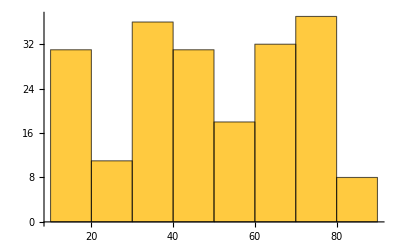

```mathematica
Histogram[Map[#["len"]&,obsSortbc]]
```

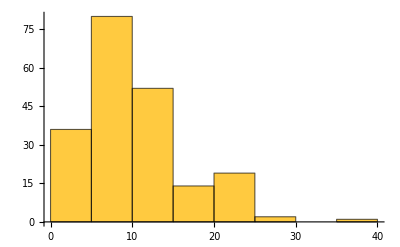

```mathematica
Histogram[Map[#["peakYear"]&,obsSortbc]]
```

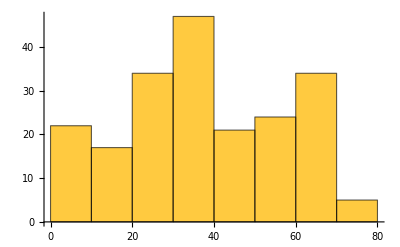

```mathematica
Histogram[Map[#["sustainYear"]&,obsSortbc]]
```

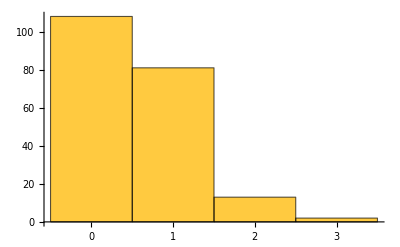

```mathematica
Histogram[Map[#["firstCitedYear"]&,obsSortbc]]
```

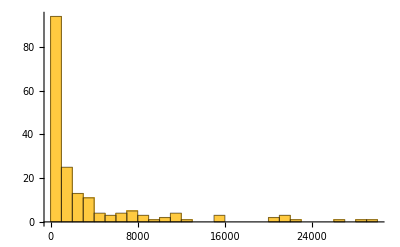

```mathematica
Histogram[Map[#["V:Av5year"]&,obsSortbc],{1000}]
```

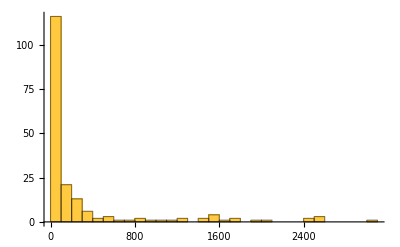

```mathematica
Histogram[Map[#["V:diff"]&,obsSortbc],{100}]
```

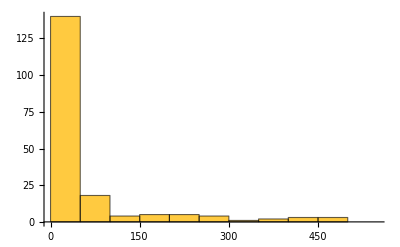

```mathematica
Histogram[Map[#["V:diff2"]&,obsSortbc],{50}]
```

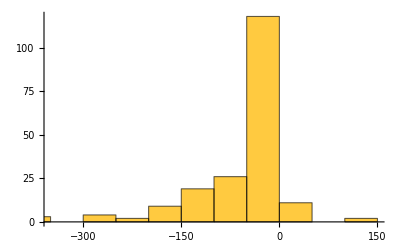

```mathematica
Histogram[Map[#["diffTotal"]&,obsSortbc]]
```

#### クラスタリング（All）: 今のところ微妙

サンプル名・サンプルPos

```mathematica
samplePMID=Map[#[[1,2]]&,bs];
```

```mathematica
samplePos=Table[n,{n,Length[bs]}];
```

データチューニング

```mathematica
(nm=toItemNormarizeMat[bs])//Dimensions
```

{536,10}

```mathematica
(nmZ=Prepend[nm,Table[0,{10}]])//Dimensions
```

{537,10}

```mathematica
(nmt=Map[totalize,nm])//Dimensions
```

{536,10}

```mathematica
(nmtZ=Prepend[nmt,Table[0,{10}]])//Dimensions
```

{537,10}

PCA

```mathematica
nmPCA=PrincipalComponents[nm];
```

```mathematica
nmZPCA=PrincipalComponents[nmZ];
```

```mathematica
nmtPCA=PrincipalComponents[nmt];
```

```mathematica
nmtZPCA=PrincipalComponents[nmtZ];
```

plot

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmPCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmZPCA[[2;;]]],Red,Point[nmZPCA[[1]][[;;3]]]}]
```

-Graphics3D-

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmtPCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmtZPCA[[2;;]]],Red,Point[nmtZPCA[[1]][[;;3]]]}]
```

-Graphics3D-

クラスタリング
nmに対してコサイン距離を使うのが良いか。

```mathematica
clusteredPos=.
```

```mathematica
clusteredPos["SD","Agg"]=FindClusters[nm->samplePos,DistanceFunction->CosineDistance,CriterionFunction->"StandardDeviation",Method->"Agglomerate"]
```

{{4,6,9,12,13,18,21,23,24,27,30,32,34,38,42,44,45,47,49,50,53,55,58,63,65,67,70,74,87,89,97,101,139,142,143,144,145,146,154,156,168,172,173,174,186,192,206,207,209,217,220,227,317,357,358,376,382,406,414,422,431,481,489,493,494,496,500,502,503,507,513,518,520,521,522,524,526,532,533,535},{11,28,33,60,62,64,153,530},{66,228,246},{8,16,229},{41,52,509,525,528},{250,264,272,275,289},{141,171,221},{7,35,150},{262,294,300,312,318},{170,245,247},{288,291,299,333},{311,334},{307,324,327},{266,297,305,314},{276,298},{169,210,253},{265,292},{325},{219,223,252,267},{256},{237,527},{261,295},{208,231,273},{258,282,315},{243},{269},{244,274,306,339},{302,322,344,372,378},{224},{148,185,284},{216},{263},{374},{259,270,290,304},{303,329},{17},{147,177},{373},{364},{10,69,379},{309,331,336,337,341,342},{222},{25},{151},{359},{366},{368},{360},{346},{31,72,73,78,85,88,91,103,104,106,107,108,109,113,114,115,128,136,137,157,163,166,188,189,194,196,198,200,203,204,213,232,233,238,241,248,320,350,369,370,383,388,390,394,399,407,413,417,419,430,432,435,436,443,446,448,450,451,458,459,460,461,462,464,467,468,474,477,484},{182},{354},{22,59,385,452},{469,479,505},{512},{235,260},{225,257,281,287},{483,506,515},{3,5,15,36,56,57,61,95,96,100,102,175,176,181,187,215,226,254,268,381,395,401,402,403,404,409,411,418,423,425,428,429,441,453,471,472,480,482,486,487,491,492,498,499,504,508,519,523,529},{293},{1,116,165,236,278,377,416,438,473,478,485,531,536},{26,40,68,408,415,476,495},{51,501},{2,54,470},{178},{48},{412},{122},{497,534},{120,211},{164},{152},{516},{180},{14,29},{323},{183,251},{348},{345},{330,340,349},{271,277,296},{285,328},{279},{301},{283},{319},{356,361},{332,338},{326},{308},{313,351},{362,367},{310,335,353},{365},{190},{343},{140},{123},{71},{230,280},{149},{255},{179},{517},{19,39,75,76,77,79,80,81,82,83,84,86,90,92,93,94,98,99,105,110,111,112,117,118,119,124,125,127,129,130,131,132,133,135,138,155,158,159,160,161,162,184,191,193,195,197,199,201,202,205,212,214,218,347,386,400,405,410,424,426,427,433,434,437,442,444,449,454,455,456,465,466,490,510},{447},{420},{439,457,475},{126},{37,355,445},{286},{240},{249},{514},{134},{440},{511},{239},{488},{384},{321},{316},{121},{234},{167},{463},{20},{363,371},{380},{352},{46,421},{242},{375},{43},{387},{391,392,393,396,397,398},{389}}

```mathematica
clusteredPos["Dunn","Agg"]=FindClusters[nm->samplePos,DistanceFunction->CosineDistance,CriterionFunction->"Dunn",Method->"Agglomerate"]
```

{{4,6,9,12,13,18,21,23,24,27,30,32,34,38,42,44,45,47,49,50,53,55,58,63,65,67,70,74,87,89,97,101,139,142,143,144,145,146,154,156,168,172,173,174,186,192,206,207,209,217,220,227,317,357,358,376,382,406,414,422,431,481,489,493,494,496,500,502,503,507,513,518,520,521,522,524,526,532,533,535},{11,28,33,60,62,64,153,530},{66,228,246},{8,16,229},{41,52,509,525,528},{250,264,272,275,289},{141,171,221},{7,35,150},{262,294,300,312,318},{170,245,247},{288,291,299,333},{311,334},{307,324,327},{266,297,305,314},{276,298},{169,210,253},{265,292},{325},{219,223,252,267},{256},{237,527},{261,295},{208,231,273},{258,282,315},{243},{269},{244,274,306,339},{302,322,344,372,378},{224},{148,185,284},{216},{263},{374},{259,270,290,304},{303,329},{17},{147,177},{373},{364},{10,69,379},{309,331,336,337,341,342},{222},{25},{151},{359},{366},{368},{360},{346},{31,72,73,78,85,88,91,103,104,106,107,108,109,113,114,115,128,136,137,157,163,166,188,189,194,196,198,200,203,204,213,232,233,238,241,248,320,350,369,370,383,388,390,394,399,407,413,417,419,430,432,435,436,443,446,448,450,451,458,459,460,461,462,464,467,468,474,477,484},{182},{354},{22,59,385,452},{469,479,505},{512},{235,260},{225,257,281,287},{483,506,515},{3,5,15,36,56,57,61,95,96,100,102,175,176,181,187,215,226,254,268,381,395,401,402,403,404,409,411,418,423,425,428,429,441,453,471,472,480,482,486,487,491,492,498,499,504,508,519,523,529},{293},{1,116,165,236,278,377,416,438,473,478,485,531,536},{26,40,68,408,415,476,495},{51,501},{2,54,470},{178},{48},{412},{122},{497,534},{120,211},{164},{152},{516},{180},{14,29},{323},{183,251},{348},{345},{330,340,349},{271,277,296},{285,328},{279},{301},{283},{319},{356,361},{332,338},{326},{308},{313,351},{362,367},{310,335,353},{365},{190},{343},{140},{123},{71},{230,280},{149},{255},{179},{517},{19,39,75,76,77,79,80,81,82,83,84,86,90,92,93,94,98,99,105,110,111,112,117,118,119,124,125,127,129,130,131,132,133,135,138,155,158,159,160,161,162,184,191,193,195,197,199,201,202,205,212,214,218,347,386,400,405,410,424,426,427,433,434,437,442,444,449,454,455,456,465,466,490,510},{447},{420},{439,457,475},{126},{37,355,445},{286},{240},{249},{514},{134},{440},{511},{239},{488},{384},{321},{316},{121},{234},{167},{463},{20},{363,371},{380},{352},{46,421},{242},{375},{43},{387},{391,392,393,396,397,398},{389}}

selected （204 個）の全サンプル（536個）のクラスタ割り当て

```mathematica
classApply["SD","Agg"]=Map[{Length[#],Length[Intersection[#,obsolatedPos]]}&,clusteredPos["SD","Agg"]]
```

{{80,0},{8,2},{3,0},{3,0},{5,0},{5,0},{3,0},{3,0},{5,0},{3,1},{4,0},{2,0},{3,0},{4,0},{2,0},{3,0},{2,0},{1,0},{4,4},{1,0},{2,2},{2,0},{3,0},{3,0},{1,0},{1,0},{4,3},{5,1},{1,1},{3,3},{1,1},{1,1},{1,0},{4,0},{2,0},{1,0},{2,2},{1,0},{1,0},{3,0},{6,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{69,69},{1,1},{1,1},{4,4},{3,3},{1,1},{2,0},{4,0},{3,2},{49,0},{1,0},{13,0},{7,0},{2,0},{3,0},{1,0},{1,0},{1,0},{1,0},{2,0},{2,1},{1,0},{1,0},{1,0},{1,0},{2,0},{1,0},{2,0},{1,0},{1,0},{3,0},{3,0},{2,0},{1,0},{1,0},{1,0},{1,0},{2,0},{2,0},{1,0},{1,1},{2,1},{2,0},{3,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{2,0},{1,0},{1,0},{1,0},{1,0},{74,74},{1,1},{1,1},{3,3},{1,1},{3,3},{1,0},{1,0},{1,0},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,1},{1,1},{1,1},{2,0},{1,0},{1,1},{2,2},{1,1},{1,1},{1,0},{1,0},{6,0},{1,0}}

```mathematica
classApply["Dunn","Agg"]=Map[{Length[#],Length[Intersection[#,obsolatedPos]]}&,clusteredPos["Dunn","Agg"]]
```

{{80,0},{8,2},{3,0},{3,0},{5,0},{5,0},{3,0},{3,0},{5,0},{3,1},{4,0},{2,0},{3,0},{4,0},{2,0},{3,0},{2,0},{1,0},{4,4},{1,0},{2,2},{2,0},{3,0},{3,0},{1,0},{1,0},{4,3},{5,1},{1,1},{3,3},{1,1},{1,1},{1,0},{4,0},{2,0},{1,0},{2,2},{1,0},{1,0},{3,0},{6,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{69,69},{1,1},{1,1},{4,4},{3,3},{1,1},{2,0},{4,0},{3,2},{49,0},{1,0},{13,0},{7,0},{2,0},{3,0},{1,0},{1,0},{1,0},{1,0},{2,0},{2,1},{1,0},{1,0},{1,0},{1,0},{2,0},{1,0},{2,0},{1,0},{1,0},{3,0},{3,0},{2,0},{1,0},{1,0},{1,0},{1,0},{2,0},{2,0},{1,0},{1,1},{2,1},{2,0},{3,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{2,0},{1,0},{1,0},{1,0},{1,0},{74,74},{1,1},{1,1},{3,3},{1,1},{3,3},{1,0},{1,0},{1,0},{1,0},{1,1},{1,1},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,1},{1,1},{1,1},{2,0},{1,0},{1,1},{2,2},{1,1},{1,1},{1,0},{1,0},{6,0},{1,0}}

```mathematica
Cases[classApply["Dunn","Agg"],{_,y_}/;y!=0]//Length
```

42

#### クラスタリング（select）

サンプル名・サンプルPos

```mathematica
(bsObs=bs[[obsolatedPos]])//Length
```

204

```mathematica
(sampleObsPMID=Map[#[[1,2]]&,bsObs])//Length
```

204

```mathematica
(sampleObsPos=Table[n,{n,Length[bsObs]}])//Length
```

204

データチューニング

```mathematica
(nmObs=toItemNormarizeMat[bsObs])//Dimensions
```

{204,10}

```mathematica
(nmZObs=Prepend[nmObs,Table[0,{10}]])//Dimensions
```

{205,10}

```mathematica
(nmtObs=Map[totalize,nmObs])//Dimensions
```

{204,10}

```mathematica
(nmtZObs=Prepend[nmtObs,Table[0,{10}]])//Dimensions
```

{205,10}

PCA

```mathematica
nmObsPCA=PrincipalComponents[nmObs];
```

```mathematica
nmZObsPCA=PrincipalComponents[nmZObs];
```

```mathematica
nmtObsPCA=PrincipalComponents[nmtObs];
```

```mathematica
nmtZObsPCA=PrincipalComponents[nmtZObs];
```

plot

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmObsPCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmZObsPCA[[2;;]]],Red,Point[nmZObsPCA[[1]][[;;3]]]}]
```

-Graphics3D-

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmtObsPCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmtZObsPCA[[2;;]]],Red,Point[nmtZObsPCA[[1]][[;;3]]]}]
```

-Graphics3D-

クラスタリング
nmに対してコサイン距離を使うのが良いか。

```mathematica
clusteredPos=.
```

```mathematica
clusteredPosObs["SD","Agg"]=FindClusters[nmObs->sampleObsPos,DistanceFunction->CosineDistance,CriterionFunction->"StandardDeviation",Method->"Agglomerate"]
```

{{1,6,7,13,14,15,17,18,19,20,21,26,28,29,32,35,40,47,48,50,55,56,57,59,61,64,68,70,71,72,73,74,81,86,89,91,93,95,99,104,130,134,140,145,146,148,154,156,160,163,166,169,173,177,178,179,188,199,201},{22,24,30,31,41,42,46,51,53,58,87,96,100,102,155,159,168,189},{171},{164},{152,180,194},{52},{197,203},{2},{114},{186},{49},{8,153},{132},{103},{108},{117},{66,82,123},{80},{3,5,9,16,27,33,63,76,88,129,131,135,136,138,141,142,143,144,147,149,150,151,157,161,167,170,172,174,175,181,182,183,184,185,187,190,191,193,196,198},{139},{39,118},{11,12,23,25,34,36,37,38,43,44,45,54,62,69,83,84,90,92,94,97,98,101,109,110,113},{176},{133},{75,85,115,158,162},{202},{125},{105,107,119,121},{112},{65,79},{78},{4,204},{10},{192},{195,200},{122,124},{120},{67},{137},{106},{127},{126},{128},{77},{111},{116},{165},{60}}

```mathematica
clusteredPosObs["Dunn","Agg"]=FindClusters[nmObs->sampleObsPos,DistanceFunction->CosineDistance,CriterionFunction->"Dunn",Method->"Agglomerate"]
```

{{1,6,7,13,14,15,17,18,19,20,21,26,28,29,32,35,40,47,48,50,55,56,57,59,61,64,68,70,71,72,73,74,81,86,89,91,93,95,99,104,130,134,140,145,146,148,154,156,160,163,166,169,173,177,178,179,188,199,201},{22,24,30,31,41,42,46,51,53,58,87,96,100,102,155,159,168,189},{171},{164},{152,180,194},{52},{197,203},{2},{114},{186},{49},{8,153},{132},{103},{108},{117},{66,82,123},{80},{3,5,9,16,27,33,63,76,88,129,131,135,136,138,141,142,143,144,147,149,150,151,157,161,167,170,172,174,175,181,182,183,184,185,187,190,191,193,196,198},{139},{39,118},{11,12,23,25,34,36,37,38,43,44,45,54,62,69,83,84,90,92,94,97,98,101,109,110,113},{176},{133},{75,85,115,158,162},{202},{125},{105,107,119,121},{112},{65,79},{78},{4,204},{10},{192},{195,200},{122,124},{120},{67},{137},{106},{127},{126},{128},{77},{111},{116},{165},{60}}

```mathematica
clusteredPosObs["Dunn","Agg"]//Length
```

48

```mathematica
Map[Length,clusteredPosObs["Dunn","Agg"]]
```

{59,18,1,1,3,1,2,1,1,1,1,2,1,1,1,1,3,1,40,1,2,25,1,1,5,1,1,4,1,2,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Map[Intersection[#,obsMultimodePos]&,clusteredPosObs["Dunn","Agg"]]
```

{{19},{24,31,42,53},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{167},{},{},{},{},{},{},{},{},{105},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

## 連絡事項

西澤さんにデータ送る。

```mathematica
(*Save["lists.wl",obsolatedSort]*)
```

## test

```mathematica
m={{1,1,2,2},{2,2,4,4},{3,3,6,6}}
```

{{1,1,2,2},{2,2,4,4},{3,3,6,6}}

```mathematica
Normalize[m[[1]]]
```

{1/(√10),1/(√10),√(2/5),√(2/5)}

```mathematica
Normalize[{"len"->10,"len"->3}]
```

{(len→10)/(√(Abs[len→3]^2+Abs[len→10]^2)),(len→3)/(√(Abs[len→3]^2+Abs[len→10]^2))}

```mathematica
Intersection[obsolatedPos,clusteredPos[[1]]]
```

{64,134,151,170,219,223,237,252,284,440}

```mathematica
Map[Length,clusteredPos]
```

{206,5,5,9,2,37,5,11,11,16,4,9,6,6,2,6,4,12,65,14,75,5,6,9,6}